```mathematica
Quit[]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/cesarecarlomella/Documents/GitHub/two-point-correlators-with-masses/yukawa_photon/3loop

```mathematica
<<LiteRed2`
(*<<Mint`*)
```

**************** LiteRed v2.025β ********************
Author: Roman N. Lee, Budker Institute of Nuclear Physics, Novosibirsk.
Release Date: ????-??-??
Timestamp: Tue 1 Apr 2025 22:18:26
Read from:/Users/cesarecarlomella/Software/LiteRed2/LiteRed2025.m (CRC32:2902354241,{2340977437, 3317197336, 1063727846})

LiteRed stands for Loop integrals Reduction.
The package is designed for the search and application of the Integration-By-Part reduction rules. It also contains some other useful tools.

See ?LiteRed`* for a list of functions.

```mathematica
Grid[{{"D1",k1^2-m^2,k1^2-m^2,k1^2-m^2},{"D2",k2^2-m^2,k2^2-m^2,k2^2-m^2},{"D3",k3^2-m^2,k3^2,k3^2},{"D4",(k1-p)^2-m^2,(k1-p)^2-m^2,(k1-p)^2-m^2},{"D5",(k2-p)^2-m^2,(k2-p)^2-m^2,(k2-p)^2-m^2},{"D6",(k3-p)^2-m^2,(k3-p)^2,(k3-p)^2},{"D7",(k1-k2)^2,(k1-k3)^2-m^2,(k1-k2)^2},{"D8",(k1-k3)^2,(k2-k3)^2-m^2,(k2+k3-p)^2-m^2},{"D9",(k2-k3)^2,(k1+k2-k3-p)^2,(k1+k3-p)^2-m^2}},Frame->All]
```

D1 | k1^2-m^2 | k1^2-m^2 | k1^2-m^2
D2 | k2^2-m^2 | k2^2-m^2 | k2^2-m^2
D3 | k3^2-m^2 | k3^2 | k3^2
D4 | -m^2+(k1-p)^2 | -m^2+(k1-p)^2 | -m^2+(k1-p)^2
D5 | -m^2+(k2-p)^2 | -m^2+(k2-p)^2 | -m^2+(k2-p)^2
D6 | -m^2+(k3-p)^2 | (k3-p)^2 | (k3-p)^2
D7 | (k1-k2)^2 | (k1-k3)^2-m^2 | (k1-k2)^2
D8 | (k1-k3)^2 | (k2-k3)^2-m^2 | -m^2+(k2+k3-p)^2
D9 | (k2-k3)^2 | (k1+k2-k3-p)^2 | -m^2+(k1+k3-p)^2

### Preliminaries famA

```mathematica
family = famA;
```

```mathematica
SetDim[d];
Declare[
{p,k1,k2,k3},Vector,
{pp,m2},Number];
(* kinematics *)
q=-p;
sp[p,p]=pp;
```

```mathematica
intfam  = {-m2+sp[k1,k1],-m2+sp[k2,k2],-m2+sp[k3,k3],-m2+sp[k1,k1]-2 sp[k1,p]+sp[p,p],-m2+sp[k2,k2]-2 sp[k2,p]+sp[p,p],-m2+sp[k3,k3]-2 sp[k3,p]+sp[p,p],sp[k1,k1]-2 sp[k1,k2]+sp[k2,k2],sp[k1,k1]-2 sp[k1,k3]+sp[k3,k3],sp[k2,k2]-2 sp[k2,k3]+sp[k3,k3]}
```

{-m2+k1·k1,-m2+k2·k2,-m2+k3·k3,-m2+pp+k1·k1-2 k1·p,-m2+pp+k2·k2-2 k2·p,-m2+pp+k3·k3-2 k3·p,k1·k1-2 k1·k2+k2·k2,k1·k1-2 k1·k3+k3·k3,k2·k2-2 k2·k3+k3·k3}

```mathematica
(*(*Initialize integral family*)(*--------------------------------------------------------------*)NewDsBasis[family,intfam,{k1,k2,k3},Directory->"famA"]

GenerateIBP[family];

AnalyzeSectors[family];

FindSymmetries[family];

(*Solve IBP reduction for unique sectors*)
(*--------------------------------------------------------------*)
SolvejSector/@UniqueSectors[family];*)

(*Save to disk*)
(*DiskSave[family];*)
```

```mathematica
Get["./famA/famA"];
```

```mathematica
MIs[family]
```

{j[famA,0,0,0,1,1,1,0,0,0],j[famA,0,0,0,0,1,1,1,1,0],j[famA,0,0,1,0,1,0,1,1,0],j[famA,0,0,2,0,1,0,1,1,0],j[famA,0,0,1,0,1,0,2,1,0],j[famA,0,0,1,1,1,0,0,0,1],j[famA,0,0,2,1,1,0,0,0,1],j[famA,0,0,1,1,1,1,0,0,0],j[famA,0,0,1,0,1,1,1,1,0],j[famA,0,0,1,1,1,0,0,1,1],j[famA,0,0,2,1,1,0,0,1,1],j[famA,0,0,1,2,1,0,0,1,1],j[famA,0,1,1,1,0,1,1,0,0],j[famA,0,2,1,1,0,1,1,0,0],j[famA,0,1,1,1,1,1,0,0,0],j[famA,0,1,1,0,1,1,1,1,0],j[famA,0,1,1,1,0,1,1,0,1],j[famA,1,1,1,1,1,1,0,0,0],j[famA,0,1,1,1,1,1,1,1,0],j[famA,0,2,1,1,1,1,1,1,0]}

```mathematica
MIs[family]
mis=MIs[family];
tomis=ToMIsRule[mis];
```

{j[famA,0,0,0,1,1,1,0,0,0],j[famA,0,0,0,0,1,1,1,1,0],j[famA,0,0,1,0,1,0,1,1,0],j[famA,0,0,2,0,1,0,1,1,0],j[famA,0,0,1,0,1,0,2,1,0],j[famA,0,0,1,1,1,0,0,0,1],j[famA,0,0,2,1,1,0,0,0,1],j[famA,0,0,1,1,1,1,0,0,0],j[famA,0,0,1,0,1,1,1,1,0],j[famA,0,0,1,1,1,0,0,1,1],j[famA,0,0,2,1,1,0,0,1,1],j[famA,0,0,1,2,1,0,0,1,1],j[famA,0,1,1,1,0,1,1,0,0],j[famA,0,2,1,1,0,1,1,0,0],j[famA,0,1,1,1,1,1,0,0,0],j[famA,0,1,1,0,1,1,1,1,0],j[famA,0,1,1,1,0,1,1,0,1],j[famA,1,1,1,1,1,1,0,0,0],j[famA,0,1,1,1,1,1,1,1,0],j[famA,0,2,1,1,1,1,1,1,0]}

```mathematica
IBPReduce[j[famA,1,1,1,1,1,0,0,0,0]]
```

j[famA,0,1,1,1,1,1,0,0,0]

```mathematica
(*LiteRed Masters*)
todiff= MIs[family];
```

```mathematica
(*diff eq for LiteRed Masters*)
derpp = Dinv[todiff,pp];
derm2 = Dinv[todiff,m2];
rhs=Union[Join[Union@Cases[derpp, j[family,a__],Infinity],Union@Cases[derm2, j[family,a__],Infinity]]];
rhsRed = Collect[IBPReduce[rhs],{_j}, Factor];
ReplaceRHS = Thread[Rule[rhs,rhsRed]];
redderpp=Collect[derpp/.ReplaceRHS, {_j},Factor];
redderm2=Collect[derm2/.ReplaceRHS, {_j},Factor];
MppLiteRed = CoefficientArrays[redderpp,todiff][[2]]//Normal;
Mm2LiteRed = CoefficientArrays[redderm2,todiff][[2]]//Normal;
```

```mathematica
(*MppLiteRed//MatrixPlot
Mm2LiteRed//MatrixPlot*)
```

```mathematica
listSectorA= Table[FromDigits[Reverse[(todiff[[i,2;;]]/. 2-> 1 /. j -> List) ],2], {i,1,Length[todiff]}]
```

{56,240,212,212,212,284,284,60,244,412,412,412,110,110,62,246,366,63,254,254}

```mathematica
Table[{todiff[[i]] /. 2-> 1,FromDigits[Reverse[(todiff[[i,2;;]]/. 2-> 1 /. j -> List) ],2], Total[todiff[[i,2;;]] /. 2-> 1/. j -> List]}, {i,1,Length[todiff]}]//TableForm
```

j[famA,0,0,0,1,1,1,0,0,0] | 56 | 3
j[famA,0,0,0,0,1,1,1,1,0] | 240 | 4
j[famA,0,0,1,0,1,0,1,1,0] | 212 | 4
j[famA,0,0,1,0,1,0,1,1,0] | 212 | 4
j[famA,0,0,1,0,1,0,1,1,0] | 212 | 4
j[famA,0,0,1,1,1,0,0,0,1] | 284 | 4
j[famA,0,0,1,1,1,0,0,0,1] | 284 | 4
j[famA,0,0,1,1,1,1,0,0,0] | 60 | 4
j[famA,0,0,1,0,1,1,1,1,0] | 244 | 5
j[famA,0,0,1,1,1,0,0,1,1] | 412 | 5
j[famA,0,0,1,1,1,0,0,1,1] | 412 | 5
j[famA,0,0,1,1,1,0,0,1,1] | 412 | 5
j[famA,0,1,1,1,0,1,1,0,0] | 110 | 5
j[famA,0,1,1,1,0,1,1,0,0] | 110 | 5
j[famA,0,1,1,1,1,1,0,0,0] | 62 | 5
j[famA,0,1,1,0,1,1,1,1,0] | 246 | 6
j[famA,0,1,1,1,0,1,1,0,1] | 366 | 6
j[famA,1,1,1,1,1,1,0,0,0] | 63 | 6
j[famA,0,1,1,1,1,1,1,1,0] | 254 | 7
j[famA,0,1,1,1,1,1,1,1,0] | 254 | 7

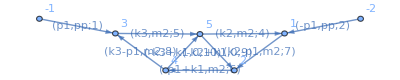

```mathematica
Import["./graphs/topoA/all/topoA_7_254.dot"]
```

### Start From d = 2

```mathematica
Length[todiff]
```

20

```mathematica
(*My Masters basis in d=2*)
mybasis= {(d-2)j[famA,0,0,0,1,1,1,0,0,0], (* tadpole ^ 3    t = 3*)
 (-5+2 d)m2 j[famA,0,0,0,0,1,1,1,1,0], (* sunrise with two masses and no momentum  t = 4 *)
(* three MI sunrise*)
(d-2) √(4m2-pp) √pp j[famA,0,0,1,0,1,0,1,1,0], (* banana with 2 equal masses  t = 3 *)
(d-2) j[famA,0,0,1,-1,1,0,1,1,0],
(d-2) j[famA,0,0,1,0,1,-1,1,1,0],
(* *)
(d-2)  j[famA,0,-1,1,1,1,0,0,0,1], (* 2 sunrise with one mass * tadpole     t = 4 *)
(d-2)Sqrt[pp] √(4 m2-pp) j[famA,0,0,1,1,1,0,0,0,1], (* 2 sunrise with one mass * tadpole   t = 4 *)
(* *)
(d-2)√pp √(4 m2-pp) j[famA,0,0,1,1,1,1,0,0,0], (* tadpole^2 * bubble   t = 4 *)
(* *)
(d-2) √(4m2-pp) √pp j[famA,0,0,1,-1,1,1,1,1,0],(*  t = 5  *)
(* *)
(d-2)√(4m2-pp)Sqrt[pp]  j[famA,0,0,1,1,1,-1,0,1,1], (* triangle with two bubbles, 3 MIs      t = 5 *)
(d-2)((m2-pp)j[famA,0,0,1,1,1,0,-1,1,1]+2 (-m2+pp) j[famA,0,0,1,1,1,0,0,0,1]),
(d-2) (j[famA,0,0,1,1,1,-1,-1,1,1]+m2  j[famA,0,0,1,1,1,0,-1,1,1] -2 m2 j[famA,0,0,1,1,1,0,0,0,1]),
(*    *)
(d-2)((4m2-pp) pp)j[famA,0,1,1,1,0,1,1,0,0], (*      t = 5     *)
(d-2)√(4m2-pp)Sqrt[pp] j[famA,0,1,1,1,-1,1,1,0,0],
(* *)
(d-2)pp(4m2-pp)j[famA,0,1,1,1,1,1,0,0,0],  (*      t = 5     *)
(* *)
(d-2)(4 m2-pp) pp j[famA,0,1,1,0,1,1,1,1,-1],  (*      t = 6     *)
(* *)
(d-2)m2 j[famA,0,1,1,1,-1,1,1,-1,1] + (-2+d) (2 m2-pp) j[famA,0,0,1,-1,1,1,1,1,0]+1/2 (-2+d) (-2 m2+pp) j[famA,0,0,1,0,1,0,1,1,0]-1/2 (-2+d) (-2 m2+pp) j[famA,0,0,1,1,1,0,0,0,1]-1/2 (-2+d)  (-2 m2+pp) j[famA,0,1,1,1,-1,1,1,0,0]+ (-7+2 d)/(2 (-3+d))(d-2)j[famA,0,0,0,1,1,1,0,0,0],  (*      t = 6     *)
(* *)
(d-2)(4m2-pp )^(3/2)pp^(3/2) j[famA,1,1,1,1,1,1,0,0,0],  (*      t =  6     *)
(*  the top sector has to be studied in d = 4 *)
j[famA,0,1,1,1,1,1,1,1,0],
  j[famA,1,1,1,1,1,1,1,1,0]};
(* my = T.LiteRed*)
T=CoefficientArrays[(IBPReduce[mybasis]) ,todiff][[2]]//Normal;
T.todiff -IBPReduce[ mybasis]//Together//Union;
```

```mathematica
(*T=T//Simplify//PowerExpand;*)
```

```mathematica
(*invT=Inverse[T]//Simplify;
invT=invT // PowerExpand;*)
```

```mathematica
(*derTpp = D[T,pp]//Simplify;
derTm2 = D[T,m2]//Simplify;*)
```

```mathematica
(*Mpp=(derTpp.invT//Simplify) + T.MppLiteRed.(invT)//PowerExpand//Simplify;
Mm2=(derTm2.invT//Simplify) + T.Mm2LiteRed.(invT)//PowerExpand//Simplify;*)
```

```mathematica
homT=T[[;;9,;;9]];
invhomT=Inverse[homT]//Simplify;
invhomT=invhomT // PowerExpand;
derhomTpp = D[homT,pp]//Simplify;
derhomTm2 = D[homT,m2]//Simplify;
Mpp=(derhomTpp.invhomT//Simplify) + homT.MppLiteRed[[;;9,;;9]].(invhomT)//PowerExpand//Simplify;
R2 = IdentityMatrix[9];
R2[[1,1]] =1
Mpptest=(D[R2,pp].Inverse[R2]//Simplify) + R2.Mpp.(Inverse[R2])//PowerExpand//Simplify;
```

1

### Shift in d ~ 4

```mathematica
toshift ={j[famA,0,-1,1,1,1,0,0,0,1],j[famA,0,0,0,0,1,1,1,1,0],j[famA,0,0,0,1,1,1,0,0,0],j[famA,0,0,1,-1,1,0,1,1,0],j[famA,0,0,1,-1,1,1,1,1,0],j[famA,0,0,1,0,1,-1,1,1,0],j[famA,0,0,1,0,1,0,1,1,0],j[famA,0,0,1,1,1,-1,-1,1,1],j[famA,0,0,1,1,1,-1,0,1,1],j[famA,0,0,1,1,1,0,-1,1,1],j[famA,0,0,1,1,1,0,0,0,1],j[famA,0,0,1,1,1,1,0,0,0],j[famA,0,1,1,0,1,1,1,1,-1],j[famA,0,1,1,1,-1,1,1,-1,1],j[famA,0,1,1,1,-1,1,1,0,0],j[famA,0,1,1,1,0,1,1,0,0],j[famA,0,1,1,1,1,1,0,0,0],j[famA,1,1,1,1,1,1,0,0,0]};
toshift= toshift/. j[famA, a__] :> "topoA "<>StringReplace[StringReplace[StringReplace[ToString[{a}] , ","->""],"{"->""],"}"->""]
```

{topoA 0 -1 1 1 1 0 0 0 1,topoA 0 0 0 0 1 1 1 1 0,topoA 0 0 0 1 1 1 0 0 0,topoA 0 0 1 -1 1 0 1 1 0,topoA 0 0 1 -1 1 1 1 1 0,topoA 0 0 1 0 1 -1 1 1 0,topoA 0 0 1 0 1 0 1 1 0,topoA 0 0 1 1 1 -1 -1 1 1,topoA 0 0 1 1 1 -1 0 1 1,topoA 0 0 1 1 1 0 -1 1 1,topoA 0 0 1 1 1 0 0 0 1,topoA 0 0 1 1 1 1 0 0 0,topoA 0 1 1 0 1 1 1 1 -1,topoA 0 1 1 1 -1 1 1 -1 1,topoA 0 1 1 1 -1 1 1 0 0,topoA 0 1 1 1 0 1 1 0 0,topoA 0 1 1 1 1 1 0 0 0,topoA 1 1 1 1 1 1 0 0 0}

```mathematica
Close["tbshifted"]
Do[WriteLine["tbshifted", toshift[[i]]], {i,1,Length[toshift]}]
```

General::openx: tbshifted is not open.

Close[tbshifted]

```mathematica
shifts=Import["./ints_dimshifted.m"]/. INT["topoAdimdec2",a__,{bin__}]:>j[famA, bin] /. INT["topoA",a__, {bin__}]:>j[famA,bin];
```

```mathematica
mybasisd4=mybasis/. d-> d-2/.shifts;
mybasisd4[[19]]=(d-4)^3(d-3)m2^3 j[famA,0,1,1,1,1,1,1,1,0]pp;
mybasisd4[[20]]=(d-4)^3(d-3)m2^3 j[famA,1,1,1,1,1,1,1,1,0] pp^(3/2) √(4 m2-pp);
mybasisd4 = mybasisd4/m2/m2/m2;
```

```mathematica
(* my = T.LiteRed*)
T=CoefficientArrays[(IBPReduce[mybasisd4]) ,todiff][[2]]//Normal;
T.todiff -IBPReduce[ mybasisd4]//Together//Union;
```

```mathematica
T=T//Simplify//PowerExpand;
```

```mathematica
Tsymb=T /.{ Sqrt[pp]-> sqrtpp, 1/Sqrt[pp]->sqrtpp/pp ,pp^(3/2) -> sqrtpp pp, 1/pp^(3/2) -> sqrtpp/pp/ pp ,Sqrt[(4 m2-pp)]->sqrt4m2, 1/Sqrt[(4 m2-pp)] -> sqrt4m2/(4m2 -pp) ,(4 m2-pp)^(5/2)->sqrt4m2 (4 m2 -pp)^2, 1/(4 m2-pp)^(5/2)->sqrt4m2/((4 m2-pp)^3),(4 m2-pp)^(3/2)->sqrt4m2 (4 m2-pp), 1/(4 m2-pp)^(3/2)->sqrt4m2 /((4 m2 -pp)^2)}//Simplify;
(*% /. sqrt4m2-> 0 /. sqrtpp ->0*)
```

```mathematica
<<FiniteFlow`
```

```mathematica
TinvSymb=FFInverse[Tsymb]// Simplify;
```

```mathematica
invT=TinvSymb /. sqrt4m2 ->Sqrt[4m2-pp] /. sqrtpp ->Sqrt[pp];
```

```mathematica
T.invT// Simplify
```

{{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1}}

```mathematica
derTpp = D[T,pp]//Simplify;
derTm2 = D[T,m2]//Simplify;
```

```mathematica
Mpp=(derTpp.invT//Simplify) + T.MppLiteRed.(invT)//PowerExpand//Simplify;
Mm2=(derTm2.invT//Simplify) + T.Mm2LiteRed.(invT)//PowerExpand//Simplify;
```

```mathematica
(Integrate[Mm2 /(d-4) ,m2]//TrigToExp) /. _Log -> 0//Flatten //Union
(Integrate[Mpp /(d-4) ,pp]//TrigToExp) /. _Log -> 0//Flatten //Union
```

{0}

{0}

```mathematica
mybasisd4=Collect[mybasisd4, {_j},Simplify];
```

### NPL famB

```mathematica
family2 = famB;
intfam2  = {-m2+sp[k1,k1],-m2+sp[k2,k2],sp[k3,k3],-m2+sp[k1,k1]-2 sp[k1,p]+sp[p,p],-m2+sp[k2,k2]-2 sp[k2,p]+sp[p,p],sp[k3,k3]-2 sp[k3,p]+sp[p,p],sp[k1,k1]-2 sp[k1,k3]+sp[k3,k3]-m2,sp[k2,k2]-2 sp[k2,k3]+sp[k3,k3]-m2,pp+sp[k1,k1]+sp[k1,k2]-sp[k1,k3]-sp[k1,p]+sp[k2,k1]+sp[k2,k2]-sp[k2,k3]-sp[k2,p]-sp[k3,k1]-sp[k3,k2]+sp[k3,k3]+sp[k3,p]-sp[p,k1]-sp[p,k2]+sp[p,k3]}
```

{-m2+sp[k1,k1],-m2+sp[k2,k2],sp[k3,k3],-m2+sp[k1,k1]-2 sp[k1,p]+sp[p,p],-m2+sp[k2,k2]-2 sp[k2,p]+sp[p,p],sp[k3,k3]-2 sp[k3,p]+sp[p,p],-m2+sp[k1,k1]-2 sp[k1,k3]+sp[k3,k3],-m2+sp[k2,k2]-2 sp[k2,k3]+sp[k3,k3],pp+sp[k1,k1]+2 sp[k1,k2]-2 sp[k1,k3]-2 sp[k1,p]+sp[k2,k2]-2 sp[k2,k3]-2 sp[k2,p]+sp[k3,k3]+2 sp[k3,p]}

```mathematica
shiftsB2A=Import["./shift_B_to_A/kira_toreducetoreduceB.inc.m"];
```

```mathematica
mastersB ={ topoB[1,1,0,0,0,0,1,0,0] ,topoB[1,1,0,1,0,0,1,0,0] ,topoB[0,1,1,1,0,0,1,0,0] ,topoB[-1,1,1,1,0,0,1,0,0],topoB[1,1,0,1,1,0,1,0,0] ,topoB[0,1,1,1,1,0,1,0,0] ,topoB[-1,1,1,1,1,0,1,0,0],topoB[1,1,0,0,0,0,1,1,0] ,topoB[0,1,0,1,0,0,1,1,0] ,topoB[-2,1,0,1,0,0,1,1,0] ,topoB[0,1,-2,1,0,0,1,1,0] ,topoB[1,1,0,1,0,0,1,1,0] ,topoB[1,1,0,1,1,0,1,1,0] ,topoB[1,1,-1,1,1,0,1,1,0] ,topoB[0,0,1,1,1,0,1,1,0] ,topoB[-1,0,1,1,1,0,1,1,0], topoB[1,0,1,1,1,0,1,1,0] ,topoB[1,-1,1,1,1,0,1,1,0] ,topoB[1,1,1,0,0,0,0,0,1] ,topoB[1,1,1,-1,0,0,0,0,1] ,topoB[1,1,1,0,0,0,-1,0,1] ,topoB[0,1,1,1,0,0,0,0,1] ,topoB[1,1,1,1,0,0,0,0,1],topoB[0,1,1,1,0,0,1,0,1],topoB[-1,1,1,1,0,0,1,0,1],topoB[0,1,1,1,0,-1,1,0,1],topoB[1,1,1,1,0,0,1,0,1],topoB[1,1,1,1,1,0,1,0,1],topoB[1,1,1,1,1,-1,1,0,1],topoB[0,1,1,1,0,0,1,1,1],topoB[-1,1,1,1,0,0,1,1,1],topoB[0,1,1,1,0,-1,1,1,1],topoB[1,1,1,1,1,0,1,1,1],topoB[1,1,1,1,1,-1,1,1,1]};
```

```mathematica
Table[{mastersB[[i]] /. 2-> 1,FromDigits[Reverse[(mastersB[[i,1;;]]/. 2-> 1 /. -1 -> 0 /. -2 -> 0 /. topoB -> List) ],2], Total[mastersB[[i,1;;]] /. 2-> 1 /. -1 -> 0 /. -2 -> 0 /. topoB -> List]}, {i,1,Length[mastersB]}]//TableForm
```

topoB[1,1,0,0,0,0,1,0,0] | 67 | 3
topoB[1,1,0,1,0,0,1,0,0] | 75 | 4
topoB[0,1,1,1,0,0,1,0,0] | 78 | 4
topoB[-1,1,1,1,0,0,1,0,0] | 78 | 4
topoB[1,1,0,1,1,0,1,0,0] | 91 | 5
topoB[0,1,1,1,1,0,1,0,0] | 94 | 5
topoB[-1,1,1,1,1,0,1,0,0] | 94 | 5
topoB[1,1,0,0,0,0,1,1,0] | 195 | 4
topoB[0,1,0,1,0,0,1,1,0] | 202 | 4
topoB[-2,1,0,1,0,0,1,1,0] | 202 | 4
topoB[0,1,-2,1,0,0,1,1,0] | 202 | 4
topoB[1,1,0,1,0,0,1,1,0] | 203 | 5
topoB[1,1,0,1,1,0,1,1,0] | 219 | 6
topoB[1,1,-1,1,1,0,1,1,0] | 219 | 6
topoB[0,0,1,1,1,0,1,1,0] | 220 | 5
topoB[-1,0,1,1,1,0,1,1,0] | 220 | 5
topoB[1,0,1,1,1,0,1,1,0] | 221 | 6
topoB[1,-1,1,1,1,0,1,1,0] | 221 | 6
topoB[1,1,1,0,0,0,0,0,1] | 263 | 4
topoB[1,1,1,-1,0,0,0,0,1] | 263 | 4
topoB[1,1,1,0,0,0,-1,0,1] | 263 | 4
topoB[0,1,1,1,0,0,0,0,1] | 270 | 4
topoB[1,1,1,1,0,0,0,0,1] | 271 | 5
topoB[0,1,1,1,0,0,1,0,1] | 334 | 5
topoB[-1,1,1,1,0,0,1,0,1] | 334 | 5
topoB[0,1,1,1,0,-1,1,0,1] | 334 | 5
topoB[1,1,1,1,0,0,1,0,1] | 335 | 6
topoB[1,1,1,1,1,0,1,0,1] | 351 | 7
topoB[1,1,1,1,1,-1,1,0,1] | 351 | 7
topoB[0,1,1,1,0,0,1,1,1] | 462 | 6
topoB[-1,1,1,1,0,0,1,1,1] | 462 | 6
topoB[0,1,1,1,0,-1,1,1,1] | 462 | 6
topoB[1,1,1,1,1,0,1,1,1] | 479 | 8
topoB[1,1,1,1,1,-1,1,1,1] | 479 | 8

```mathematica
shifted=mastersB/. shiftsB2A ;
```

```mathematica
shifted /. _topoA -> 0;
(* i know I need to add also 28, is the stupid missing master *)
posShifted2A=Position[%,0,1] //Flatten
mastersB[[posShifted2A]] /.-1->0 /. topoB[a__]:> FromDigits[Reverse[{a}],2]
```

{1,2,3,4,5,6,7,19,20,21,22,23,24,25,26,27,29}

{67,75,78,78,91,94,94,263,263,263,270,271,334,334,334,335,351}

```mathematica
fromFamA=Union@Cases[mastersB/. shiftsB2A , topoA[a__],∞] /. topoA[a__] :> j[famA,a];
```

```mathematica
(* Check whether some planar A is still missing, answer is no *)
(Union@Cases[Union@Cases[(mastersB[[posShifted2A]][[;;-2]]/. shiftsB2A), _topoA,∞]/.topoA[a__]:> j[famA,a]//IBPReduce, _j,∞] /. 2-> 1 /. -1-> 1//Union ) /. j[famA,a__]:> FromDigits[Reverse[{a}],2]//Union
listSectorA//Union
Complement[%%,%]
```

Transpose::nmtx: The first two levels of {{0,1,1,1,1,0,1,1,0},{1}} cannot be transposed.

Set::shape: Lists {LiteRed`Private`jsec1$8864,LiteRed`Private`jsec$8864} and ( are not the same shape.

FromDigits::nlst: The expression LiteRed`Private`jsec$8864 is not a list of digits or a string of valid digits.

PadLeft::normal: Nonatomic expression expected at position 1 in PadLeft[LiteRed`Private`jsec$8864,10,1].

PadLeft::normal: Nonatomic expression expected at position 1 in PadLeft[10,1].

Permute::normal: Nonatomic expression expected at position 1 in Permute[LiteRed`Private`jsec1$8864,PermutationPower[PadLeft[10,1],-1]].

Permute::normal: Nonatomic expression expected at position 1 in Permute[LiteRed`Private`jsec$8864,PermutationPower[PadLeft[10,1],-1]].

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

{}

Union::normal: Nonatomic expression expected at position 1 in Union[listSectorA].

Union[listSectorA]

Complement::heads: Heads Union and List at positions 2 and 1 are expected to be the same.

Complement[{},Union[listSectorA]]

```mathematica
posShifted2A=Append[posShifted2A,28]//Union;
remainingMasters=Complement[mastersB,mastersB[[posShifted2A]]]
```

{topoB[-2,1,0,1,0,0,1,1,0],topoB[-1,0,1,1,1,0,1,1,0],topoB[-1,1,1,1,0,0,1,1,1],topoB[0,0,1,1,1,0,1,1,0],topoB[0,1,-2,1,0,0,1,1,0],topoB[0,1,0,1,0,0,1,1,0],topoB[0,1,1,1,0,-1,1,1,1],topoB[0,1,1,1,0,0,1,1,1],topoB[1,-1,1,1,1,0,1,1,0],topoB[1,0,1,1,1,0,1,1,0],topoB[1,1,-1,1,1,0,1,1,0],topoB[1,1,0,0,0,0,1,1,0],topoB[1,1,0,1,0,0,1,1,0],topoB[1,1,0,1,1,0,1,1,0],topoB[1,1,1,1,1,-1,1,1,1],topoB[1,1,1,1,1,0,1,1,1]}

```mathematica
remainingMasters//Length
Length[posShifted2A]
```

16

18

```mathematica
remainingMasters
```

{topoB[-2,1,0,1,0,0,1,1,0],topoB[-1,0,1,1,1,0,1,1,0],topoB[-1,1,1,1,0,0,1,1,1],topoB[0,0,1,1,1,0,1,1,0],topoB[0,1,-2,1,0,0,1,1,0],topoB[0,1,0,1,0,0,1,1,0],topoB[0,1,1,1,0,-1,1,1,1],topoB[0,1,1,1,0,0,1,1,1],topoB[1,-1,1,1,1,0,1,1,0],topoB[1,0,1,1,1,0,1,1,0],topoB[1,1,-1,1,1,0,1,1,0],topoB[1,1,0,0,0,0,1,1,0],topoB[1,1,0,1,0,0,1,1,0],topoB[1,1,0,1,1,0,1,1,0],topoB[1,1,1,1,1,-1,1,1,1],topoB[1,1,1,1,1,0,1,1,1]}

```mathematica
(*sectors that need to be figured out :) *)
remainingMastersInfo=Table[{ Total[remainingMasters[[i,1;;]] /. 2-> 1 /. -1 -> 0 /. -2 -> 0 /. topoB -> List],remainingMasters[[i]] /. 2-> 1,FromDigits[Reverse[(remainingMasters[[i,1;;]]/. 2-> 1 /. -1 -> 0 /. -2 -> 0 /. topoB -> List) ],2]}, {i,1,Length[remainingMasters]}]//Union;
remainingMastersInfo//TableForm
```

4 | topoB[-2,1,0,1,0,0,1,1,0] | 202
4 | topoB[0,1,-2,1,0,0,1,1,0] | 202
4 | topoB[0,1,0,1,0,0,1,1,0] | 202
4 | topoB[1,1,0,0,0,0,1,1,0] | 195
5 | topoB[-1,0,1,1,1,0,1,1,0] | 220
5 | topoB[0,0,1,1,1,0,1,1,0] | 220
5 | topoB[1,1,0,1,0,0,1,1,0] | 203
6 | topoB[-1,1,1,1,0,0,1,1,1] | 462
6 | topoB[0,1,1,1,0,-1,1,1,1] | 462
6 | topoB[0,1,1,1,0,0,1,1,1] | 462
6 | topoB[1,-1,1,1,1,0,1,1,0] | 221
6 | topoB[1,0,1,1,1,0,1,1,0] | 221
6 | topoB[1,1,-1,1,1,0,1,1,0] | 219
6 | topoB[1,1,0,1,1,0,1,1,0] | 219
8 | topoB[1,1,1,1,1,-1,1,1,1] | 479
8 | topoB[1,1,1,1,1,0,1,1,1] | 479

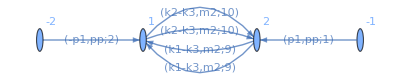

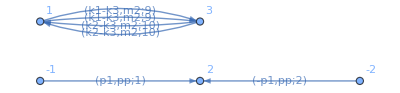

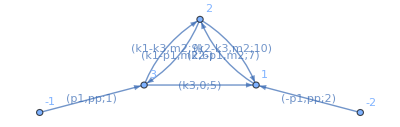

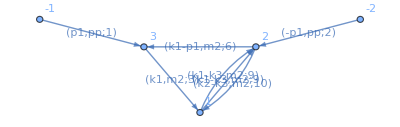

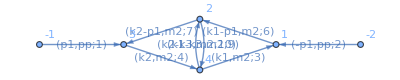

```mathematica
Import["./graphs/topoB/all/topoB_4_202.dot"]
Import["./graphs/topoB/all/topoB_4_195.dot"]
Import["./graphs/topoB/all/topoB_5_220.dot"]
Import["./graphs/topoB/all/topoB_5_203.dot"]
Import["./graphs/topoB/all/topoB_6_219.dot"]
```

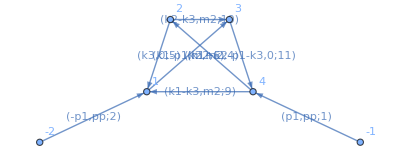

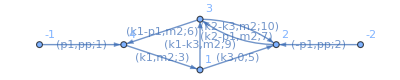

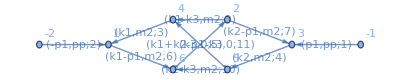

```mathematica
(*d = 4 ? *)
Import["./graphs/topoB/all/topoB_6_462.dot"]
Import["./graphs/topoB/all/topoB_6_221.dot"]
Import["./graphs/topoB/all/topoB_8_479.dot"]
```

### Build Basis start working in d = 2

```mathematica
remainingMastersInfo[[;;3,2]]
```

{topoB[-2,1,0,1,0,0,1,1,0],topoB[0,1,-2,1,0,0,1,1,0],topoB[0,1,0,1,0,0,1,1,0]}

```mathematica
Derivate[elem_,s_]:=Module[{},Collect[Collect[Collect[elem, {_INT}, D[#,s]&] /.m2->1 , _INT, Factor]  +(( elem /. INT[a__] -> der[INT[a],s])(* /. DEQ[s]*) /. m2->1), _INT, Factor]]
```

```mathematica
basisDone= {(d-2)j[famA,0,0,0,1,1,1,0,0,0], (* tadpole ^ 3    t = 3*)
 (-5+2 d)m2 j[famA,0,0,0,0,1,1,1,1,0], (* sunrise with two masses and no momentum  t = 4 *)
(* three MI sunrise*)
(d-2) √(4m2-pp) √pp j[famA,0,0,1,0,1,0,1,1,0], (* banana with 2 equal masses  t = 3 *)
(d-2) j[famA,0,0,1,-1,1,0,1,1,0],
(d-2) j[famA,0,0,1,0,1,-1,1,1,0],
(* *)
(d-2)  j[famA,0,-1,1,1,1,0,0,0,1], (* 2 sunrise with one mass * tadpole     t = 4 *)
(d-2)Sqrt[pp] √(4 m2-pp) j[famA,0,0,1,1,1,0,0,0,1], (* 2 sunrise with one mass * tadpole   t = 4 *)
(* *)
(d-2)√pp √(4 m2-pp) j[famA,0,0,1,1,1,1,0,0,0], (* tadpole^2 * bubble   t = 4 *)
(* *)
(d-2) √(4m2-pp) √pp j[famA,0,0,1,-1,1,1,1,1,0]} /. {j[famA,a__]:> INT[topoA, a],j[topoB,a__]:> INT[topoB, a]}
basisNew ={ m2 j[topoB,1,1,0,0,0,0,1,1,0] (* three loop tadpole *)
}
```

{(-2+d) INT[topoA,0,0,0,1,1,1,0,0,0],(-5+2 d) m2 INT[topoA,0,0,0,0,1,1,1,1,0],(-2+d) √(4 m2-pp) √pp INT[topoA,0,0,1,0,1,0,1,1,0],(-2+d) INT[topoA,0,0,1,-1,1,0,1,1,0],(-2+d) INT[topoA,0,0,1,0,1,-1,1,1,0],(-2+d) INT[topoA,0,-1,1,1,1,0,0,0,1],(-2+d) √(4 m2-pp) √pp INT[topoA,0,0,1,1,1,0,0,0,1],(-2+d) √(4 m2-pp) √pp INT[topoA,0,0,1,1,1,1,0,0,0],(-2+d) √(4 m2-pp) √pp INT[topoA,0,0,1,-1,1,1,1,1,0]}

{m2 j[topoB,1,1,0,0,0,0,1,1,0]}

```mathematica
nDone = Length[basisDone];
nNew = Length[basisNew];
basisToDiff= Join[basisDone, basisNew] /. {j[famA,a__]:> INT[topoA, a],j[topoB,a__]:> INT[topoB, a]};
```

```mathematica
basisDone[[;;5]] /. INT[topoA, a__]:> j[topoA,a]
```

{(-2+d) j[topoA,0,0,0,1,1,1,0,0,0],(-5+2 d) m2 j[topoA,0,0,0,0,1,1,1,1,0],(-2+d) √(4 m2-pp) √pp j[topoA,0,0,1,0,1,0,1,1,0],(-2+d) j[topoA,0,0,1,-1,1,0,1,1,0],(-2+d) j[topoA,0,0,1,0,1,-1,1,1,0]}

{(-2+d) INT[topoA,0,0,0,1,1,1,0,0,0],(-5+2 d) m2 INT[topoA,0,0,0,0,1,1,1,1,0],(-2+d) √(4 m2-pp) √pp INT[topoA,0,0,1,0,1,0,1,1,0],(-2+d) INT[topoA,0,0,1,-1,1,0,1,1,0],(-2+d) INT[topoA,0,0,1,0,1,-1,1,1,0],(-2+d) INT[topoA,0,-1,1,1,1,0,0,0,1],(-2+d) √(4 m2-pp) √pp INT[topoA,0,0,1,1,1,0,0,0,1],(-2+d) √(4 m2-pp) √pp INT[topoA,0,0,1,1,1,1,0,0,0],(-2+d) √(4 m2-pp) √pp INT[topoA,0,0,1,-1,1,1,1,1,0]}

```mathematica
derUnred=(Derivate[basisToDiff,pp]//Simplify) /. √(-((-4+pp) pp))->Sqrt[(4 -pp)] Sqrt[pp] /. 1/ √(-((-4+pp) pp)) -> Sqrt[(4 -pp)] Sqrt[pp] /(4 -pp)/pp;
(* Collect integrals to diff *)
todiff=Join[Union@Cases[derUnred, _INT,∞],Union@Cases[basisToDiff, _INT,∞]];
Close["./todiff.inc"]
Do[WriteLine["todiff.inc",todiff[[i]]], {i,1,Length[todiff]}];
(* take derivative from reduze*)
deq=Import["./DEQ/deq.m"]/. {INT["topoA",a__,{bin__}]:> INT[topoA, bin],INT["topoB",a__,{bin__}]:> INT[topoB, bin]};
derUnred=Collect[derUnred /. deq, {_INT} ,Factor];
(* Collect integrals to reduze *)
toreduce=Join[Union@Cases[derUnred, _INT,∞],Union@Cases[basisToDiff, _INT,∞]];
Close["./to_reduce.inc"]
Do[WriteLine["to_reduce.inc",todiff[[i]]], {i,1,Length[todiff]}];
```

General::openx: ./todiff.inc is not open.

Close[./todiff.inc]

General::openx: ./to_reduce.inc is not open.

Close[./to_reduce.inc]

```mathematica
derUnred[[1]]
```

(-2+d) der[INT[topoA,0,0,0,1,1,1,0,0,0],pp]

```mathematica
(* Import reduction from reduze*)
red=Import["./reductions/reduction.m"] /. {INT["topoA",a__,{bin__}]:> INT[topoA, bin],INT["topoB",a__,{bin__}]:> INT[topoB, bin]};
```

```mathematica
basisRed=Collect[basisToDiff /. red, {_INT}, Factor];
mis= Union@Cases[basisRed, _INT,∞]
Length[mis]
Length[basisRed]
(* basisRed = matBasis . mis *)
matBasis=CoefficientArrays[basisRed,mis][[2]]//Normal;
```

{INT[topoA,0,0,1,0,1,0,1,1,0],INT[topoA,0,0,1,0,1,0,2,1,0],INT[topoA,0,0,2,0,1,0,1,1,0],INT[topoA,0,1,1,0,0,0,1,1,0],INT[topoA,0,1,1,0,1,0,1,1,0],INT[topoA,0,1,1,1,0,0,1,0,0],INT[topoA,0,2,1,1,0,0,1,0,0],INT[topoA,1,1,1,0,0,0,0,0,0],INT[topoA,1,1,1,1,0,0,0,0,0],INT[topoB,1,1,0,0,0,0,1,1,0]}

10

10

```mathematica
(* reduze RHS*)
derRed=Collect[derUnred /.red, {_INT},Simplify] /. √(-((-4+pp) pp))->Sqrt[(4 -pp)] Sqrt[pp] /. 1/ √(-((-4+pp) pp)) -> Sqrt[(4 -pp)] Sqrt[pp] /(4 -pp)/pp;
test=Union@Cases[derRed[[;;]], _INT,∞];
Complement[test,mis]
```

{}

#### elliptic sector

```mathematica
SetDim[d];
Declare[
{p,k1,k2,k3},Vector,
{pp,m2},Number];
(* kinematics *)
q=-p;
sp[p,p]=pp;
```

```mathematica
family2 = topoB;
intfam2  = {-m2+sp[k1,k1],-m2+sp[k2,k2],sp[k3,k3],-m2+sp[k1,k1]-2 sp[k1,p]+sp[p,p],-m2+sp[k2,k2]-2 sp[k2,p]+sp[p,p],sp[k3,k3]-2 sp[k3,p]+sp[p,p],sp[k1,k1]-2 sp[k1,k3]+sp[k3,k3]-m2,sp[k2,k2]-2 sp[k2,k3]+sp[k3,k3]-m2,pp+sp[k1,k1]+sp[k1,k2]-sp[k1,k3]-sp[k1,p]+sp[k2,k1]+sp[k2,k2]-sp[k2,k3]-sp[k2,p]-sp[k3,k1]-sp[k3,k2]+sp[k3,k3]+sp[k3,p]-sp[p,k1]-sp[p,k2]+sp[p,k3]}
(*Initialize integral family*)(*--------------------------------------------------------------*)NewDsBasis[family2,intfam2,{k1,k2,k3},Directory->"topoB"]

GenerateIBP[family2];

AnalyzeSectors[family2];

FindSymmetries[family2];

(*(*Solve IBP reduction for unique sectors*)
(*--------------------------------------------------------------*)
SolvejSector[js[topoB,0,1,0,1,0,0,1,1,0]];
(*Save to disk*)
DiskSave[family2];*)
```

{-m2+k1·k1,-m2+k2·k2,k3·k3,-m2+pp+k1·k1-2 k1·p,-m2+pp+k2·k2-2 k2·p,pp+k3·k3-2 k3·p,-m2+k1·k1-2 k1·k3+k3·k3,-m2+k2·k2-2 k2·k3+k3·k3,pp+k1·k1+2 k1·k2-2 k1·k3-2 k1·p+k2·k2-2 k2·k3-2 k2·p+k3·k3+2 k3·p}

topoB is valid basis. The definitions of the basis will be saved in "topoB" directory.
    Ds[topoB] — denominators,
    SPs[topoB] — scalar products involving loop momenta,
    LMs[topoB] — loop momenta,
    EMs[topoB] — external momenta,
    Parameters[topoB] — parameters (invariants, masses, dimension),
    Toj[topoB] — rules to transform scalar products to denominators,
    CutDs[topoB] — flag vector of cut denominators.

topoB

Identities are generated.
    IBP[topoB] — integration-by-part identities,
    LI[topoB] — Lorentz invariance identities.

Found 196(316) zero(nonzero) sectors out of 512.
    ZeroSectors[topoB] — zero sectors,
    NonZeroSectors[topoB] — nonzero sectors,
    SimpleSectors[topoB] — simple sectors (no nonzero subsectors),
    BasisSectors[topoB] — basis sectors (at least one immediate subsector is zero),
    ZerojRule[topoB] — a rule to nullify all zero j[topoB…],
    CutDs[topoB] — a flag list of cut denominators (1=cut).

Found 236 mapped sectors and 80 unique sectors.
    UniqueSectors[topoB] — unique sectors.
    MappedSectors[topoB] — mapped sectors.
    SR[topoB][…] — symmetry relations for j[topoB,…] from UniqueSectors[topoB].
    jSymmetries[topoB,…] — symmetry rules for the sector js[topoB,…] in UniqueSectors[topoB].
    jRules[topoB,…] — reduction rules for j[topoB,…] from MappedSectors[topoB].
    SectorsMappings[topoB] gives the list of mappings of all sectors from MappedSectors[topoB] to UniqueSectors[topoB].

```mathematica
corner=j[topoB,0,1,0,1,0,0,1,1,0];
der1=Dinv[j[topoB,0,1,0,1,0,0,1,1,0],pp];
der2 = Dinv[der1,pp];
derder2 = Dinv[der2,pp];
```

```mathematica
Join[Cases[der1, _j,∞],Cases[der2, _j,∞],Cases[corner, _j,∞],Cases[derder2,_j,∞]]//Union
```

{j[topoB,-3,1,0,4,0,0,1,1,0],j[topoB,-2,1,0,3,0,0,1,1,0],j[topoB,-2,1,0,4,0,0,1,1,0],j[topoB,-1,1,0,2,0,0,1,1,0],j[topoB,-1,1,0,3,0,0,1,1,0],j[topoB,-1,1,0,4,0,0,1,1,0],j[topoB,0,1,0,1,0,0,1,1,0],j[topoB,0,1,0,2,0,0,1,1,0],j[topoB,0,1,0,3,0,0,1,1,0],j[topoB,0,1,0,4,0,0,1,1,0]}

```mathematica
homogBasis = {corner, der1, der2};
```

```mathematica
RedPF=Import["./reductions/reduction_PF.m"] /. {INT["topoA",a__,{bin__}]:> INT[topoA, bin],INT["topoB",a__,{bin__}]:> INT[topoB, bin]}/. INT[fam_,a__]:> j[fam,a];
```

```mathematica
Union@Cases[RedPF[[;;,2]],_j,∞]
```

{j[topoA,1,1,1,0,0,0,0,0,0],j[topoB,0,1,0,1,0,0,1,1,0],j[topoB,0,2,0,1,0,0,1,1,0],j[topoB,0,3,0,1,0,0,1,1,0]}

```mathematica
derder2RED=Collect[derder2 /. RedPF /. m2 -> 1, {_j},Factor];
```

```mathematica
inversion=Flatten[Solve[Thread[Equal[{mas1,mas2,mas3},Collect[homogBasis /. RedPF/.j[topoA,1,1,1,0,0,0,0,0,0]->0/.m2-> 1, {_j},Factor]]],{j[topoB,0,1,0,1,0,0,1,1,0],j[topoB,0,2,0,1,0,0,1,1,0],j[topoB,0,3,0,1,0,0,1,1,0]}]];
```

```mathematica
Collect[derder2RED //. inversion /. d-> 2//Simplify, {mas1,mas2,mas3}]
```

(mas1 (4-pp))/((-16+pp) (-4+pp) pp^2)+(mas2 (-64+68 pp-7 pp^2))/((-16+pp) (-4+pp) pp^2)-(6 mas3 (32-15 pp+pp^2))/((-16+pp) (-4+pp) pp)

```mathematica
HGM0
```

HGM0

```mathematica
HGM0 = {{0,1,0}, {0,0,1}, CoefficientArrays[Collect[derder2RED //. inversion /. d-> 2//Simplify, {mas1,mas2,mas3}],{mas1,mas2,mas3}][[2]]//Normal};
```

```mathematica
dddPeriods = Collect[derder2RED //. inversion /. d-> 2//Simplify, {mas1,mas2,mas3}] /. {mas1 -> period,mas2-> Dperiod,mas3 -> DDperiod}
```

(period (4-pp))/((-16+pp) (-4+pp) pp^2)+(Dperiod (-64+68 pp-7 pp^2))/((-16+pp) (-4+pp) pp^2)-(6 DDperiod (32-15 pp+pp^2))/((-16+pp) (-4+pp) pp)

```mathematica
(* third derivative MI = ..*)
PF=Collect[1/pp^3 (θ^3 -3 θ^2 +2   θ)-Collect[derder2RED //. inversion /. d-> 2//Simplify, {mas1,mas2,mas3}] /. {  mas2 -> 1/pp θ, mas3 -> 1/pp^2(θ^2-θ) , d3MI -> 1/pp^3 (θ^3 -3 θ^2 +2   θ)}/.mas1-> 1/. pp -> λ//Simplify, {θ}, Simplify]
```

θ^3/λ^3+1/((-16+λ) λ^2)+(3 θ^2 (-10+λ))/((-16+λ) (-4+λ) λ^2)+(3 θ (-6+λ))/((-16+λ) (-4+λ) λ^2)

```mathematica
(* θ^3/λ^3+1/((-16+λ) λ^2)+(3 θ^2 (-10+λ))/((-16+λ) (-4+λ) λ^2)+(3 θ (-6+λ))/((-16+λ) (-4+λ) λ^2) correct, checked with Felix and Christoph *)
```

```mathematica
(* this is the derivative operator in lambada = m2 *)
OP =Collect[(-  Collect[λ^3(-16+λ) (-4+λ)  PF , {θ},Together] /.{θ^3-> F[θ,θ,θ], θ θ-> F[θ,θ] ,  θ-> F[θ]}  //Expand) , _F, Factor]
(* generically, if we want to shift λ = λ0 + ρ and expand around ρ ~ 0 (λ ~ λ0), the transformation is the following *)
OPlambda0 =Collect[ Collect[OP   /. {F[θ] -> F[θ] (1 + λ0/ρ) ,F[θ,θ] ->((λ0+ρ) (-λ0 F[θ]+(λ0+ρ) F[θ,θ]))/ρ^2, λ  -> λ0 +ρ }, {_F}, Simplify], {_F} ,Simplify];
(* choose here a point *)
toapply=(OPlambda0/. λ0 ->0/. F -> F1)//Simplify//Expand
(* indicial equation*)
Print["indicial equation:  ",( toapply /. ρ ->  0) == 0 ]
(* indices 0 *)
```

-((-4+λ) λ)-3 (-6+λ) λ F[θ]-3 (-10+λ) λ F[θ,θ]-(-16+λ) (-4+λ) F[θ,θ,θ]

4 ρ-ρ^2+18 ρ F1[θ]-3 ρ^2 F1[θ]+30 ρ F1[θ,θ]-3 ρ^2 F1[θ,θ]-64 F1[θ,θ,θ]+20 ρ F1[θ,θ,θ]-ρ^2 F1[θ,θ,θ]

indicial equation:  -64 F1[θ,θ,θ]==0

```mathematica
(* combine string of operators. F1 will be in the operator, F2 in the ansatz *)
combineOperator = { F1[a__]F2[b__] :> F[a,b], F1[a__]-> F[a] , F2[a__] -> F[a] };
(* move the θ operator to the right for polynomial and logs *)
moveRightPoly = {F[a___,θ, g[ρ,m_],b___]->  m F[a,g[ρ,m],b]  + F[a,g[ρ,m], θ,b]};
moveRightLog = {F[a___,θ, g[log,1],b___]->  F[a,b]  + F[a,g[log,1], θ,b],F[a___,θ, g[log,2],b___]  -> 2  F[a,g[log,1],b]  + F[a,g[log,2], θ,b]};
(* extract from the functions the logs and the polynomial *)
extractPoly = { F[g[ρ,m_],b___] -> ρ^m F[b], F[g[log,1],g[ρ,m_],b___] -> ρ^m log F[b], F[g[log,2],g[ρ,m_],b___] -> ρ^m log^2 F[b]  };
extractPolySol = { F2[g[ρ,m_]] -> ρ^m , F2[g[log,n_],g[ρ,m_]] -> ρ^m L^n };
(* Once the operator is completely to the right, it annihilates nothing *)
zeroOP = {F[θ]->0,F[θ,θ]->0,F[θ,θ,θ]->0,F[θ,θ,θ]->0,F[θ,θ,θ,θ]->0,F[θ,θ,θ,θ,θ]->0};
SolveForAnsatzMUM[point_, maxorder_, indicial_, operator_] := Module[{ansatz, sol0, sol1,coeffSol,der,derpoly,derpolyLog,tmp},
(*first solution*)
ansatz = Sum[a[n]F2[g[ρ,n+indicial]], {n,0,maxorder}];
(*boundary*)
coeffSol={a[0]-> 1};
(* Apply operator to ansatz *)
der=Expand[operator ansatz] //. combineOperator  //.moveRightPoly //.extractPoly /. F[]->1  /. zeroOP;
Do[
tmp=Flatten[Solve[(Coefficient[der,ρ,i+indicial]/.coeffSol) ==0]];
coeffSol = Join[coeffSol,tmp], {i,1,maxorder}];
sol0 = Sum[a[n]F2[g[ρ,n+indicial]], {n,0,maxorder}] /. coeffSol;
Clear[ansatz];
(*second solution*)
ansatz =Sum[a[n] F2[g[log,1], g[ρ,n+indicial]], {n,0,maxorder}]+ Sum[b[n]F2[g[ρ,n+indicial]], {n,1,maxorder}];
(*boundary*)
der=Expand[operator ansatz] //. combineOperator  //.moveRightLog //. moveRightPoly//.extractPoly /. F[]->1  /. zeroOP;
derpoly=Coefficient[der,log,0];
derpolyLog=Coefficient[der,log,1];
Do[
tmp=Flatten[Solve[(Coefficient[derpoly,ρ,i+indicial]/.coeffSol) ==0]];
coeffSol = Join[coeffSol,tmp], {i,1,maxorder}];
sol1 =Sum[a[n] F2[g[log,1], g[ρ,n+indicial]], {n,0,maxorder}]+ Sum[b[n]F2[g[ρ,n+indicial]], {n,1,maxorder}]/. coeffSol;
Return[{sol0,sol1, coeffSol}];
]
```

```mathematica
SolveForAnsatzMUM3[point_, maxorder_, indicial_, operator_] := Module[{ansatz, sol0, sol1,sol2,coeffSol,der,derpoly,derpolyLog,derpolyLogLog,tmp},
(*first solution*)
ansatz = Sum[a[n]F2[g[ρ,n+indicial]], {n,0,maxorder}];
(*boundary*)
coeffSol={a[0]-> 1};
(* Apply operator to ansatz *)
der=Expand[operator ansatz] //. combineOperator  //.moveRightPoly //.extractPoly /. F[]->1  /. zeroOP;
Do[
tmp=Flatten[Solve[(Coefficient[der,ρ,i+indicial]/.coeffSol) ==0]];
coeffSol = Join[coeffSol,tmp], {i,1,maxorder}];
sol0 = Sum[a[n]F2[g[ρ,n+indicial]], {n,0,maxorder}] /. coeffSol;
Clear[ansatz];
(*second solution*)
ansatz =Sum[a[n] F2[g[log,1], g[ρ,n+indicial]], {n,0,maxorder}]+
 Sum[b[n]F2[g[ρ,n+indicial]], {n,1,maxorder}];
(*boundary*)
der=Expand[operator ansatz] //. combineOperator  //.moveRightLog //. moveRightPoly//.extractPoly /. F[]->1  /. zeroOP;
derpoly=Coefficient[der,log,0];
derpolyLog=Coefficient[der,log,1];
Do[
tmp=Flatten[Solve[(Coefficient[derpoly,ρ,i+indicial]/.coeffSol) ==0]];
coeffSol = Join[coeffSol,tmp], {i,1,maxorder}];
sol1 =Sum[a[n] F2[g[log,1], g[ρ,n+indicial]], {n,0,maxorder}]+ Sum[b[n]F2[g[ρ,n+indicial]], {n,1,maxorder}]/. coeffSol;
(*third solution*)
ansatz =Sum[a[n] F2[g[log,2], g[ρ,n+indicial]]/2, {n,0,maxorder}]+ 
Sum[b[n]F2[g[log,1],g[ρ,n+indicial]], {n,1,maxorder}]+
Sum[c[n]F2[g[ρ,n+indicial]], {n,2,maxorder}] ; 
(*boundary*)
der=Expand[operator ansatz] //. combineOperator  //.moveRightLog //. moveRightPoly//.extractPoly /. F[]->1  /. zeroOP;
derpoly=Coefficient[der,log,0];
derpolyLog=Coefficient[der,log,1];
derpolyLogLog=Coefficient[der,log,2];
Do[
tmp=Flatten[Solve[(Coefficient[derpoly,ρ,i+indicial]/.coeffSol) ==0]];
(*Print[{Coefficient[derpoly,ρ,i+indicial],Coefficient[derpoly,ρ,i+indicial]/.coeffSol}];*)
coeffSol = Join[coeffSol,tmp], {i,2,maxorder}];
sol2 =Sum[a[n] F2[g[log,2], g[ρ,n+indicial]]/2, {n,0,maxorder}]+
 Sum[b[n]F2[g[log,1],g[ρ,n+indicial]], {n,1,maxorder}]+
Sum[c[n]F2[g[ρ,n+indicial]], {n,2,maxorder}] /. coeffSol;
Return[{sol0,sol1,sol2, coeffSol}];
]
```

```mathematica
point = 0;
maxorder=100
{sol[point][0],sol[point][1],sol[point][2], coeffSol[point]}=SolveForAnsatzMUM3[0,maxorder,0,toapply];
```

100

```mathematica
(* checked with Forner - Nega *)
s1 /. extractPolySol /. ρ^b_ /; b > 4 ->0
s2 /. extractPolySol /. ρ^b_ /; b > 4 ->0 /. L -> 0
s3 /. extractPolySol /. ρ^b_ /; b > 4 ->0 /.L-> 0
```

s1

s2

s3

```mathematica
(*Export["./PERIODS/omega012.m",{ω0[ρ]->sol[point][0]/.extractPolySol,ω1[ρ]->sol[point][1]/.extractPolySol,ω2[ρ]->sol[point][2]/.extractPolySol, coeffSol[point]}]
Export["./PERIODS/Domega0.m",{D[ω0[ρ],ρ]-> D[sol[point][0]/.extractPolySol,ρ]}]
Export["./PERIODS/DDomega0.m",{D[D[ω0[ρ],ρ],ρ]-> D[D[sol[point][0]/.extractPolySol,ρ],ρ]}]*)
```

```mathematica
(* check the solution up to the requested order *)
(Series[Expand[toapply sol[point][0]]  //. combineOperator  //.moveRightLog //. moveRightPoly//.extractPoly /. F[]->1  /. zeroOP, {ρ,0,maxorder-1}]//Normal) /. ρ^(a_)/; a> 99 :> 0
(Series[Expand[toapply sol[point][1]]  //. combineOperator  //.moveRightLog //. moveRightPoly//.extractPoly /. F[]->1  /. zeroOP//Expand, 
{ρ,0,maxorder-1}]//Normal)/. ρ^(a_)/; a> 99 :> 0
(Series[Expand[toapply sol[point][2]]  //. combineOperator //.moveRightLog //. moveRightPoly//.extractPoly /. F[]->1  /. zeroOP//Expand, {ρ,0,maxorder-1}]//Normal)/. ρ^(a_)/; a> 99 :> 0
```

0

0

0

```mathematica
(* Griffiths transversality condition (don't remember where they come from) *)
Σ = {{0,0,1},{0,-1,0}, {1,0,0}}
Print[{ω0,ω1,ω2}.Σ.{ω0,ω1,ω2}]
```

{{0,0,1},{0,-1,0},{1,0,0}}

-ω1^2+2 ω0 ω2

```mathematica
(*(* entry (1,1) *)
Collect[{ω0,ω1,ω2}.Σ.{ω0,ω1,ω2} /. {ω0 -> sol[point][0]/.extractPolySol,ω1 -> sol[point][1]/.extractPolySol,ω2 -> sol[point][2]/.extractPolySol} , {L,ρ}]  /. ρ^n_/; n> 40 -> 0
(* entry (1,2) *)
Collect[{ω0,ω1,ω2}.Σ.{dω0,dω1,dω2} /. {ω0 -> sol[point][0]/.extractPolySol,ω1 -> sol[point][1]/.extractPolySol,ω2 -> sol[point][2]/.extractPolySol} /.{ dω0 -> D[((sol[point][0]//Expand) //.combineOperator//.moveRightLog //. moveRightPoly//.extractPoly /. F[]->1  /. zeroOP /. log -> L)/.L-> Log[ρ],ρ] /. Log[ρ]->L,dω1 -> D[((sol[point][1]//Expand) //.combineOperator//.moveRightLog //. moveRightPoly//.extractPoly /. F[]->1  /. zeroOP /. log -> L)/.L-> Log[ρ],ρ] /. Log[ρ]->L,dω2 -> D[((sol[point][2]//Expand) //.combineOperator//.moveRightLog //. moveRightPoly//.extractPoly /. F[]->1  /. zeroOP /. log -> L)/.L-> Log[ρ],ρ] /. Log[ρ]->L}  , {L,ρ}] /. ρ^n_/; n> maxorder-1 -> 0
(* entry (1,3) = (3,1) *)
Collect[{ω0,ω1,ω2}.Σ.{ddω0,ddω1,ddω2} /. {ω0 -> sol[point][0]/.extractPolySol,ω1 -> sol[point][1]/.extractPolySol,ω2 -> sol[point][2]/.extractPolySol} /.{ ddω0 -> D[D[((sol[point][0]//Expand) //.combineOperator//.moveRightLog //. moveRightPoly//.extractPoly /. F[]->1  /. zeroOP /. log -> L)/.L-> Log[ρ],ρ],ρ] /. Log[ρ]->L,ddω1 ->D[ D[((sol[point][1]//Expand) //.combineOperator//.moveRightLog //. moveRightPoly//.extractPoly /. F[]->1  /. zeroOP /. log -> L)/.L-> Log[ρ],ρ] ,ρ]/. Log[ρ]->L,ddω2 -> D[D[((sol[point][2]//Expand) //.combineOperator//.moveRightLog //. moveRightPoly//.extractPoly /. F[]->1  /. zeroOP /. log -> L)/.L-> Log[ρ],ρ],ρ] /. Log[ρ]->L}  , {L,ρ}] /. ρ^n_/; n> 5-1 -> 0;
Series[(n[0]+n[1]ρ + n[2]ρ^2 + n[3] ρ^3)/((-16+ ρ)(-4+ρ)ρ^2)/.{n[0]->64, n[1]-> 0,n[2]->0,n[3]-> 0}, {ρ,0,3}];
(n[0]+n[1]ρ + n[2]ρ^2 + n[3] ρ^3)/((-16+ ρ)(-4+ρ)ρ^2)/.{n[0]->64, n[1]-> 0,n[2]->0,n[3]-> 0}
(* entry (2,3) = (3,2) *)
Collect[{dω0,dω1,dω2}.Σ.{ddω0,ddω1,ddω2} /. {ω0 -> sol[point][0]/.extractPolySol,ω1 -> sol[point][1]/.extractPolySol,ω2 -> sol[point][2]/.extractPolySol} /.{ ddω0 -> D[D[((sol[point][0]//Expand) //.combineOperator//.moveRightLog //. moveRightPoly//.extractPoly /. F[]->1  /. zeroOP /. log -> L)/.L-> Log[ρ],ρ],ρ] /. Log[ρ]->L,ddω1 ->D[ D[((sol[point][1]//Expand) //.combineOperator//.moveRightLog //. moveRightPoly//.extractPoly /. F[]->1  /. zeroOP /. log -> L)/.L-> Log[ρ],ρ] ,ρ]/. Log[ρ]->L,ddω2 -> D[D[((sol[point][2]//Expand) //.combineOperator//.moveRightLog //. moveRightPoly//.extractPoly /. F[]->1  /. zeroOP /. log -> L)/.L-> Log[ρ],ρ],ρ] /. Log[ρ]->L} /.{ dω0 -> D[((sol[point][0]//Expand) //.combineOperator//.moveRightLog //. moveRightPoly//.extractPoly /. F[]->1  /. zeroOP /. log -> L)/.L-> Log[ρ],ρ] /. Log[ρ]->L,dω1 -> D[((sol[point][1]//Expand) //.combineOperator//.moveRightLog //. moveRightPoly//.extractPoly /. F[]->1  /. zeroOP /. log -> L)/.L-> Log[ρ],ρ] /. Log[ρ]->L,dω2 -> D[((sol[point][2]//Expand) //.combineOperator//.moveRightLog //. moveRightPoly//.extractPoly /. F[]->1  /. zeroOP /. log -> L)/.L-> Log[ρ],ρ] /. Log[ρ]->L}  , {L,ρ}] /. ρ^n_/; n> 12-1 -> 0;
Series[% ((ρ^3)(ρ-4)^2(ρ-16)^2 ), {ρ,0,10} ];
Collect[Series[(n[0]+n[1]ρ + n[2]ρ^2 )/((ρ^3)(ρ-4)^2(ρ-16)^2 )/.{n[0]->4096,n[1]->-1920,n[2] ->128}, {ρ,0,4}],ρ];
(n[0]+n[1]ρ + n[2]ρ^2 )/((ρ^3)(ρ-4)^2(ρ-16)^2 )/.{n[0]->4096,n[1]->-1920,n[2] ->128}//FullSimplify;
(* entry (2,2) = (2,2) *)
Collect[{dω0,dω1,dω2}.Σ.{dω0,dω1,dω2} /. {ω0 -> sol[point][0]/.extractPolySol,ω1 -> sol[point][1]/.extractPolySol,ω2 -> sol[point][2]/.extractPolySol} /.{ ddω0 -> D[D[((sol[point][0]//Expand) //.combineOperator//.moveRightLog //. moveRightPoly//.extractPoly /. F[]->1  /. zeroOP /. log -> L)/.L-> Log[ρ],ρ],ρ] /. Log[ρ]->L,ddω1 ->D[ D[((sol[point][1]//Expand) //.combineOperator//.moveRightLog //. moveRightPoly//.extractPoly /. F[]->1  /. zeroOP /. log -> L)/.L-> Log[ρ],ρ] ,ρ]/. Log[ρ]->L,ddω2 -> D[D[((sol[point][2]//Expand) //.combineOperator//.moveRightLog //. moveRightPoly//.extractPoly /. F[]->1  /. zeroOP /. log -> L)/.L-> Log[ρ],ρ],ρ] /. Log[ρ]->L} /.{ dω0 -> D[((sol[point][0]//Expand) //.combineOperator//.moveRightLog //. moveRightPoly//.extractPoly /. F[]->1  /. zeroOP /. log -> L)/.L-> Log[ρ],ρ] /. Log[ρ]->L,dω1 -> D[((sol[point][1]//Expand) //.combineOperator//.moveRightLog //. moveRightPoly//.extractPoly /. F[]->1  /. zeroOP /. log -> L)/.L-> Log[ρ],ρ] /. Log[ρ]->L,dω2 -> D[((sol[point][2]//Expand) //.combineOperator//.moveRightLog //. moveRightPoly//.extractPoly /. F[]->1  /. zeroOP /. log -> L)/.L-> Log[ρ],ρ] /. Log[ρ]->L}  , {L,ρ}] /. ρ^n_/; n> 12-1 -> 0;
Series[% ((ρ^3)(ρ-4)(ρ-16) ), {ρ,0,10} ];
Collect[Series[(n[0]+n[1]ρ + n[2]ρ^2 )/((ρ^3)(ρ-4)(ρ-16) )/.{n[0]->0,n[1]->-64,n[2]-> 0}, {ρ,0,4}],ρ];
(n[0]+n[1]ρ + n[2]ρ^2 )/((ρ^3)(ρ-4)(ρ-16) )/.{n[0]->0,n[1]->-64,n[2]-> 0}//FullSimplify;
(* entry (3,3) = (3,3) *)
Collect[{ddω0,ddω1,ddω2}.Σ.{ddω0,ddω1,ddω2} /. {ω0 -> sol[point][0]/.extractPolySol,ω1 -> sol[point][1]/.extractPolySol,ω2 -> sol[point][2]/.extractPolySol} /.{ ddω0 -> D[D[((sol[point][0]//Expand) //.combineOperator//.moveRightLog //. moveRightPoly//.extractPoly /. F[]->1  /. zeroOP /. log -> L)/.L-> Log[ρ],ρ],ρ] /. Log[ρ]->L,ddω1 ->D[ D[((sol[point][1]//Expand) //.combineOperator//.moveRightLog //. moveRightPoly//.extractPoly /. F[]->1  /. zeroOP /. log -> L)/.L-> Log[ρ],ρ] ,ρ]/. Log[ρ]->L,ddω2 -> D[D[((sol[point][2]//Expand) //.combineOperator//.moveRightLog //. moveRightPoly//.extractPoly /. F[]->1  /. zeroOP /. log -> L)/.L-> Log[ρ],ρ],ρ] /. Log[ρ]->L} /.{ dω0 -> D[((sol[point][0]//Expand) //.combineOperator//.moveRightLog //. moveRightPoly//.extractPoly /. F[]->1  /. zeroOP /. log -> L)/.L-> Log[ρ],ρ] /. Log[ρ]->L,dω1 -> D[((sol[point][1]//Expand) //.combineOperator//.moveRightLog //. moveRightPoly//.extractPoly /. F[]->1  /. zeroOP /. log -> L)/.L-> Log[ρ],ρ] /. Log[ρ]->L,dω2 -> D[((sol[point][2]//Expand) //.combineOperator//.moveRightLog //. moveRightPoly//.extractPoly /. F[]->1  /. zeroOP /. log -> L)/.L-> Log[ρ],ρ] /. Log[ρ]->L}  , {L,ρ}] /. ρ^n_/; n> 12-1 -> 0;
Series[% ((ρ^4)(ρ-4)^3(ρ-16)^3 ), {ρ,0,10} ]
Collect[Series[(n[0]+n[1]ρ + n[2]ρ^2 )/((ρ^3)(ρ-4)(ρ-16) )/.{n[0]->0,n[1]->-64,n[2]-> 0}, {ρ,0,4}],ρ];
-(64 (4096+ρ (-4352+ρ (1380+ρ (-148+5 ρ)))))/((-16+ρ)^3 (-4+ρ)^3 ρ^4);*)
```

```mathematica
Z= {{0,0,64/((-16+ρ) (-4+ρ) ρ^2)},{0,-64/(ρ^2 (64-20 ρ+ρ^2)),(128 (32+(-15+ρ) ρ))/((-16+ρ)^2 (-4+ρ)^2 ρ^3)},{64/((-16+ρ) (-4+ρ) ρ^2),(128 (32+(-15+ρ) ρ))/((-16+ρ)^2 (-4+ρ)^2 ρ^3),-(64 (4096+ρ (-4352+ρ (1380+ρ (-148+5 ρ)))))/((-16+ρ)^3 (-4+ρ)^3 ρ^4)}};
(* Agrees with Nega - Forner *)
(*Inverse[Z]64//Simplify//MatrixForm*)
```

```mathematica
W= {{ω0,ω1,ω2},{dω0,dω1,dω2},{ddω0,ddω1,ddω2}}
```

{{ω0,ω1,ω2},{dω0,dω1,dω2},{ddω0,ddω1,ddω2}}

```mathematica
putArgument = {ω1 ->ω1[ρ],dω1 ->D[ω1[ρ],ρ],ddω1 ->D[D[ω1[ρ],ρ],ρ],ω2 ->ω2[ρ],dω2 ->D[ω2[ρ],ρ],ddω2->D[D[ω2[ρ],ρ],ρ],ω0 ->ω0[ρ],dω0 ->D[ω0[ρ],ρ],ddω0 ->D[D[ω0[ρ],ρ],ρ]};
removeArgument=putArgument /. Rule[a_,b_]:> Rule[b,a];
```

```mathematica
eqs=Thread[Equal[(Flatten[W.Σ.Transpose[W]]// Simplify),Flatten[Z]]]//Union;
eqs=eqs /. {ω1 ->ω1[ρ],dω1 ->D[ω1[ρ],ρ],ddω1 ->D[D[ω1[ρ],ρ],ρ],ω2 ->ω2[ρ],dω2 ->D[ω2[ρ],ρ],ddω2->D[D[ω2[ρ],ρ],ρ],ω0 ->ω0[ρ],dω0 ->D[ω0[ρ],ρ],ddω0 ->D[D[ω0[ρ],ρ],ρ] };
eqs //TableForm
(* the second is the derivative of the third, the fifth is the derivative of the sixth, 
the fourth and the third combine into the derivative of the fifth.  *)
```

-ω1''[ρ]^2+2 ω0''[ρ] ω2''[ρ]==-(64 (4096+ρ (-4352+ρ (1380+ρ (-148+5 ρ)))))/((-16+ρ)^3 (-4+ρ)^3 ρ^4)
ω2'[ρ] ω0''[ρ]-ω1'[ρ] ω1''[ρ]+ω0'[ρ] ω2''[ρ]==(128 (32+(-15+ρ) ρ))/((-16+ρ)^2 (-4+ρ)^2 ρ^3)
-ω1'[ρ]^2+2 ω0'[ρ] ω2'[ρ]==-64/(ρ^2 (64-20 ρ+ρ^2))
ω2[ρ] ω0''[ρ]-ω1[ρ] ω1''[ρ]+ω0[ρ] ω2''[ρ]==64/((-16+ρ) (-4+ρ) ρ^2)
ω2[ρ] ω0'[ρ]-ω1[ρ] ω1'[ρ]+ω0[ρ] ω2'[ρ]==0
-ω1[ρ]^2+2 ω0[ρ] ω2[ρ]==0

```mathematica
eqstmp=eqs /. {ω0'[ρ] -> dω0,ω1'[ρ] -> dω1,ω2'[ρ] -> dω2,ω0[ρ] -> ω0,ω1[ρ] -> ω1,ω2[ρ] -> ω2,ω1''[ρ]-> ddω1,ω2''[ρ]-> ddω2,ω0''[ρ]-> ddω0}
```

{-ddω1^2+2 ddω0 ddω2==-(64 (4096+ρ (-4352+ρ (1380+ρ (-148+5 ρ)))))/((-16+ρ)^3 (-4+ρ)^3 ρ^4),ddω2 dω0-ddω1 dω1+ddω0 dω2==(128 (32+(-15+ρ) ρ))/((-16+ρ)^2 (-4+ρ)^2 ρ^3),-dω1^2+2 dω0 dω2==-64/(ρ^2 (64-20 ρ+ρ^2)),ddω2 ω0-ddω1 ω1+ddω0 ω2==64/((-16+ρ) (-4+ρ) ρ^2),dω2 ω0-dω1 ω1+dω0 ω2==0,-ω1^2+2 ω0 ω2==0}

```mathematica
eqstmp={-ddω1^2+2 ddω0 ddω2==-(64 (4096+ρ (-4352+ρ (1380+ρ (-148+5 ρ)))))/((-16+ρ)^3 (-4+ρ)^3 ρ^4),ddω2 dω0-ddω1 dω1+ddω0 dω2==(128 (32+(-15+ρ) ρ))/((-16+ρ)^2 (-4+ρ)^2 ρ^3),-dω1^2+2 dω0 dω2==-64/(ρ^2 (64-20 ρ+ρ^2)),ddω2 ω0-ddω1 ω1+ddω0 ω2==64/((-16+ρ) (-4+ρ) ρ^2),dω2 ω0-dω1 ω1+dω0 ω2==0,-ω1^2+2 ω0 ω2==0}
```

{-ddω1^2+2 ddω0 ddω2==-(64 (4096+ρ (-4352+ρ (1380+ρ (-148+5 ρ)))))/((-16+ρ)^3 (-4+ρ)^3 ρ^4),ddω2 dω0-ddω1 dω1+ddω0 dω2==(128 (32+(-15+ρ) ρ))/((-16+ρ)^2 (-4+ρ)^2 ρ^3),-dω1^2+2 dω0 dω2==-64/(ρ^2 (64-20 ρ+ρ^2)),ddω2 ω0-ddω1 ω1+ddω0 ω2==64/((-16+ρ) (-4+ρ) ρ^2),dω2 ω0-dω1 ω1+dω0 ω2==0,-ω1^2+2 ω0 ω2==0}

```mathematica
sols=Flatten[Solve[eqstmp, {ddω0, ddω1,ddω2, dω1, dω2, ω2}]//Simplify]//PowerExpand//Simplify
```

{ddω0→(dω0^2 ρ (64-20 ρ+ρ^2)-4 dω0 (32-15 ρ+ρ^2) ω0-(-8+ρ) ω0^2)/(2 ρ (64-20 ρ+ρ^2) ω0),ddω1→1/2 ((dω0^2 ω1)/ω0^2-(4 dω0 (4 √(64-20 ρ+ρ^2)+(32-15 ρ+ρ^2) ω1))/(ρ (64-20 ρ+ρ^2) ω0)+(1024 √(64-20 ρ+ρ^2)+32 ρ^2 (√(64-20 ρ+ρ^2)-7 ω1)+28 ρ^3 ω1-ρ^4 ω1+ρ (-480 √(64-20 ρ+ρ^2)+512 ω1))/(ρ^2 (64-20 ρ+ρ^2)^2)),ddω2→1/(4 ρ^2 (64-20 ρ+ρ^2)^(3/2) ω0^3)(dω0^2 ρ^2 (64-20 ρ+ρ^2)^(3/2) ω1^2+ω0^2 (256 √(64-20 ρ+ρ^2)+64 (32-15 ρ+ρ^2) ω1-(-8+ρ) ρ √(64-20 ρ+ρ^2) ω1^2)-4 dω0 ρ ω0 ω1 (ρ^2 (8+√(64-20 ρ+ρ^2) ω1)+32 (16+√(64-20 ρ+ρ^2) ω1)-5 ρ (32+3 √(64-20 ρ+ρ^2) ω1))),dω1→-8/(ρ √(64-20 ρ+ρ^2))+(dω0 ω1)/ω0,dω2→(ω1 (-(16 ω0)/(ρ √(64-20 ρ+ρ^2))+dω0 ω1))/(2 ω0^2),ω2→ω1^2/(2 ω0),ddω0→(dω0^2 ρ (64-20 ρ+ρ^2)-4 dω0 (32-15 ρ+ρ^2) ω0-(-8+ρ) ω0^2)/(2 ρ (64-20 ρ+ρ^2) ω0),ddω1→1/2 ((dω0^2 ω1)/ω0^2+(4 dω0 (4 √(64-20 ρ+ρ^2)-(32-15 ρ+ρ^2) ω1))/(ρ (64-20 ρ+ρ^2) ω0)-(1024 √(64-20 ρ+ρ^2)-28 ρ^3 ω1+ρ^4 ω1+32 ρ^2 (√(64-20 ρ+ρ^2)+7 ω1)-32 ρ (15 √(64-20 ρ+ρ^2)+16 ω1))/(ρ^2 (64-20 ρ+ρ^2)^2)),ddω2→(dω0^2 ω1^2+(4 dω0 ω0 ω1 (8 √(64-20 ρ+ρ^2)-(32-15 ρ+ρ^2) ω1))/(ρ (64-20 ρ+ρ^2))-(ω0^2 (-256 √(64-20 ρ+ρ^2)+64 (32-15 ρ+ρ^2) ω1+(-8+ρ) ρ √(64-20 ρ+ρ^2) ω1^2))/(ρ^2 (64-20 ρ+ρ^2)^(3/2)))/(4 ω0^3),dω1→8/(ρ √(64-20 ρ+ρ^2))+(dω0 ω1)/ω0,dω2→(ω1 ((16 ω0)/(ρ √(64-20 ρ+ρ^2))+dω0 ω1))/(2 ω0^2),ω2→ω1^2/(2 ω0)}

```mathematica
sols=Flatten[Solve[eqstmp, {ddω0, ddω1,ddω2, dω1, dω2, ω2}]//Simplify]//PowerExpand//Simplify;
Collect[sols[[1]]/. Rule[a_,b_]:> a-b, {ddω0, ω0,dω0 }];
(* Relations for second derivative of omega0 *)
(*der2Omega0= ddω0->-(2 dω0 (32-15 ρ+ρ^2))/(ρ (64-20 ρ+ρ^2))+dω0^2/(2 ω0)-((-8+ρ) ω0)/(2 ρ (64-20 ρ+ρ^2))/.putArgument
Export["./PERIODS/der2Omega0.m", der2Omega0];*)
der2Omega0 = Import["./PERIODS/der2Omega0.m"];
```

```mathematica
(* Split the matrix {{ω0,ω1},{dω0,dω1}} into Unipotent and Semi-Simple *)
Wu = {{1, ω1/ω0,  1/2( ω1/ω0)^2},{0,1,  ω1/ω0}, {0,0,1}}
Wss = {{ω0,0,0},{dω0,-8/(ρ √(64-20 ρ+ρ^2)),0}, {ddω0,(16 (32+(-15+ρ) ρ))/(((-16+ρ) (-4+ρ))^(3/2) ρ^2)-(8 dω0)/(√((-16+ρ) (-4+ρ)) ρ ω0),+64/(ρ^2 (64-20 ρ+ρ^2) ω0)}} 
replacements = {ω1^2/(2 ω0) -> ω2,(dω0 ω1)/ω0->dω1+8/(ρ √(64-20 ρ+ρ^2)) ,(dω0 ω1^2)/(2 ω0^2)->dω2+(8 ω1)/(ρ √(64-20 ρ+ρ^2) ω0)}
(*(Wss.Wu//.replacements//Simplify)/.replacements//MatrixForm*)
```

{{1,ω1/ω0,ω1^2/(2 ω0^2)},{0,1,ω1/ω0},{0,0,1}}

{{ω0,0,0},{dω0,-8/(ρ √(64-20 ρ+ρ^2)),0},{ddω0,(16 (32+(-15+ρ) ρ))/(((-16+ρ) (-4+ρ))^(3/2) ρ^2)-(8 dω0)/(√((-16+ρ) (-4+ρ)) ρ ω0),64/(ρ^2 (64-20 ρ+ρ^2) ω0)}}

{ω1^2/(2 ω0)→ω2,(dω0 ω1)/ω0→dω1+8/(ρ √(64-20 ρ+ρ^2)),(dω0 ω1^2)/(2 ω0^2)→dω2+(8 ω1)/(ρ √(64-20 ρ+ρ^2) ω0)}

```mathematica
(*Last two entries needs some manipulations to verify *)
```

```mathematica
(*(16 (32+(-15+ρ) ρ))/(((-16+ρ) (-4+ρ))^(3/2) ρ^2)-(8 dω0)/(√((-16+ρ) (-4+ρ)) ρ ω0)+(ddω0 ω1)/ω0//.ddω0->(dω0^2 ρ (64-20 ρ+ρ^2)-4 dω0 (32-15 ρ+ρ^2) ω0-(-8+ρ) ω0^2)/(2 ρ (64-20 ρ+ρ^2) ω0)//Simplify;
Collect[Collect[%, {ω0,dω0}]/.{(dω0^2 ω1)/(2 ω0^2)-> ddω1+1/2 (+(4 dω0 (4 √(64-20 ρ+ρ^2)+(32-15 ρ+ρ^2) ω1))/(ρ (64-20 ρ+ρ^2) ω0)-(1024 √(64-20 ρ+ρ^2)+32 ρ^2 (√(64-20 ρ+ρ^2)-7 ω1)+28 ρ^3 ω1-ρ^4 ω1+ρ (-480 √(64-20 ρ+ρ^2)+512 ω1))/(ρ^2 (64-20 ρ+ρ^2)^2))},{ω0,dω0},Simplify]*)
```

```mathematica
(*+64/(ρ^2 (64-20 ρ+ρ^2) ω0)-(8 dω0 ω1)/(√((-16+ρ) (-4+ρ)) ρ ω0^2)+(16 (32+(-15+ρ) ρ) ω1)/(((-16+ρ) (-4+ρ))^(3/2) ρ^2 ω0)+(ddω0 ω1^2)/(2 ω0^2)//.ddω0->(dω0^2 ρ (64-20 ρ+ρ^2)-4 dω0 (32-15 ρ+ρ^2) ω0-(-8+ρ) ω0^2)/(2 ρ (64-20 ρ+ρ^2) ω0)//Simplify;
Collect[%, {ω0,dω0}]
Collect[Collect[% ,{ω0,dω0}]/.(dω0^2 ω1^2)/(4 ω0^3)->ddω2-(256 √(64-20 ρ+ρ^2)+64 (32-15 ρ+ρ^2) ω1-(-8+ρ) ρ √(64-20 ρ+ρ^2) ω1^2)/(4 ρ^2 (64-20 ρ+ρ^2)^(3/2) ω0)+(dω0 ω1 (ρ^2 (8+√(64-20 ρ+ρ^2) ω1)+32 (16+√(64-20 ρ+ρ^2) ω1)-5 ρ (32+3 √(64-20 ρ+ρ^2) ω1)))/(ρ (64-20 ρ+ρ^2)^(3/2) ω0^2),{ω0,dω0},Simplify]*)
```

```mathematica
Wss//MatrixForm
```

(ω0 | 0 | 0
dω0 | -8/(ρ √(64-20 ρ+ρ^2)) | 0
ddω0 | (16 (32+(-15+ρ) ρ))/(((-16+ρ) (-4+ρ))^(3/2) ρ^2)-(8 dω0)/(√((-16+ρ) (-4+ρ)) ρ ω0) | 64/(ρ^2 (64-20 ρ+ρ^2) ω0))

```mathematica
(*
Inverse
*)
InvWss=Collect[Inverse[Wss]/.putArgument /. der2Omega0 /. removeArgument, {ω0, dω0, ddω0},FullSimplify](*//MatrixForm*)
```

{{1/ω0,0,0},{(dω0 √((-16+ρ) (-4+ρ)) ρ)/(8 ω0),-1/8 √((-16+ρ) (-4+ρ)) ρ,0},{(dω0^2 (-16+ρ) (-4+ρ) ρ^2)/(128 ω0)+1/128 (-8+ρ) ρ ω0,-1/64 dω0 (-16+ρ) (-4+ρ) ρ^2+(ρ+1/32 (-15+ρ) ρ^2) ω0,1/64 (-16+ρ) (-4+ρ) ρ^2 ω0}}

```mathematica
putArgument
```

{ω1→ω1[ρ],dω1→ω1'[ρ],ddω1→ω1''[ρ],ω2→ω2[ρ],dω2→ω2'[ρ],ddω2→ω2''[ρ],ω0→ω0[ρ],dω0→ω0'[ρ],ddω0→ω0''[ρ]}

```mathematica
(*der3Omega0=D[D[D[ω0[ρ],ρ],ρ],ρ]->dddPeriods/.pp -> ρ /. {period  -> ω0[ρ],Dperiod-> D[ω0[ρ],ρ],DDperiod-> D[D[ω0[ρ],ρ],ρ] }
Export["./PERIODS/der3Omega0.m", der3Omega0]*)
der3Omega0=Import["./PERIODS/der3Omega0.m"];
```

```mathematica
der2Omega0
der3Omega0
```

ω0''[ρ]→-((-8+ρ) ω0[ρ])/(2 ρ (64-20 ρ+ρ^2))-(2 (32-15 ρ+ρ^2) ω0'[ρ])/(ρ (64-20 ρ+ρ^2))+ω0'[ρ]^2/(2 ω0[ρ])

ω0^(3)[ρ]→((4-ρ) ω0[ρ])/((-16+ρ) (-4+ρ) ρ^2)+((-64+68 ρ-7 ρ^2) ω0'[ρ])/((-16+ρ) (-4+ρ) ρ^2)-(6 (32-15 ρ+ρ^2) ω0''[ρ])/((-16+ρ) (-4+ρ) ρ)

```mathematica
InvWss
```

{{1/ω0,0,0},{(dω0 √((-16+ρ) (-4+ρ)) ρ)/(8 ω0),-1/8 √((-16+ρ) (-4+ρ)) ρ,0},{(dω0^2 (-16+ρ) (-4+ρ) ρ^2)/(128 ω0)+1/128 (-8+ρ) ρ ω0,-1/64 dω0 (-16+ρ) (-4+ρ) ρ^2+(ρ+1/32 (-15+ρ) ρ^2) ω0,1/64 (-16+ρ) (-4+ρ) ρ^2 ω0}}

```mathematica
derinvWss=Collect[D[InvWss /. putArgument,ρ] /. der3Omega0/.der2Omega0, {_ω0},Simplify] ;
```

```mathematica
(*test= derinvWss*)
```

```mathematica
Series[der2Omega0 /. Rule[a_,b_]-> a-b /. removeArgument /. ω0 -> sol[0][0] /.extractPolySol /. dω0  ->(  D[sol[0][0] /.extractPolySol,ρ])/.ddω0  ->(  D[D[sol[0][0] /.extractPolySol,ρ],ρ]), {ρ,0,2}]
Series[der3Omega0 /. Rule[a_,b_]-> a-b /. removeArgument  /.Derivative[3][ω0][ρ] ->( D[ D[D[sol[0][0] /.extractPolySol,ρ],ρ],ρ])/. ω0 -> sol[0][0] /.extractPolySol /. dω0  ->(  D[sol[0][0] /.extractPolySol,ρ])/.ddω0  ->(  D[D[sol[0][0] /.extractPolySol,ρ],ρ]) , {ρ,0,4}]
```

O[ρ]^3

O[ρ]^5

```mathematica
Print["new basis is J,  I = Wss J"]
```

new basis is J,  I = Wss J

```mathematica
(*(Solve[(pf /. m2 -> λ /. λ ->  ρ /. MI -> ω0 /. d1MI -> dω0 /.d2MI -> d2ω0) == 0,d2ω0]//Flatten)*)
```

```mathematica
tmp1=(derinvWss.Wss /.putArgument /.der2Omega0/. removeArgument// Simplify )/.removeArgument;
tmp2=(InvWss.HGM0.Wss /.putArgument /.der2Omega0/. removeArgument// Simplify )/. pp -> ρ//Simplify;
```

```mathematica
tmp1 + tmp2// Simplify
```

{{0,-8/(ρ √(64-20 ρ+ρ^2) ω0),0},{0,0,-8/(ρ √(64-20 ρ+ρ^2) ω0)},{0,0,0}}

### Full Basis

```mathematica
removeArgument={G1[ρ]-> G1, G2[ρ]-> G2, G3[ρ]-> G3,ω1[ρ]->ω1,ω1'[ρ]->dω1,ω1''[ρ]->ddω1,ω2[ρ]->ω2,ω2'[ρ]->dω2,ω2''[ρ]->ddω2,ω0[ρ]->ω0,ω0'[ρ]->dω0,ω0''[ρ]->ddω0}
putArgument ={G1-> G1[ρ], G2-> G2[ρ], G3-> G3[ρ],ω1->ω1[ρ],dω1->ω1'[ρ],ddω1->ω1''[ρ],ω2->ω2[ρ],dω2->ω2'[ρ],ddω2->ω2''[ρ],ω0->ω0[ρ],dω0->ω0'[ρ],ddω0->ω0''[ρ]};
derGs ={G1'[ρ]->-((-8+ρ) (8+ρ)^3 ω0[ρ]^2)/(64 (64-20 ρ+ρ^2)^2),D[G2[ρ],ρ]->-(8 G1[ρ])/(ρ √(64-20 ρ+ρ^2) ω0[ρ]),G3'[ρ]-> Sqrt[4-ρ]Sqrt[ρ](ρ+2)ω0[ρ]/((4-ρ)^2ρ)};
```

{G1[ρ]→G1,G2[ρ]→G2,G3[ρ]→G3,ω1[ρ]→ω1,ω1'[ρ]→dω1,ω1''[ρ]→ddω1,ω2[ρ]→ω2,ω2'[ρ]→dω2,ω2''[ρ]→ddω2,ω0[ρ]→ω0,ω0'[ρ]→dω0,ω0''[ρ]→ddω0}

```mathematica
(*My Masters basis in d=2*)
mybasis= {(d-2)j[famA,0,0,0,1,1,1,0,0,0], (* tadpole ^ 3    t = 3*)
 (-5+2 d)m2 j[famA,0,0,0,0,1,1,1,1,0], (* sunrise with two masses and no momentum  t = 4 *)
(* three MI sunrise*)
(d-2) √(4m2-pp) √pp j[famA,0,0,1,0,1,0,1,1,0], (* banana with 2 equal masses  t = 3 *)
(d-2) j[famA,0,0,1,-1,1,0,1,1,0],
(d-2) j[famA,0,0,1,0,1,-1,1,1,0],
(* *)
(d-2)  j[famA,0,-1,1,1,1,0,0,0,1], (* 2 sunrise with one mass * tadpole     t = 4 *)
(d-2)Sqrt[pp] √(4 m2-pp) j[famA,0,0,1,1,1,0,0,0,1], (* 2 sunrise with one mass * tadpole   t = 4 *)
(* *)
(d-2)√pp √(4 m2-pp) j[famA,0,0,1,1,1,1,0,0,0], (* tadpole^2 * bubble   t = 4 *)
(* *)
(d-2) √(4m2-pp) √pp j[famA,0,0,1,-1,1,1,1,1,0],(*  t = 5  *)
(* *)
(d-2)√(4m2-pp)Sqrt[pp]  j[famA,0,0,1,1,1,-1,0,1,1], (* triangle with two bubbles, 3 MIs      t = 5 *)
(d-2)((m2-pp)j[famA,0,0,1,1,1,0,-1,1,1]+2 (-m2+pp) j[famA,0,0,1,1,1,0,0,0,1]),
(d-2) (j[famA,0,0,1,1,1,-1,-1,1,1]+m2  j[famA,0,0,1,1,1,0,-1,1,1] -2 m2 j[famA,0,0,1,1,1,0,0,0,1]),
(*    *)
(d-2)((4m2-pp) pp)j[famA,0,1,1,1,0,1,1,0,0], (*      t = 5     *)
(d-2)√(4m2-pp)Sqrt[pp] j[famA,0,1,1,1,-1,1,1,0,0],
(* *)
(d-2)pp(4m2-pp)j[famA,0,1,1,1,1,1,0,0,0]  (*      t = 5     *)
(*(* *)
,(d-2)(4 m2-pp) pp j[famA,0,1,1,0,1,1,1,1,-1],  (*      t = 6     *)
(* *)
(d-2)m2 j[famA,0,1,1,1,-1,1,1,-1,1] + (-2+d) (2 m2-pp) j[famA,0,0,1,-1,1,1,1,1,0]+1/2 (-2+d) (-2 m2+pp) j[famA,0,0,1,0,1,0,1,1,0]-1/2 (-2+d) (-2 m2+pp) j[famA,0,0,1,1,1,0,0,0,1]-1/2 (-2+d)  (-2 m2+pp) j[famA,0,1,1,1,-1,1,1,0,0]+ (-7+2 d)/(2 (-3+d))(d-2)j[famA,0,0,0,1,1,1,0,0,0],  (*      t = 6     *)
(* *)
(d-2)(4m2-pp )^(3/2)pp^(3/2) j[famA,1,1,1,1,1,1,0,0,0],  (*      t =  6     *)
(*  the top sector has to be studied in d = 4 *)
j[famA,0,1,1,1,1,1,1,1,0],
  j[famA,1,1,1,1,1,1,1,1,0]*)}/. famA ->topoA;
basisNew ={m2(d-2) j[topoB,1,1,0,0,0,0,1,1,0]}
homogBasisEll ={j[topoB,0,1,0,1,0,0,1,1,0],j[topoB,-1,1,0,2,0,0,1,1,0]/(2 pp)-j[topoB,0,1,0,1,0,0,1,1,0]/(2 pp)-1/2 j[topoB,0,1,0,2,0,0,1,1,0],-j[topoB,-1,1,0,2,0,0,1,1,0]/(2 pp^2)+(j[topoB,-2,1,0,3,0,0,1,1,0]/pp-j[topoB,-1,1,0,2,0,0,1,1,0]/pp-j[topoB,-1,1,0,3,0,0,1,1,0])/(2 pp)+j[topoB,0,1,0,1,0,0,1,1,0]/(2 pp^2)-(j[topoB,-1,1,0,2,0,0,1,1,0]/(2 pp)-j[topoB,0,1,0,1,0,0,1,1,0]/(2 pp)-1/2 j[topoB,0,1,0,2,0,0,1,1,0])/(2 pp)+1/2 (-j[topoB,-1,1,0,3,0,0,1,1,0]/pp+j[topoB,0,1,0,2,0,0,1,1,0]/pp+j[topoB,0,1,0,3,0,0,1,1,0])};
AfterElliptic = {(d-2)(4 m2 - pp) j[topoB,0,0,1,1,1,-1,1,1,0], (d-2)j[topoB,-1,0,1,1,1,0,1,1,0]+(2-d)  INT[topoA,0,0,1,1,1,0,0,0,1](*   *)
,√(4 m2-pp) √pp(d-2)INT[topoB,1,1,0,1,0,0,1,1,0] (* SECTOR 203*)
(*,(d-4) pp  INT[topoB,1,1,0,1,1,0,2,1,0], (* SECTOR 219*)
√(-((-4 m2+pp) pp)) pp INT[topoB,2,1,0,1,1,0,2,1,0]*)
}
Basis = Join[mybasis, basisNew, homogBasisEll,AfterElliptic] /. j[a__] ->INT[a];
(*Export["./BASES/D2/22MI_unrotated.m",Basis]*)
```

{(-2+d) m2 j[topoB,1,1,0,0,0,0,1,1,0]}

{(-2+d) (4 m2-pp) j[topoB,0,0,1,1,1,-1,1,1,0],(2-d) INT[topoA,0,0,1,1,1,0,0,0,1]+(-2+d) j[topoB,-1,0,1,1,1,0,1,1,0],(-2+d) √(4 m2-pp) √pp INT[topoB,1,1,0,1,0,0,1,1,0]}

```mathematica
Basis
```

{(-2+d) INT[topoA,0,0,0,1,1,1,0,0,0],(-5+2 d) m2 INT[topoA,0,0,0,0,1,1,1,1,0],(-2+d) √(4 m2-pp) √pp INT[topoA,0,0,1,0,1,0,1,1,0],(-2+d) INT[topoA,0,0,1,-1,1,0,1,1,0],(-2+d) INT[topoA,0,0,1,0,1,-1,1,1,0],(-2+d) INT[topoA,0,-1,1,1,1,0,0,0,1],(-2+d) √(4 m2-pp) √pp INT[topoA,0,0,1,1,1,0,0,0,1],(-2+d) √(4 m2-pp) √pp INT[topoA,0,0,1,1,1,1,0,0,0],(-2+d) √(4 m2-pp) √pp INT[topoA,0,0,1,-1,1,1,1,1,0],(-2+d) √(4 m2-pp) √pp INT[topoA,0,0,1,1,1,-1,0,1,1],(-2+d) ((m2-pp) INT[topoA,0,0,1,1,1,0,-1,1,1]+2 (-m2+pp) INT[topoA,0,0,1,1,1,0,0,0,1]),(-2+d) (INT[topoA,0,0,1,1,1,-1,-1,1,1]+m2 INT[topoA,0,0,1,1,1,0,-1,1,1]-2 m2 INT[topoA,0,0,1,1,1,0,0,0,1]),(-2+d) (4 m2-pp) pp INT[topoA,0,1,1,1,0,1,1,0,0],(-2+d) √(4 m2-pp) √pp INT[topoA,0,1,1,1,-1,1,1,0,0],(-2+d) (4 m2-pp) pp INT[topoA,0,1,1,1,1,1,0,0,0],(-2+d) m2 INT[topoB,1,1,0,0,0,0,1,1,0],INT[topoB,0,1,0,1,0,0,1,1,0],INT[topoB,-1,1,0,2,0,0,1,1,0]/(2 pp)-INT[topoB,0,1,0,1,0,0,1,1,0]/(2 pp)-1/2 INT[topoB,0,1,0,2,0,0,1,1,0],-INT[topoB,-1,1,0,2,0,0,1,1,0]/(2 pp^2)+(INT[topoB,-2,1,0,3,0,0,1,1,0]/pp-INT[topoB,-1,1,0,2,0,0,1,1,0]/pp-INT[topoB,-1,1,0,3,0,0,1,1,0])/(2 pp)+INT[topoB,0,1,0,1,0,0,1,1,0]/(2 pp^2)-(INT[topoB,-1,1,0,2,0,0,1,1,0]/(2 pp)-INT[topoB,0,1,0,1,0,0,1,1,0]/(2 pp)-1/2 INT[topoB,0,1,0,2,0,0,1,1,0])/(2 pp)+1/2 (-INT[topoB,-1,1,0,3,0,0,1,1,0]/pp+INT[topoB,0,1,0,2,0,0,1,1,0]/pp+INT[topoB,0,1,0,3,0,0,1,1,0]),(-2+d) (4 m2-pp) INT[topoB,0,0,1,1,1,-1,1,1,0],(2-d) INT[topoA,0,0,1,1,1,0,0,0,1]+(-2+d) INT[topoB,-1,0,1,1,1,0,1,1,0],(-2+d) √(4 m2-pp) √pp INT[topoB,1,1,0,1,0,0,1,1,0]}

```mathematica
Basis//Length
Basis[[22]]
```

22

(-2+d) √(4 m2-pp) √pp INT[topoB,1,1,0,1,0,0,1,1,0]

```mathematica
Collect[GM0[[22]].Table[J[i], {i,1,22}]/. d->2-2ep , {_J}, Factor] /. 1/√(-((-4+ρ) ρ))-> 1/Sqrt[ρ (4 -ρ)]
```

Part::partd: Part specification GM0⟦22⟧ is longer than depth of object.

GM0⟦22⟧.{J[1],J[2],J[3],J[4],J[5],J[6],J[7],J[8],J[9],J[10],J[11],J[12],J[13],J[14],J[15],J[16],J[17],J[18],J[19],J[20],J[21],J[22]}

```mathematica
(*integrals to differentiate*)
extraDiff = {INT[topoB,1,1,-1,1,1,0,1,1,0],INT[topoB,1,1,0,1,1,-1,1,1,0],INT[topoB,1,1,0,1,1,0,1,1,-1], INT[topoB,2,1,0,1,1,0,1,1,0],INT[topoB,1,2,0,1,1,0,1,1,0],INT[topoB,1,1,0,2,1,0,1,1,0],INT[topoB,1,1,0,1,2,0,1,1,0],INT[topoB,1,1,0,1,1,0,2,1,0],INT[topoB,1,1,0,1,1,0,1,2,0]}
todiff=Union[Join[Union@Cases[Basis, _INT, ∞],extraDiff]]; ;
Export["./todiff.txt", todiff]
```

{INT[topoB,1,1,-1,1,1,0,1,1,0],INT[topoB,1,1,0,1,1,-1,1,1,0],INT[topoB,1,1,0,1,1,0,1,1,-1],INT[topoB,2,1,0,1,1,0,1,1,0],INT[topoB,1,2,0,1,1,0,1,1,0],INT[topoB,1,1,0,2,1,0,1,1,0],INT[topoB,1,1,0,1,2,0,1,1,0],INT[topoB,1,1,0,1,1,0,2,1,0],INT[topoB,1,1,0,1,1,0,1,2,0]}

./todiff.txt

```mathematica
deq=Import["./DEQ/deqFullD2.m"] /. INT[fam_,stuff__,{bin__}]:> INT[ToExpression[fam], bin];
(*deq2=Import["./DEQ/deq2.m"] /. INT[fam_,stuff__,{bin__}]:> INT[ToExpression[fam], bin];*)
(*deq = Join[deq,deq2];*)
```

```mathematica
Export["./toreduce.txt",Join[Union@Cases[2 deq[[;;,2]], _INT,∞], Union@Cases[todiff,_INT,∞],extraDiff /. j[a__]-> INT[a]]//Union]
```

./toreduce.txt

```mathematica
reduction=Import["./reductions/reduction.m"]/. INT[fam_,stuff__,{bin__}]:> INT[ToExpression[fam], bin];
reductionNew=Import["./reductions/reduction_new.m"]/. INT[fam_,stuff__,{bin__}]:> INT[ToExpression[fam], bin];
reduction3=Import["./reductions/reduction3.m"]/. INT[fam_,stuff__,{bin__}]:> INT[ToExpression[fam], bin];
reductionPF=Import["./reductions/reduction_PF.m"]/. INT[fam_,stuff__,{bin__}]:> INT[ToExpression[fam], bin];
```

```mathematica
DER=Collect[D[Basis, pp] +( Basis /. INT[fam_,bin__]:> der[INT[fam,bin],pp]) /. deq  /. m2 -> 1 /. pp -> ρ, {_INT}, Factor];
DER=Collect[DER/.reduction/.reductionPF/. reductionNew /.reduction3/. m2 -> 1  /. pp -> ρ,{_INT}, Simplify];
BasisReduced=Collect[Basis /. reduction /. reductionPF /. reductionNew /.reduction3/. m2 -> 1  /. pp -> ρ,{_INT}, Simplify]/.√(-((-4+ρ) ρ))-> Sqrt[4 - ρ]Sqrt[ρ];
mi2 = Union@Cases[DER, _INT, ∞];
mi = Union@Cases[BasisReduced, _INT, ∞];
(* its ok, it is a m2 integral*)
Complement[mi,mi2]
(* Basis =  CB * MI *)
CB =Simplify[ CoefficientArrays[BasisReduced, mi][[2]]//Normal];
CBinv=(Inverse[CB])/.√(-((-4+ρ) ρ))-> Sqrt[4 - ρ]Sqrt[ρ]/. 1/√(-((-4+ρ) ρ))-> 1/Sqrt[4 - ρ]/Sqrt[ρ]//Simplify;
Print["Done"]
(* DBasis =  M * MI *)
M = (CoefficientArrays[DER, mi][[2]]//Normal)/.√(-((-4+ρ) ρ))-> Sqrt[4 - ρ]Sqrt[ρ]/. 1/√(-((-4+ρ) ρ))-> 1/Sqrt[4 - ρ]/Sqrt[ρ];
GM0 =( M.CBinv // Simplify)/.√(-((-4+ρ) ρ))-> Sqrt[4 - ρ]Sqrt[ρ]/. 1/√(-((-4+ρ) ρ))-> 1/Sqrt[4 - ρ]/Sqrt[ρ]//FullSimplify;
```

{}

Done

```mathematica
GM0 // MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | ((-2+d) (-8+7 ρ))/(2 (-4+ρ) ρ) | (3 (-2+d))/(√(-((-4+ρ) ρ))) | (3 (-2+d))/(√(-((-4+ρ) ρ))) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | (-2+d)/(2 √(-((-4+ρ) ρ))) | 0 | -(-2+d)/(2 ρ) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | (-2+d)/(√(-((-4+ρ) ρ))) | 0 | -(-2+d)/(2 ρ) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -(-2+d)/(2 ρ) | (-2+d)/(2 √(-((-4+ρ) ρ))) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
(2-d)/(√(-((-4+ρ) ρ))) | 0 | 0 | 0 | 0 | (3 (-2+d))/(√(-((-4+ρ) ρ))) | (2 (-2+d) (-1+ρ))/((-4+ρ) ρ) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
(-2+d)/(√(-((-4+ρ) ρ))) | 0 | 0 | 0 | 0 | 0 | 0 | (-2+d)/(2 (-4+ρ)) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -(-2+d)/(3 √(-((-4+ρ) ρ))) | ((-2+d) (-4+3 ρ))/(2 (-4+ρ) ρ) | (5 (-2+d))/(2 √(-((-4+ρ) ρ))) | (3 (-2+d))/(2 √(-((-4+ρ) ρ))) | 0 | 0 | 0 | (-2+d)/(2 (-4+ρ)) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
(-2+d)/(2 √(-((-4+ρ) ρ))) | (5 (-2+d))/(3 √(-((-4+ρ) ρ))) | 0 | 0 | 0 | -(3 (-2+d))/(√(-((-4+ρ) ρ))) | 0 | 0 | 0 | ((-2+d) (-8+7 ρ))/(2 (-4+ρ) ρ) | (3 (-2+d))/(√(-((-4+ρ) ρ))) | -(2 (-2+d))/(√(-((-4+ρ) ρ))) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
(-2+d)/(2 ρ) | -(-2+d)/(3 ρ) | 0 | 0 | 0 | -(3 (-2+d))/(2 ρ) | (3 (-2+d))/(2 √(-((-4+ρ) ρ))) | 0 | 0 | (3 (-2+d))/(2 √(-((-4+ρ) ρ))) | (2-d)/(-1+ρ) | (-2+d)/ρ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
(-2+d)/(2 ρ) | (-2+d)/(3 ρ) | 0 | 0 | 0 | -(3 (-2+d))/(2 ρ) | (-2+d)/(2 √(-((-4+ρ) ρ))) | 0 | 0 | -(-2+d)/(2 √(-((-4+ρ) ρ))) | (-2+d)/(2 ρ) | (-2+d)/(2 ρ) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | (-2+d)/(√(-((-4+ρ) ρ))) | (2-d)/(√(-((-4+ρ) ρ))) | 0 | 0 | 0 | 0 | ((-2+d) (-4+5 ρ))/(2 (-4+ρ) ρ) | (3 (-2+d))/(√(-((-4+ρ) ρ))) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | (-2+d)/(√(-((-4+ρ) ρ))) | 0 | 0 | 0 | 0 | 0 | 0 | (-2+d)/(2 √(-((-4+ρ) ρ))) | (2 (-2+d))/((-4+ρ) ρ) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | (2 (-2+d))/(√(-((-4+ρ) ρ))) | 0 | 0 | 0 | 0 | 0 | 0 | (-2+d)/(-4+ρ) | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
-(3 (-2+d)^2)/((-16+ρ) (-4+ρ) ρ^2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ((-3+d) (-8+3 d) (4-4 ρ+d (2+ρ)))/(4 (-16+ρ) (-4+ρ) ρ^2) | (64 (-4+d) d+4 (216+d (-88+7 d)) ρ-(-4+d) (-36+11 d) ρ^2)/(4 (-16+ρ) (-4+ρ) ρ^2) | 3/2 ((-3+d)/(-16+ρ)+(-3+d)/(-4+ρ)-2/ρ) | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | (2 (-2+d))/(√(-((-4+ρ) ρ))) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (2 (-2+d))/ρ | 0 | 0 | 0 | ((-2+d) (4+3 ρ))/(2 (-4+ρ) ρ) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(-2+d)/(2 ρ) | 0 | 0 | 0 | -(-2+d)/(2 (-4+ρ) ρ) | (-2+d)/(2 ρ) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-2+d)/(2 √(-((-4+ρ) ρ))) | ((-4+d) (-2+d))/(4 √(-((-4+ρ) ρ))) | -(3 (-2+d) √ρ)/(2 √(4-ρ)) | 0 | 0 | 0 | (-2+d)/(2 (-4+ρ)))

```mathematica
Basis //Length
GM0 // Dimensions
```

22

{22,22}

```mathematica
GM0[[20;;,;;]]//MatrixForm
GM0[[20;;,;;]]/.d-> 2//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | (2 (-2+d))/(√(-((-4+ρ) ρ))) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (2 (-2+d))/ρ | 0 | 0 | 0 | ((-2+d) (4+3 ρ))/(2 (-4+ρ) ρ) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(-2+d)/(2 ρ) | 0 | 0 | 0 | -(-2+d)/(2 (-4+ρ) ρ) | (-2+d)/(2 ρ) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-2+d)/(2 √(-((-4+ρ) ρ))) | ((-4+d) (-2+d))/(4 √(-((-4+ρ) ρ))) | -(3 (-2+d) √ρ)/(2 √(4-ρ)) | 0 | 0 | 0 | (-2+d)/(2 (-4+ρ)))

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
Id1=IdentityMatrix[16];
AA=Wss/. putArgument;
Id2=IdentityMatrix[3];
T=ArrayFlatten[{{Id1,0,0},{0,AA,0}, {0,0,Id2}}];
Rot1 = T/.removeArgument/.putArgument;
```

```mathematica
(*
Id2=IdentityMatrix[16];
AA=InvWss;
Id2 = 
Tinv=ArrayFlatten[{{Id1,0},{0,AA}}];
Zeros1=ConstantArray[0,{10,10}];
AA=derinvWss;
derTinv=ArrayFlatten[{{Zeros1,0},{0,AA}}]/.removeArgument;*)
```

```mathematica
eps1=IdentityMatrix[16];
AA=IdentityMatrix[3];
eps2=IdentityMatrix[3];
AA[[1,1]] = (d-2);
AA[[2,2]] = 1;
AA[[3,3]] = 1/(d-2);
EPS=ArrayFlatten[{{eps1,0,0},{0,AA,0}, {0,0,eps2}}];EPS=EPS/. DD -> d;
```

```mathematica
derTinv = D[(Inverse[T]//Simplify),ρ]//Simplify;
Tinv = (Inverse[T]//Simplify)//Simplify;
derTinv=(derTinv )/. der2Omega0/.der3Omega0//Simplify;
```

```mathematica
tmp1=(derTinv.T /.putArgument /.der2Omega0/. removeArgument// Simplify )/.removeArgument;
tmp2 = (Tinv.GM0 .T/.putArgument /.der2Omega0/. removeArgument// Simplify )/.removeArgument;
GM1 =tmp1 + tmp2 // Simplify;
GM1=EPS.GM1.Inverse[EPS];
GM1=Collect[GM1, {ω0,dω0},Simplify];
```

SEMI SIMPLE SPLITTING IS NOT DONE

```mathematica
(*Series[GM1 (d-2), {d,2,-1}]//Normal//MatrixForm*)
```

```mathematica
Id1=IdentityMatrix[16];
(*AA={{1,0,0},{0,1,0}, {f1[ρ]/(d-2)-1/512 (-64-28 ρ+11 ρ^2) ω0[ρ]^2,-(3 (-10+ρ) ρ ω0[ρ])/(8 √(64-20 ρ+ρ^2)) ,1}};*)
AA={{1,0,0},{0,1,0}, {(G1[ρ]+(ρ (-640+228 ρ-30 ρ^2+ρ^3))/(32 (64-20 ρ+ρ^2)2)ω0[ρ]^2+ 2/128 (-10+ρ) ρ^2 ω0'[ρ]ω0[ρ])/(d-2),0 ,1}};
Id2 = IdentityMatrix[3];
T=ArrayFlatten[{{Id1,0,0},{0,AA,0}, {0,0,Id2}}];
AA=Inverse[AA];
Tinv=ArrayFlatten[{{Id1,0,0},{0,AA,0}, {0,0,Id2}}];
Zeros1=ConstantArray[0,{16,16}];
Zeros2=ConstantArray[0,{3,3}];
AA=D[AA,ρ];
derTinv=ArrayFlatten[{{Zeros1,0,0},{0,AA,0}, {0,0,Zeros2}}]/.removeArgument;
Rot2=T;
```

```mathematica
derGs ={G1'[ρ]->-((-8+ρ) (8+ρ)^3 ω0[ρ]^2)/(64 (64-20 ρ+ρ^2)^2)}
```

{G1'[ρ]→-((-8+ρ) (8+ρ)^3 ω0[ρ]^2)/(64 (64-20 ρ+ρ^2)^2)}

```mathematica
GM2=(derTinv.T + Tinv.GM1.T/.putArgument /. der2Omega0/. derGs/.removeArgument// Simplify)/.DD-> d/.removeArgument//Simplify;
GM2 // MatrixForm;
```

```mathematica
GM2;
```

```mathematica
tozero=Series[GM2[[13,11]]//Simplify,{d,2,-1}]//Normal//Simplify
tozero=Series[GM2[[13,12]],{d,2,-1}]//Normal
```

0

0

```mathematica
GM0[[17;;,17;;]]//MatrixForm
```

(0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0
((-3+d) (-8+3 d) (4-4 ρ+d (2+ρ)))/(4 (-16+ρ) (-4+ρ) ρ^2) | (64 (-4+d) d+4 (216+d (-88+7 d)) ρ-(-4+d) (-36+11 d) ρ^2)/(4 (-16+ρ) (-4+ρ) ρ^2) | 3/2 ((-3+d)/(-16+ρ)+(-3+d)/(-4+ρ)-2/ρ) | 0 | 0 | 0
0 | 0 | 0 | ((-2+d) (4+3 ρ))/(2 (-4+ρ) ρ) | 0 | 0
0 | 0 | 0 | -(-2+d)/(2 (-4+ρ) ρ) | (-2+d)/(2 ρ) | 0
((-4+d) (-2+d))/(4 √(-((-4+ρ) ρ))) | -(3 (-2+d) √ρ)/(2 √(4-ρ)) | 0 | 0 | 0 | (-2+d)/(2 (-4+ρ)))

```mathematica
GM0[[22]]
GM2[[22]]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(-2+d)/(2 √(-((-4+ρ) ρ))),((-4+d) (-2+d))/(4 √(-((-4+ρ) ρ))),-(3 (-2+d) √ρ)/(2 √(4-ρ)),0,0,0,(-2+d)/(2 (-4+ρ))}

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(-2+d)/(2 √(-((-4+ρ) ρ))),1/4 (-(6 dω0 √ρ)/(√(4-ρ))+((-4+d) ω0)/(√(-((-4+ρ) ρ)))),(12 (-2+d))/(√(-((-4+ρ) ρ)) √(64-20 ρ+ρ^2)),0,0,0,(-2+d)/(2 (-4+ρ))}

```mathematica
Id1=IdentityMatrix[16];
(*AA={{1,0,0},{0,1,0}, {f1[ρ]/(d-2)-1/512 (-64-28 ρ+11 ρ^2) ω0[ρ]^2,-(3 (-10+ρ) ρ ω0[ρ])/(8 √(64-20 ρ+ρ^2)) ,1}};*)
AA={{1,0,0},{G2[ρ]-(ω0[ρ] (-10+ρ) ρ)/(8 √(64-20 ρ+ρ^2)),1,0}, {1/2((4096+512 ρ+800 ρ^2-152 ρ^3+9 ρ^4) ω0[ρ]^2)/(256 (64-20 ρ+ρ^2))-(ω0[ρ] (-10+ρ) ρ)/(4 √(64-20 ρ+ρ^2))G2[ρ]-1/2 G2[ρ]^2,-(ω0[ρ] (-10+ρ) ρ)/(4 √(64-20 ρ+ρ^2))-G2[ρ] ,1}};
(*AA= IdentityMatrix[3];*)
Id2= IdentityMatrix[3];
T=ArrayFlatten[{{Id1,0,0},{0,AA,0}, {0,0,Id2}}];
T[[22,17]]=(1/2 G3[ρ]-(6 ω0[ρ] √ρ)/(4 √(4-ρ)));
Tinv = Inverse[T]//Simplify;
derTinv=D[Tinv,ρ] /. derGs /. der2Omega0 /. der3Omega0;
Rot3=T;
```

```mathematica
derGs ={G1'[ρ]->-((-8+ρ) (8+ρ)^3 ω0[ρ]^2)/(64 (64-20 ρ+ρ^2)^2),D[G2[ρ],ρ]->-(8 G1[ρ])/(ρ √(64-20 ρ+ρ^2) ω0),G3'[ρ]-> Sqrt[4-ρ]Sqrt[ρ](ρ+2)ω0[ρ]/((4-ρ)^2ρ)}
```

{G1'[ρ]→-((-8+ρ) (8+ρ)^3 ω0[ρ]^2)/(64 (64-20 ρ+ρ^2)^2),G2'[ρ]→-(8 G1[ρ])/(ρ √(64-20 ρ+ρ^2) ω0),G3'[ρ]→((2+ρ) ω0[ρ])/((4-ρ)^(3/2) √ρ)}

```mathematica
GM3=(derTinv.T + Tinv.GM2.T/.removeArgument/.putArgument /. der2Omega0/. derGs/.removeArgument// Simplify)/.DD-> d/. derGs/.removeArgument//Simplify;
GM3// MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | ((-2+d) (-8+7 ρ))/(2 (-4+ρ) ρ) | (3 (-2+d))/(√(-((-4+ρ) ρ))) | (3 (-2+d))/(√(-((-4+ρ) ρ))) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | (-2+d)/(2 √(-((-4+ρ) ρ))) | 0 | -(-2+d)/(2 ρ) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | (-2+d)/(√(-((-4+ρ) ρ))) | 0 | -(-2+d)/(2 ρ) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -(-2+d)/(2 ρ) | (-2+d)/(2 √(-((-4+ρ) ρ))) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
(2-d)/(√(-((-4+ρ) ρ))) | 0 | 0 | 0 | 0 | (3 (-2+d))/(√(-((-4+ρ) ρ))) | (2 (-2+d) (-1+ρ))/((-4+ρ) ρ) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
(-2+d)/(√(-((-4+ρ) ρ))) | 0 | 0 | 0 | 0 | 0 | 0 | (-2+d)/(2 (-4+ρ)) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -(-2+d)/(3 √(-((-4+ρ) ρ))) | ((-2+d) (-4+3 ρ))/(2 (-4+ρ) ρ) | (5 (-2+d))/(2 √(-((-4+ρ) ρ))) | (3 (-2+d))/(2 √(-((-4+ρ) ρ))) | 0 | 0 | 0 | (-2+d)/(2 (-4+ρ)) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
(-2+d)/(2 √(-((-4+ρ) ρ))) | (5 (-2+d))/(3 √(-((-4+ρ) ρ))) | 0 | 0 | 0 | -(3 (-2+d))/(√(-((-4+ρ) ρ))) | 0 | 0 | 0 | ((-2+d) (-8+7 ρ))/(2 (-4+ρ) ρ) | (3 (-2+d))/(√(-((-4+ρ) ρ))) | -(2 (-2+d))/(√(-((-4+ρ) ρ))) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
(-2+d)/(2 ρ) | -(-2+d)/(3 ρ) | 0 | 0 | 0 | -(3 (-2+d))/(2 ρ) | (3 (-2+d))/(2 √(-((-4+ρ) ρ))) | 0 | 0 | (3 (-2+d))/(2 √(-((-4+ρ) ρ))) | (2-d)/(-1+ρ) | (-2+d)/ρ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
(-2+d)/(2 ρ) | (-2+d)/(3 ρ) | 0 | 0 | 0 | -(3 (-2+d))/(2 ρ) | (-2+d)/(2 √(-((-4+ρ) ρ))) | 0 | 0 | -(-2+d)/(2 √(-((-4+ρ) ρ))) | (-2+d)/(2 ρ) | (-2+d)/(2 ρ) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | (-2+d)/(√(-((-4+ρ) ρ))) | (2-d)/(√(-((-4+ρ) ρ))) | 0 | 0 | 0 | 0 | ((-2+d) (-4+5 ρ))/(2 (-4+ρ) ρ) | (3 (-2+d))/(√(-((-4+ρ) ρ))) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | (-2+d)/(√(-((-4+ρ) ρ))) | 0 | 0 | 0 | 0 | 0 | 0 | (-2+d)/(2 √(-((-4+ρ) ρ))) | (2 (-2+d))/((-4+ρ) ρ) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | (2 (-2+d))/(√(-((-4+ρ) ρ))) | 0 | 0 | 0 | 0 | 0 | 0 | (-2+d)/(-4+ρ) | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ((-2+d) (-8 G2 √(64-20 ρ+ρ^2)+(-10+ρ) ρ ω0))/(ρ (64-20 ρ+ρ^2) ω0) | -(8 (-2+d))/(ρ √(64-20 ρ+ρ^2) ω0) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ((-2+d) (768 G2^2 (64-20 ρ+ρ^2)-(8+ρ)^2 (64-8 ρ+ρ^2) ω0^2))/(64 ρ (64-20 ρ+ρ^2)^(3/2) ω0) | ((-2+d) (16 G2 √(64-20 ρ+ρ^2)+(-10+ρ) ρ ω0))/(ρ (64-20 ρ+ρ^2) ω0) | -(8 (-2+d))/(ρ √(64-20 ρ+ρ^2) ω0) | 0 | 0 | 0
-3/64 (-2+d) ω0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ((-2+d) (512 G2^3 (64-20 ρ+ρ^2)^2-2 G2 (8+ρ)^2 (4096-1792 ρ+288 ρ^2-28 ρ^3+ρ^4) ω0^2+(-8+ρ) ρ (8+ρ)^3 √(64-20 ρ+ρ^2) ω0^3))/(64 ρ (64-20 ρ+ρ^2)^(5/2) ω0) | ((-2+d) (768 G2^2 (64-20 ρ+ρ^2)-(8+ρ)^2 (64-8 ρ+ρ^2) ω0^2))/(64 ρ (64-20 ρ+ρ^2)^(3/2) ω0) | ((-2+d) (-8 G2 √(64-20 ρ+ρ^2)+(-10+ρ) ρ ω0))/(ρ (64-20 ρ+ρ^2) ω0) | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | (2 (-2+d))/(√(-((-4+ρ) ρ))) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (2 (-2+d))/ρ | 0 | 0 | 0 | ((-2+d) (4+3 ρ))/(2 (-4+ρ) ρ) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(-2+d)/(2 ρ) | 0 | 0 | 0 | -(-2+d)/(2 (-4+ρ) ρ) | (-2+d)/(2 ρ) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (-2+d)/(2 √(-((-4+ρ) ρ))) | 1/4 (-(2 (2+ρ) ω0)/((4-ρ)^(3/2) √ρ)+(((-1+d) (3 ρ^(3/2)+√(4-ρ) √(-((-4+ρ) ρ))) ω0^2)/(4-ρ)^(3/2)+((-2+d) G3 (16 G2 (-16+ρ)-ρ √(64-20 ρ+ρ^2) ω0))/((-16+ρ) √(64-20 ρ+ρ^2)))/(ρ ω0)) | (4 (-2+d) G3)/(ρ √(64-20 ρ+ρ^2) ω0) | 0 | 0 | 0 | (-2+d)/(2 (-4+ρ)))

```mathematica
(*  Basis =  Inverse[Rot1. EPS. Rot2. Rot3] . BASIS *)
```

```mathematica
Export["./Rotations/Rot1.m",Rot1]
Export["./Rotations/Rot2.m",Rot2]
Export["./Rotations/Rot3.m",Rot3]
Export["./Rotations/EPS.m",EPS]
```

./Rotations/Rot1.m

./Rotations/Rot2.m

./Rotations/Rot3.m

./Rotations/EPS.m

```mathematica
BasisRho=(Basis /. pp -> ρ /. m2 -> 1);
```

./Rotations/changeOfBasis22Masters_d2.m

```mathematica
changeOfBasis = Import["./Rotations/changeOfBasis22Masters_d2.m"];
```

```mathematica
FinalBasisD2=Collect[changeOfBasis.BasisRho/.√(-((-4+ρ) ρ))-> Sqrt[4-ρ]Sqrt[ρ]/.der2Omega0 /. der3Omega0, {_INT}, Simplify] ;
```

```mathematica
FinalBasisD2[[22]]
```

(-2+d) √(-((-4+ρ) ρ)) INT[topoB,1,1,0,1,0,0,1,1,0]+1/2 (-2+d) INT[topoB,0,1,0,1,0,0,1,1,0] ((3 √ρ)/(√(4-ρ))-G3[ρ]/ω0[ρ])

```mathematica
derGs
```

{G1'[ρ]→-((-8+ρ) (8+ρ)^3 ω0[ρ]^2)/(64 (64-20 ρ+ρ^2)^2),G2'[ρ]→-(8 G1[ρ])/(ρ √(64-20 ρ+ρ^2) ω0),G3'[ρ]→((2+ρ) ω0[ρ])/((4-ρ)^(3/2) √ρ)}

```mathematica
GM0[[22,17]]
GM1[[22,17]]
GM2[[22,17]]
```

((-4+d) (-2+d))/(4 √(-((-4+ρ) ρ)))

-(3 dω0 √ρ)/(2 √(4-ρ))+((-4+d) ω0)/(4 √(-((-4+ρ) ρ)))

1/4 (-(6 dω0 √ρ)/(√(4-ρ))+((-4+d) ω0)/(√(-((-4+ρ) ρ))))

```mathematica
Collect[GM3[[22,17]]//FullSimplify, {ω0, G3},FullSimplify]/. d->3
```

-G3/(4 (-16+ρ))+(4 G2 G3)/(√((-16+ρ) (-4+ρ)) ρ ω0)+(ρ (2+ρ) ω0)/(2 (-((-4+ρ) ρ))^(3/2))

```mathematica
(*Export["./BASES/D2/22MI.m", FinalBasisD2]*)
```

./BASES/D2/22MI.m

```mathematica
T1=(Rot1 /.removeArgument/.putArgument/. der2Omega0 /. derGs);
T1inv=Inverse[T1]//Simplify;
DerT1inv=(D[T1inv,ρ] /. der2Omega0 /. derGs/.removeArgument/.putArgument);
```

```mathematica
T2=(Rot2 /.removeArgument/.putArgument/. der2Omega0 /. derGs);
T2inv=Inverse[T2]//Simplify;
DerT2inv=(D[T2inv,ρ] /. der2Omega0 /. derGs/.removeArgument/.putArgument);
```

```mathematica
T3=(Rot3 /.removeArgument/.putArgument/. der2Omega0 /. derGs);
T3inv=Inverse[T3]//Simplify;
DerT3inv=(D[T3inv,ρ] /. der2Omega0 /. derGs/.removeArgument/.putArgument);
```

```mathematica
tmp=Simplify[DerT1inv.T1+T1inv.GM0.T1];
tmp=Simplify[EPS.tmp.Inverse[EPS]];
tmp=Simplify[DerT2inv.T2+T2inv.tmp.T2];
tmp=Simplify[DerT3inv.T3+T3inv.tmp.T3];
```

```mathematica
tmp/.d-> 2//FullSimplify//Union
```

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

### Test FiniteFlow and Final Basis in d ~ 2

```mathematica
<<FiniteFlow`
```

```mathematica
test=FinalBasisD2/. Sqrt[FmR]-> Sqrt[4-ρ]/. Sqrt[Rho]-> Sqrt[ρ] /.pp -> ρ/.removeArgument/.putArgument;
```

```mathematica
test//Length
```

22

```mathematica
(* ints to differentiate *)
todiff=Union@Cases[test, _INT, ∞];
Export["./todiff.txt", todiff];
```

```mathematica
deq = Import["./deq/deqFullD2.m"] /. INT["topoA", a__, {bin__}]-> INT[topoA, bin]/. INT["topoB", a__, {bin__}]-> INT[topoB, bin]/. m2-> 1 /. pp -> ρ;
```

```mathematica
DER=Collect[D[test , ρ]+(test /.INT[a__] :> der[INT[a],ρ])/.deq /.derGs /. der2Omega0/. der3Omega0/.removeArgument/.putArgument, {_INT,_ω0,_G1, _G2, _G3},Simplify];
```

```mathematica
toreduce=Join[Union@Cases[test, _INT, ∞],Union@Cases[DER, _INT, ∞]]//Union;
Export["./toreduce.txt",toreduce]
```

./toreduce.txt

```mathematica
reduction=Import["./reductions/reduction.m"]/. INT[fam_,stuff__,{bin__}]:> INT[ToExpression[fam], bin];
reductionNew=Import["./reductions/reduction_new.m"]/. INT[fam_,stuff__,{bin__}]:> INT[ToExpression[fam], bin];
reduction3=Import["./reductions/reduction3.m"]/. INT[fam_,stuff__,{bin__}]:> INT[ToExpression[fam], bin];
reductionPF=Import["./reductions/reduction_PF.m"]/. INT[fam_,stuff__,{bin__}]:> INT[ToExpression[fam], bin];
reduction = Join[reduction, reductionNew, reductionPF, reduction3];
```

```mathematica
testRed = Collect[test/. reduction/.m2 -> 1 /. pp-> ρ, {_INT}, Simplify];
DERred=Collect[DER /. reduction/.m2 -> 1 /. pp-> ρ,{_INT}, Simplify];
```

```mathematica
mi = Union@Cases[testRed, _INT, ∞];
MAT = CoefficientArrays[DERred,mi][[2]]//Normal;
CB = CoefficientArrays[testRed,mi][[2]]//Normal ;
```

```mathematica
tocheck=MAT.(Inverse[CB]//Simplify)//Simplify;
```

```mathematica
tocheck=Collect[Collect[tocheck, {_G2,_G3,_G1,_ω0},Simplify]/.√(4-ρ) √(-((-4+ρ) ρ)) -> Sqrt[ρ](4-ρ), {_G2,_G3,_G1,_ω0},Simplify];
```

```mathematica
(*tocheck /. d->2*)
```

```mathematica
toinvert=Together[CB] /. removeArgument/.{√(-((-4+ρ) ρ)) ->sqrt2 sqrt3, 1/√(-((-4+ρ) ρ)) -> sqrt2 sqrt3/(4-ρ)/ρ}/.{ G2[ρ]-> G2, G1[ρ]-> G1,G3[ρ]-> G3 }/. (64-20ρ+ρ^2)^a_Integer-> tmpV^a /. (64-20ρ+ρ^2)^a_:> (64-20ρ+ρ^2)^(a-1/2)sqrt /. tmpV -> ((64-20ρ+ρ^2))/.(4-ρ)^a_Integer:> tmpV^a/.(4-ρ)^a_:> (4-ρ)^(a-1/2)sqrt2 /. tmpV -> (4-ρ)/.(ρ)^a_Integer:> tmpV^a/.(ρ)^a_:> (ρ)^(a-1/2)sqrt3 /. tmpV -> (ρ);
inverse = FFInverse[toinvert];
inverseSimplified=Collect[Collect[inverse /.{sqrt^2 -> 64-20ρ+ρ^2,sqrt^4 -> (64-20ρ+ρ^2)^2}, {G1,G2,G3},Simplify],{ω0,dω0,G1,G2,G3},Simplify];
(*inverseSimplified.toinvert/.sqrt-> Sqrt[64-20ρ+ρ^2] /.sqrt2-> Sqrt[4-ρ]/.sqrt3-> Sqrt[ρ]//Together;*)
```

```mathematica
<<FiniteFlow`
MATSymb=(MAT/. removeArgument/.{ G2[ρ]-> G2, G1[ρ]-> G1,G3[ρ]-> G3 }/.{√(-((-4+ρ) ρ)) ->sqrt2 sqrt3, 1/√(-((-4+ρ) ρ)) -> sqrt2 sqrt3/(4-ρ)/ρ}/. (64-20ρ+ρ^2)^a_Integer-> tmpV^a /. (64-20ρ+ρ^2)^a_:> (64-20ρ+ρ^2)^(a-1/2)sqrt /. tmpV -> ((64-20ρ+ρ^2))/.(4-ρ)^a_Integer:> tmpV^a/.(4-ρ)^a_:> (4-ρ)^(a-1/2)sqrt2 /. tmpV -> (4-ρ)/.(ρ)^a_Integer:> tmpV^a/.(ρ)^a_:> (ρ)^(a-1/2)sqrt3 /. tmpV -> (ρ));
diffeq=(MATSymb.inverseSimplified );
(*MATSymb /. { G2-> G2[ρ], G1-> G1[ρ],G3-> G3[ρ] } /.sqrt-> Sqrt[64-20ρ+ρ^2] /.sqrt2-> Sqrt[4-ρ]/.sqrt3-> Sqrt[ρ];
% - MAT/.removeArgument/.ρ-> 1//Together*)
```

```mathematica
simplified=Collect[Collect[diffeq[[]] /. sqrt^2 -> 64-20ρ+ρ^2, {G1,G1,G3,ω0,dω0},Simplify] /.sqrt2 -> Sqrt[4-ρ] /.sqrt3-> Sqrt[ρ] /. sqrt -> Sqrt[64-20ρ+ρ^2], {G2,G3,G1, ω0,dω0},Simplify]//Simplify;
```

```mathematica
simplified=Collect[simplified /. {G2 -> G2[ρ], G3 -> G3[ρ], G1 -> G1[ρ]}/.removeArgument/.putArgument, {_G2,_G3,_G1, _ω0},Simplify];
```

```mathematica
simplified-tocheck//Flatten // Simplify//Union
```

{0}

## Shift to d ~ 4

```mathematica
removeArgument={G1[ρ]-> G1, G2[ρ]-> G2, G3[ρ]-> G3,ω1[ρ]->ω1,ω1'[ρ]->dω1,ω1''[ρ]->ddω1,ω2[ρ]->ω2,ω2'[ρ]->dω2,ω2''[ρ]->ddω2,ω0[ρ]->ω0,ω0'[ρ]->dω0,ω0''[ρ]->ddω0}
putArgument ={G1-> G1[ρ], G2-> G2[ρ], G3-> G3[ρ],ω1->ω1[ρ],dω1->ω1'[ρ],ddω1->ω1''[ρ],ω2->ω2[ρ],dω2->ω2'[ρ],ddω2->ω2''[ρ],ω0->ω0[ρ],dω0->ω0'[ρ],ddω0->ω0''[ρ]};
derGs ={G1'[ρ]->-((-8+ρ) (8+ρ)^3 ω0[ρ]^2)/(64 (64-20 ρ+ρ^2)^2),D[G2[ρ],ρ]->-(8 G1[ρ])/(ρ √(64-20 ρ+ρ^2) ω0[ρ]),G3'[ρ]-> Sqrt[4-ρ]Sqrt[ρ](ρ+2)ω0[ρ]/((4-ρ)^2ρ)};
```

{G1[ρ]→G1,G2[ρ]→G2,G3[ρ]→G3,ω1[ρ]→ω1,ω1'[ρ]→dω1,ω1''[ρ]→ddω1,ω2[ρ]→ω2,ω2'[ρ]→dω2,ω2''[ρ]→ddω2,ω0[ρ]→ω0,ω0'[ρ]→dω0,ω0''[ρ]→ddω0}

```mathematica
R=Import["./Rotations/changeOfBasis22Masters_d2.m"];
FinalBasisD2 = Import["./BASES/D2/22MI_unrotated.m"] ;
```

```mathematica
FromDigits[Reverse[{1,1,0,1,0,0,1,1,0}],2]
Import["./graphs/topoB/all/topoB_5_203.dot"]
```

203

-Graphics-

```mathematica
R[[22]]
FinalBasisD2[[22]]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(3 (-2+d) √ρ)/(2 √(4-ρ))+((1-d/2) G3[ρ])/ω0[ρ],0,0,0,0,1}

(-2+d) √(4 m2-pp) √pp INT[topoB,1,1,0,1,0,0,1,1,0]

```mathematica
(*FinalBasisD2 = Import["./BASES/D2/22MI.m"];*)
ints1=Union@Cases[FinalBasisD2,_INT, ∞];
(*My Masters basis in d=2*)
mybasis={(* (d-2)j[famA,0,0,0,1,1,1,0,0,0], (* tadpole ^ 3    t = 3*)
 (-5+2 d)m2 j[famA,0,0,0,0,1,1,1,1,0], (* sunrise with two masses and no momentum  t = 4 *)
(* three MI sunrise*)
(d-2) √(4m2-pp) √pp j[famA,0,0,1,0,1,0,1,1,0], (* banana with 2 equal masses  t = 3 *)
(d-2) j[famA,0,0,1,-1,1,0,1,1,0],
(d-2) j[famA,0,0,1,0,1,-1,1,1,0],
(* *)
(d-2)  j[famA,0,-1,1,1,1,0,0,0,1], (* 2 sunrise with one mass * tadpole     t = 4 *)
(d-2)Sqrt[pp] √(4 m2-pp) j[famA,0,0,1,1,1,0,0,0,1], (* 2 sunrise with one mass * tadpole   t = 4 *)
(* *)
(d-2)√pp √(4 m2-pp) j[famA,0,0,1,1,1,1,0,0,0], (* tadpole^2 * bubble   t = 4 *)
(* *)
(d-2) √(4m2-pp) √pp j[famA,0,0,1,-1,1,1,1,1,0],(*  t = 5  *)
(* *)
(d-2)√(4m2-pp)Sqrt[pp]  j[famA,0,0,1,1,1,-1,0,1,1], (* triangle with two bubbles, 3 MIs      t = 5 *)
(d-2)((m2-pp)j[famA,0,0,1,1,1,0,-1,1,1]+2 (-m2+pp) j[famA,0,0,1,1,1,0,0,0,1]),
(d-2) (j[famA,0,0,1,1,1,-1,-1,1,1]+m2  j[famA,0,0,1,1,1,0,-1,1,1] -2 m2 j[famA,0,0,1,1,1,0,0,0,1]),
(*    *)
(d-2)((4m2-pp) pp)j[famA,0,1,1,1,0,1,1,0,0], (*      t = 5     *)
(d-2)√(4m2-pp)Sqrt[pp] j[famA,0,1,1,1,-1,1,1,0,0],
(* *)
(d-2)pp(4m2-pp)j[famA,0,1,1,1,1,1,0,0,0]  (*      t = 5     *)*)
(* *)



(d-2)(4 m2-pp) pp j[famA,0,1,1,0,1,1,1,1,-1],  (*      t = 6     *)
(* *)
(d-2)m2 j[famA,0,1,1,1,-1,1,1,-1,1] + (-2+d) (2 m2-pp) j[famA,0,0,1,-1,1,1,1,1,0]+1/2 (-2+d) (-2 m2+pp) j[famA,0,0,1,0,1,0,1,1,0]-1/2 (-2+d) (-2 m2+pp) j[famA,0,0,1,1,1,0,0,0,1]-1/2 (-2+d)  (-2 m2+pp) j[famA,0,1,1,1,-1,1,1,0,0]+ (-7+2 d)/(2 (-3+d))(d-2)j[famA,0,0,0,1,1,1,0,0,0],  (*      t = 6     *)
(* *)
(d-2)(4m2-pp )^(3/2)pp^(3/2) j[famA,1,1,1,1,1,1,0,0,0]  (*      t =  6     *)
}/. j -> INT/. famA ->topoA;
(*Add remaining D=2 ints*)
FinalBasisD2 = Join[FinalBasisD2,mybasis];
ints2 = Union@Cases[FinalBasisD2,_INT, ∞];
Export["./tbshifted.txt",ints2]
```

./tbshifted.txt

```mathematica
dimshift=Import["./reductions/ints_dimshifted.m"]/."topoAdimdec2"-> topoA /. "topoBdimdec2" -> topoB /. INT[fam_, stuff__, {bin__}]:> INT[fam, bin];
(*dimshift[[;;,1]] /. INT[fam_,stuff__,{bin__}] :> INT[fam,bin]*)
```

```mathematica
FinalBasisD4=(FinalBasisD2[[]] /. d-> d-2) /. dimshift;
(*
everything is shifted 
*)
FinalBasisD4/.INT["topoA",a__]-> 0 /. INT["topoB",a__]:> 0
FinalBasisD4=Collect[FinalBasisD4/. m2 -> 1/. pp -> ρ, {_INT}, Simplify]/. "topoA" -> topoA /. "topoB" -> topoB;
Export["./BASES/D4/ToComplete_Unrotated.m", FinalBasisD4]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

./BASES/D4/ToComplete_Unrotated.m

```mathematica
FinalBasisD4//Length
```

25

```mathematica
(* ints to differentiate *)
todiff=Union@Cases[FinalBasisD4, _INT, ∞];
Export["./todiff.txt", todiff];
```

```mathematica
deq = Import["./deq/deq.m"] /. INT["topoA", a__, {bin__}]-> INT[topoA, bin]/. INT["topoB", a__, {bin__}]-> INT[topoB, bin]/. m2-> 1 /. pp -> ρ;
```

```mathematica
test=FinalBasisD4[[;;]] /.√FmR -> Sqrt[4 -ρ]/. Sqrt[Rho] -> Sqrt[ρ]/.pp-> ρ ;
DER=Collect[D[test , ρ]+(test /.INT[a__] :> der[INT[a],ρ])/.deq /.derGs /. der2Omega0/. der3Omega0, {_INT,_ω0,_G1, _G2, _G3},Simplify];
```

```mathematica
toreduce=Join[Union@Cases[test, _INT, ∞],Union@Cases[DER, _INT, ∞]]//Union;
Export["./toreduce.txt",toreduce]
```

./toreduce.txt

```mathematica
testRed= Collect[test /. reduction, {_INT,_ω0,_G1, _G2,_G3}, Simplify];
DERred= Collect[DER /. reduction, {_INT, _ω0,_G1, _G2, _G3}, Simplify];
```

```mathematica
mi = Union@Cases[testRed, _INT, ∞];
MAT = CoefficientArrays[DERred,mi][[2]]//Normal;
CB = CoefficientArrays[testRed,mi][[2]]//Normal ;
```

```mathematica
toinvert=Together[CB] /. removeArgument/.{√(-((-4+ρ) ρ)) ->sqrt2 sqrt3, 1/√(-((-4+ρ) ρ)) -> sqrt2 sqrt3/(4-ρ)/ρ,1/(-((-4+ρ) ρ))^(3/2)->sqrt2 sqrt3/(4-ρ)/(4-ρ)/ρ^2,1/(-((-4+ρ) ρ))^(5/2)->sqrt2 sqrt3/(4-ρ)^3/ρ^3 }/.{ G2[ρ]-> G2, G1[ρ]-> G1,G3[ρ]-> G3 }/. (64-20ρ+ρ^2)^a_Integer-> tmpV^a /. (64-20ρ+ρ^2)^a_:> (64-20ρ+ρ^2)^(a-1/2)sqrt /. tmpV -> ((64-20ρ+ρ^2))/.(4-ρ)^a_Integer:> tmpV^a/.(4-ρ)^a_:> (4-ρ)^(a-1/2)sqrt2 /. tmpV -> (4-ρ)/.(ρ)^a_Integer:> tmpV^a/.(ρ)^a_:> (ρ)^(a-1/2)sqrt3 /. tmpV -> (ρ);
```

```mathematica
inverse = FFInverse[toinvert];
```

```mathematica
inverseSimplified=Collect[Collect[inverse /.{sqrt^2 -> 64-20ρ+ρ^2,sqrt^4 -> (64-20ρ+ρ^2)^2}, {G1,G2,G3},Simplify],{ω0,dω0,G1,G2,G3},Simplify];
```

```mathematica
(*inverseSimplified.toinvert/.sqrt-> Sqrt[64-20ρ+ρ^2] /.sqrt2-> Sqrt[4-ρ]/.sqrt3-> Sqrt[ρ]//Together;*)
```

```mathematica
MATSymb=(MAT/. removeArgument/.{ G2[ρ]-> G2, G1[ρ]-> G1,G3[ρ]-> G3 }/.{√(-((-4+ρ) ρ)) ->sqrt2 sqrt3, 1/√(-((-4+ρ) ρ)) -> sqrt2 sqrt3/(4-ρ)/ρ}/. (64-20ρ+ρ^2)^a_Integer-> tmpV^a /. (64-20ρ+ρ^2)^a_:> (64-20ρ+ρ^2)^(a-1/2)sqrt /. tmpV -> ((64-20ρ+ρ^2))/.(4-ρ)^a_Integer:> tmpV^a/.(4-ρ)^a_:> (4-ρ)^(a-1/2)sqrt2 /. tmpV -> (4-ρ)/.(ρ)^a_Integer:> tmpV^a/.(ρ)^a_:> (ρ)^(a-1/2)sqrt3 /. tmpV -> (ρ));
diffeq=(MATSymb.inverseSimplified );
```

```mathematica
(*MATSymb /. { G2-> G2[ρ], G1-> G1[ρ],G3-> G3[ρ] } /.sqrt-> Sqrt[64-20ρ+ρ^2] /.sqrt2-> Sqrt[4-ρ]/.sqrt3-> Sqrt[ρ];
% - MAT/.removeArgument/.ρ-> 1//Together*)
```

```mathematica
simplified=Collect[Collect[Collect[diffeq[[;;]] /. sqrt^2 -> 64-20ρ+ρ^2, {G1,G1,G3,ω0,dω0},Simplify] /.sqrt2 -> Sqrt[4-ρ] /.sqrt3-> Sqrt[ρ] /. sqrt -> Sqrt[64-20ρ+ρ^2], {G2,G3,G1, ω0,dω0},Simplify]//Simplify, {G2,G3,G1, ω0,dω0},Simplify];
```

```mathematica
simplified = FullSimplify[simplified];
```

```mathematica
Rd4 = R /. d-> d-2;
Rd4//Dimensions
Rot25masters = ArrayFlatten[{{Rd4,0},{0,IdentityMatrix[3]}}];
```

{22,22}

```mathematica
simplified//Dimensions
Rot25masters//Dimensions
```

{25,25}

{25,25}

```mathematica
tmp1=D[Rot25masters/.removeArgument/.putArgument,ρ].Inverse[Rot25masters]/.derGs /. der2Omega0/.der3Omega0//. der2Omega0//Simplify;
tmp2=Rot25masters.simplified.Inverse[Rot25masters]/.derGs //. der2Omega0//.der3Omega0 //. der2Omega0//Simplify;
```

```mathematica
der2Omega0
```

ω0''[ρ]→-((-8+ρ) ω0[ρ])/(2 ρ (64-20 ρ+ρ^2))-(2 (32-15 ρ+ρ^2) ω0'[ρ])/(ρ (64-20 ρ+ρ^2))+ω0'[ρ]^2/(2 ω0[ρ])

```mathematica
simplified[[10]]
```

{(-4+d)/(2 √(-((-4+ρ) ρ))),(5 (-4+d))/(3 √(-((-4+ρ) ρ))),0,0,0,-(3 (-4+d))/(√(-((-4+ρ) ρ))),0,0,0,((-4+d) (-8+7 ρ))/(2 (-4+ρ) ρ),(3 (-4+d))/(√(-((-4+ρ) ρ))),-(2 (-4+d))/(√(-((-4+ρ) ρ))),0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
test=(tmp1+tmp2)//FullSimplify;
```

```mathematica
simplified/. d->4 // Simplify//FullSimplify//Flatten //Union
```

{0}

```mathematica
Export["./Rotations/changeOfBasis25Masters_d4.m", Rot25masters];
```

#### Complete Basis

```mathematica
derGs ={G1'[ρ]->-((-8+ρ) (8+ρ)^3 ω0[ρ]^2)/(64 (64-20 ρ+ρ^2)^2),G2'[ρ]->-(8 G1[ρ])/(ρ √(64-20 ρ+ρ^2) ω0[ρ]),G3'[ρ]->((2+ρ) ω0[ρ])/((4-ρ)^(3/2) √ρ)};
der2Omega0=ω0''[ρ]->-((-8+ρ) ω0[ρ])/(2 ρ (64-20 ρ+ρ^2))-(2 (32-15 ρ+ρ^2) ω0'[ρ])/(ρ (64-20 ρ+ρ^2))+ω0'[ρ]^2/(2 ω0[ρ]);
der3Omega0 =Derivative[3][ω0][ρ]->((4-ρ) ω0[ρ])/((-16+ρ) (-4+ρ) ρ^2)+((-64+68 ρ-7 ρ^2) ω0'[ρ])/((-16+ρ) (-4+ρ) ρ^2)-(6 (32-15 ρ+ρ^2) ω0''[ρ])/((-16+ρ) (-4+ρ) ρ);
```

```mathematica
FinalBasisD4Tocomplete=Import["./BASES/D4/ToComplete_Unrotated.m"];
Rot25masters = Import["./Rotations/changeOfBasis25Masters_d4.m"];
```

221

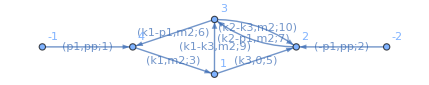

```mathematica
FromDigits[Reverse[{1,0,1,1,1,0,1,1,0}],2]
Import["./graphs/topoB/all/topoB_6_221.dot"]
```

```mathematica
FinalInts= {pp (d-4)^3(d-3)m2^3 INT[topoA,0,1,1,1,1,1,1,1,0],
(d-4)^3(d-3)m2^3  pp^(3/2) √(4 m2-pp)  INT[topoA,1,1,1,1,1,1,1,1,0], (*Still from Family A *)
(d-4)^2 pp  (d-3)INT[topoB,1,1,0,1,1,0,2,1,0], (* SECTOR 219*)
√((4 m2-pp) pp) (d-4)(d-3) pp INT[topoB,2,1,0,1,1,0,2,1,0], (* , 29/36*)(* from here from Christoph *)
pp (d-4)^2 (d-3)INT[topoB,1,0,1,1,2,0,1,1,0], (*30*)
-2 (d-4) (d-3)√((4 m2-pp) pp)  INT[topoB,2,0,1,1,2,0,1,1,0], (*31*)
pp (d-4)^2(d-3) INT[topoB,0,1,1,1,0,0,2,1,1], (*32*)
(2 (d-4) (d-3) 1/2 (10-3 d) √((4 m2-pp) pp))/(-4m2+pp) INT[topoB,0,1,1,1,0,0,1,2,1], (*33*)
pp (d-4) ((d-3)) INT[topoB,0,1,1,1,0,0,3,1,1],(*34*)
(* With baikov, you find immediately these two, Christoph does easy projects. *)
pp (d-4)^3 (d-3) √((4 m2-pp) pp) INT[topoB,1,1,1,1,1,0,1,1,1],(*35*)
 (d-4)^3 (d-3)(pp INT[topoB,1,1,1,1,1,-1,1,1,1] - pp^2 INT[topoB,1,1,1,1,1,0,1,1,1])(*36*)
}
```

{(-4+d)^3 (-3+d) m2^3 pp INT[topoA,0,1,1,1,1,1,1,1,0],(-4+d)^3 (-3+d) m2^3 √(4 m2-pp) pp^(3/2) INT[topoA,1,1,1,1,1,1,1,1,0],(-4+d)^2 (-3+d) pp INT[topoB,1,1,0,1,1,0,2,1,0],(-4+d) (-3+d) pp √((4 m2-pp) pp) INT[topoB,2,1,0,1,1,0,2,1,0],(-4+d)^2 (-3+d) pp INT[topoB,1,0,1,1,2,0,1,1,0],-2 (-4+d) (-3+d) √((4 m2-pp) pp) INT[topoB,2,0,1,1,2,0,1,1,0],(-4+d)^2 (-3+d) pp INT[topoB,0,1,1,1,0,0,2,1,1],((10-3 d) (-4+d) (-3+d) √((4 m2-pp) pp) INT[topoB,0,1,1,1,0,0,1,2,1])/(-4 m2+pp),(-4+d) (-3+d) pp INT[topoB,0,1,1,1,0,0,3,1,1],(-4+d)^3 (-3+d) pp √((4 m2-pp) pp) INT[topoB,1,1,1,1,1,0,1,1,1],(-4+d)^3 (-3+d) (pp INT[topoB,1,1,1,1,1,-1,1,1,1]-pp^2 INT[topoB,1,1,1,1,1,0,1,1,1])}

```mathematica
Basis = Join[FinalBasisD4,FinalInts ] /. j[a__] ->INT[a] /. pp -> ρ /. m2 -> 1 /. G2[ρ] ->G2 /. G3[ρ]->G3 /. G1[ρ] ->G1 /. G1->G1[ρ] /. G2 -> G2[ρ] /. G3 ->G3[ρ];
Length[Basis]
```

36

```mathematica
(* ints to differentiate *)
todiff=Union@Cases[Basis, _INT, ∞];
Export["./todiff.txt", todiff];
```

```mathematica
deq = Import["./deq/deqFULL.m"] /. INT["topoA", a__, {bin__}]-> INT[topoA, bin]/. INT["topoB", a__, {bin__}]-> INT[topoB, bin]/. m2-> 1 /. pp -> ρ;
```

```mathematica
DER=Collect[D[Basis , ρ]+(Basis /.INT[a__] :> der[INT[a],ρ])/.deq /.derGs /. der2Omega0/. der3Omega0, {_INT,_ω0,_G1, _G2, _G3},Simplify];
```

```mathematica
toreduce=Join[Union@Cases[test, _INT, ∞],Union@Cases[DER, _INT, ∞]]//Union;
Export["./toreduce.txt",toreduce]
```

./toreduce.txt

```mathematica
reduction = Import["./reductions/reductionFULL.m"]/.{ INT["topoA", a__,{bin__}]:> INT[topoA, bin], INT["topoB", a__,{bin__}]:> INT[topoB, bin]}/.m2 -> 1/. pp -> ρ;
```

```mathematica
BasisRed= Collect[Basis /. reduction, {_INT,_ω0,_G1, _G2,_G3}, Simplify];
DERred= Collect[DER /. reduction, {_INT, _ω0,_G1, _G2, _G3}, Simplify];
```

```mathematica
BasisRed//Dimensions
```

{36}

```mathematica
miNew= {
INT[topoA,1,1,1,0,0,0,0,0,0], (*7, 1 *)
INT[topoA,0,1,1,0,0,0,1,1,0], (*198, 2 *)
INT[topoA,0,0,1,0,1,0,1,1,0],  (*212, 5 *)
INT[topoA,0,0,1,0,1,0,2,1,0],
INT[topoA,0,0,2,0,1,0,1,1,0],
INT[topoA,0,1,1,1,0,0,1,0,0], (* 78, 7*)
INT[topoA,0,2,1,1,0,0,1,0,0],
INT[topoA,1,1,1,1,0,0,0,0,0], (*15, 8*)
INT[topoA,0,1,1,0,1,0,1,1,0], (* 214, 9*)
INT[topoA,0,1,1,1,0,0,1,1,0], (* 206, 12*)
INT[topoA,0,1,1,2,0,0,1,1,0],
INT[topoA,0,2,1,1,0,0,1,1,0],
INT[topoA,0,1,1,1,0,1,1,0,0],(* 110, 14*)
INT[topoA,0,2,1,1,0,1,1,0,0],
INT[topoA,1,1,1,1,1,0,0,0,0],(*31, 15*)
INT[topoB,1,1,0,0,0,0,1,1,0], (*195, 16*)
INT[topoB,0,1,0,1,0,0,1,1,0], (*202, 19*)
INT[topoB,0,2,0,1,0,0,1,1,0],
INT[topoB,0,3,0,1,0,0,1,1,0],
INT[topoB,0,0,1,1,1,0,1,1,0],
INT[topoB,0,0,2,1,1,0,1,1,0],
INT[topoA,0,1,1,0,1,1,1,1,0],INT[topoA,0,1,1,1,1,0,1,1,0],INT[topoA,1,1,1,0,1,1,1,1,0],INT[topoA,1,1,1,1,1,1,0,0,0],INT[topoA,1,2,1,0,1,1,1,1,0],INT[topoB,1,1,0,1,0,0,1,1,0],INT[topoB,1,1,0,1,1,0,1,1,0],INT[topoB,2,1,0,1,1,0,1,1,0],INT[topoB,0,1,1,1,0,0,1,1,1],INT[topoB,0,1,1,1,0,0,2,1,1],INT[topoB,0,2,1,1,0,0,1,1,1],INT[topoB,1,0,1,1,1,0,1,1,0],INT[topoB,1,1,1,1,1,0,1,1,1],INT[topoB,2,0,1,1,1,0,1,1,0],INT[topoB,2,1,1,1,1,0,1,1,1]};
```

```mathematica
(*Table[{miTmp[[i]] ,FromDigits[Reverse[(miTmp[[i,2;;]]/. 3->1/. 2-> 1 /. -1 -> 0 /. -2 -> 0 /. INT -> List) ],2], Total[miTmp[[i,2;;]] /. 3->1 /. 2-> 1 /. -1 -> 0 /. -2 -> 0 /. INT -> List ]}, {i,1,Length[miTmp]}]//TableForm*)
```

```mathematica
(*Table[{mi[[i]] ,FromDigits[Reverse[(mi[[i,2;;]]/. 3->1/. 2-> 1 /. -1 -> 0 /. -2 -> 0 /. INT -> List) ],2], Total[mi[[i,2;;]] /. 3->1 /. 2-> 1 /. -1 -> 0 /. -2 -> 0 /. INT -> List ]}, {i,1,Length[mi]}]//TableForm*)
```

```mathematica
(*mi = Union@Cases[BasisRed, _INT, ∞];
Complement[mi, miNew]*)
```

```mathematica
mi = Union@Cases[BasisRed, _INT, ∞];
mi = miNew;
MAT = CoefficientArrays[DERred,mi][[2]]//Normal;
CB = CoefficientArrays[BasisRed,mi][[2]]//Normal ;
```

```mathematica
toinvert=Together[CB] /. removeArgument/.{√(-((-4+ρ) ρ)) ->sqrt2 sqrt3, 1/√(-((-4+ρ) ρ)) -> sqrt2 sqrt3/(4-ρ)/ρ,1/(-((-4+ρ) ρ))^(3/2)->sqrt2 sqrt3/(4-ρ)/(4-ρ)/ρ^2,1/(-((-4+ρ) ρ))^(5/2)->sqrt2 sqrt3/(4-ρ)^3/ρ^3 }/.{ G2[ρ]-> G2, G1[ρ]-> G1,G3[ρ]-> G3 }/. (64-20ρ+ρ^2)^a_Integer-> tmpV^a /. (64-20ρ+ρ^2)^a_:> (64-20ρ+ρ^2)^(a-1/2)sqrt /. tmpV -> ((64-20ρ+ρ^2))/.(4-ρ)^a_Integer:> tmpV^a/.(4-ρ)^a_:> (4-ρ)^(a-1/2)sqrt2 /. tmpV -> (4-ρ)/.(ρ)^a_Integer:> tmpV^a/.(ρ)^a_:> (ρ)^(a-1/2)sqrt3 /. tmpV -> (ρ);
```

```mathematica
inverse = FFInverse[toinvert];
```

```mathematica
inverseSimplified=Collect[Collect[inverse /.{sqrt^2 -> 64-20ρ+ρ^2,sqrt^4 -> (64-20ρ+ρ^2)^2}, {G1,G2,G3},Simplify],{ω0,dω0,G1,G2,G3},Simplify];
```

```mathematica
(*inverseSimplified.toinvert/.sqrt-> Sqrt[64-20ρ+ρ^2] /.sqrt2-> Sqrt[4-ρ]/.sqrt3-> Sqrt[ρ]//Together;*)
```

```mathematica
MATSymb=(MAT/. removeArgument/.{ G2[ρ]-> G2, G1[ρ]-> G1,G3[ρ]-> G3 }/.{√(-((-4+ρ) ρ)) ->sqrt2 sqrt3, 1/√(-((-4+ρ) ρ)) -> sqrt2 sqrt3/(4-ρ)/ρ}/. (64-20ρ+ρ^2)^a_Integer-> tmpV^a /. (64-20ρ+ρ^2)^a_:> (64-20ρ+ρ^2)^(a-1/2)sqrt /. tmpV -> ((64-20ρ+ρ^2))/.(4-ρ)^a_Integer:> tmpV^a/.(4-ρ)^a_:> (4-ρ)^(a-1/2)sqrt2 /. tmpV -> (4-ρ)/.(ρ)^a_Integer:> tmpV^a/.(ρ)^a_:> (ρ)^(a-1/2)sqrt3 /. tmpV -> (ρ));
diffeq=(MATSymb.inverseSimplified );
```

```mathematica
MATSymb//Dimensions
inverseSimplified//Dimensions
```

{36,36}

{36,36}

```mathematica
(*MATSymb /. { G2-> G2[ρ], G1-> G1[ρ],G3-> G3[ρ] } /.sqrt-> Sqrt[64-20ρ+ρ^2] /.sqrt2-> Sqrt[4-ρ]/.sqrt3-> Sqrt[ρ];
% - MAT/.removeArgument/. ρ-> 1//Together*)
```

```mathematica
simplified=Collect[Collect[Collect[diffeq[[]] /. sqrt^2 -> 64-20ρ+ρ^2, {G1,G1,G3,ω0,dω0},Simplify] /.sqrt2 -> Sqrt[4-ρ] /.sqrt3-> Sqrt[ρ] /. sqrt -> Sqrt[64-20ρ+ρ^2], {G2,G3,G1, ω0,dω0},Simplify]//FullSimplify, {G2,G3,G1, ω0,dω0},Simplify];
```

```mathematica
RotFull = ArrayFlatten[{{Rot25masters,0},{0,IdentityMatrix[11]}}];
```

```mathematica
derRot=FullSimplify[D[RotFull/.removeArgument/.putArgument,ρ]/.derGs /. der3Omega0/.der2Omega0]/.derGs /. der3Omega0/.der2Omega0;
```

```mathematica
tmp1=derRot.Inverse[RotFull]//Simplify;
tmp2 =RotFull.simplified.Inverse[RotFull]/.derGs /. der3Omega0/.der2Omega0//Simplify;
```

```mathematica
ToFixFinal= tmp1 + tmp2/.der2Omega0//Simplify;
```

```mathematica
Variables[ToFixFinal]
```

{d,ρ,G1[ρ],G2[ρ],G3[ρ],ω0[ρ],ω0'[ρ]}

```mathematica
R = IdentityMatrix[36];
R[[29,22]] =1/6 ρ;
R[[29,17]]=(ρ/12-2/3)G3[ρ] + ((16-ρ) ρ ω0[ρ])/(12 √(-((-4+ρ) ρ)));
R[[29,16]] =-1/6 √(-((-4+ρ) ρ));
```

```mathematica
R2 =IdentityMatrix[36];
R2[[31]]={0,0,0,0,0,((-4+d) (-3+d))/(2 ρ),0,0,0,0,0,0,-(-4+d)/(4 ρ),((-4+d) √(4-ρ))/(4 ρ^(3/2)),0,(-4+d)/(6 ρ),-((-4+d) (16 (-4+d) √(64-20 ρ+ρ^2) G2[ρ]+(-64+8 (-2+d) ρ+(-4+d) ρ^2) ω0[ρ]-2 ρ (64-20 ρ+ρ^2) ω0'[ρ]))/(24 (-4+ρ) ρ),-(2 (-4+d)^2 (-16+ρ))/(3 ρ √(64-20 ρ+ρ^2)),0,(-4+d)/(8 ρ),0,0,0,0,0,0,0,0,0,(-4+d)/(2 ρ),(-4+d)/(√(-((-4+ρ) ρ))),0,0,0,0,0};
R2[[33]] ={((-4+d) (124+d (-74+11 d)))/(2 (-3+d) (-10+3 d) (-4+ρ)),((-4+d) (22-24 ρ+d (-6+7 ρ)))/(3 (-3+d) (-4+ρ) ρ),(-4+d)^2/((-10+3 d) √(-((-4+ρ) ρ))),-(3 (-4+d)^2)/((-10+3 d) (-4+ρ)),-((-4+d) (44-18 ρ+d (-12+5 ρ)))/(2 (-10+3 d) (-4+ρ) ρ),((-4+d) (1116-936 ρ+d (-942+728 ρ+d (262-184 ρ+3 d (-8+5 ρ)))))/(2 (-3+d) (-10+3 d) (-4+ρ) ρ),-((-4+d)^3 (-8+3 d))/(2 (-3+d) (-10+3 d) √(-((-4+ρ) ρ))),0,0,-(-4+d)^2/(2 (-3+d) √(-((-4+ρ) ρ))),((-4+d) (-11+2 (17-7 ρ) ρ+d (3+2 ρ (-5+2 ρ))))/(2 (-3+d) (-4+ρ) (-1+ρ) ρ),((-4+d) (-11-3 ρ+d (3+ρ)))/(2 (-3+d) (-4+ρ) ρ),0,0,0,0,-1/(16 (-10+3 d) (-16+ρ) (-4+ρ)^2 ρ ω0[ρ])(-4+d) (512 (-4+d) (-16+ρ) (-4+ρ) G1[ρ]-256 (-4+d)^2 (-16+ρ) (-4+ρ) G2[ρ]^2+(4096 (-4+d)^2+512 (-5+d) (-8+3 d) ρ-64 (134+d (-77+10 d)) ρ^2-8 (90+d (-47+7 d)) ρ^3+(68+d (-36+5 d)) ρ^4) ω0[ρ]^2-4 (-4+d) (-16+ρ) (-4+ρ) ρ (64+ρ (-40+3 ρ)) ω0[ρ] ω0'[ρ]+4 (-16+ρ)^2 (-4+ρ)^2 ρ^2 ω0'[ρ]^2-32 (-4+d) √((-16+ρ) (-4+ρ)) G2[ρ] (-((-4+d) (64+ρ (-40+3 ρ)) ω0[ρ])+2 (-16+ρ) (-4+ρ) ρ ω0'[ρ])),(2 (-4+d)^2 (-16+ρ) (16 (-4+d) √((-16+ρ) (-4+ρ)) G2[ρ]-(-4+d) (64+ρ (-40+3 ρ)) ω0[ρ]+2 (-16+ρ) (-4+ρ) ρ ω0'[ρ]))/((-10+3 d) ((-16+ρ) (-4+ρ))^(3/2) ρ ω0[ρ]),-(32 (-4+d)^3)/((-10+3 d) (-4+ρ) ρ ω0[ρ]),0,0,0,0,0,0,0,0,0,0,0,0,((-4+d) (2+ρ))/(2 (-4+ρ) ρ),(-4+d)/(√(-((-4+ρ) ρ))),0,0,0};
```

```mathematica
R3 =IdentityMatrix[36];
R3[[31,30]] =1/2 Sqrt[ρ]Sqrt[4-ρ] /ρ;
R3[[31,31]] = Sqrt[ρ]Sqrt[4-ρ] /(d-4);
R3[[31,17]]= ((16-ρ) ρ ω0[ρ])/(12 √(-((-4+ρ) ρ))) -1/3 G3[ρ];
R3[[33,33]] = Sqrt[ρ]Sqrt[4-ρ] /(d-4);
R3[[33,32  ]]=1/2 Sqrt[ρ]Sqrt[4-ρ] /ρ;
R3[[33,17]] = ((16-ρ) ρ ω0[ρ])/(6 √(-((-4+ρ) ρ))) -2/3 G3[ρ];
R3[[33,11]] =(√(-((-4+ρ) ρ)))/(2 (1-ρ));
```

```mathematica
R4 = IdentityMatrix[36];
R4[[34,33]] =  (ρ/(4 √(-((-4+ρ) ρ))))
R4[[34,17]]= ρ/(6 √(-((-4+ρ) ρ)))G3[ρ]  -((-16+ρ) (4+ρ) ω0[ρ])/(48 (-4+ρ));
R4[[34,11]]=1/(4 (-1+ρ));
```

ρ/(4 √(-((-4+ρ) ρ)))

```mathematica
R//Variables
ToFixFinal//Variables
```

{ρ,G3[ρ],ω0[ρ]}

{d,ρ,G1[ρ],G2[ρ],G3[ρ],ω0[ρ],ω0'[ρ]}

```mathematica
test=D[Inverse[R],ρ].R + Inverse[R].ToFixFinal.R (*/. d-> 4*)/.derGs /.removeArgument/.putArgument;
test2=D[R2,ρ].Inverse[R2]+R2.test.Inverse[R2] (*/. d-> 4*)/.derGs /.der3Omega0/.der2Omega0/.removeArgument/.putArgument;
test3=D[R3,ρ].Inverse[R3]+R3.test2.Inverse[R3] (*/. d-> 4*)/.derGs /.der3Omega0/.der2Omega0/.removeArgument/.putArgument;
test4=D[R4,ρ].Inverse[R4]+R4.test3.Inverse[R4] (*/. d-> 4*)/.derGs /.der3Omega0/.der2Omega0/.removeArgument/.putArgument;
```

```mathematica
CombinedRot=Collect[R4.R3.R2.Inverse[R], {_ω0},Simplify];
CanonDeq=D[CombinedRot,ρ].Inverse[CombinedRot]+CombinedRot.ToFixFinal.Inverse[CombinedRot] (*/. d-> 4*)/.derGs /.der3Omega0/.der2Omega0/.removeArgument/.putArgument;
CanonDeq=Collect[CanonDeq, {_ω0},FullSimplify];
```

```mathematica
CanonDeq /. d -> 4//Flatten // Union
```

{0}

```mathematica
FULLROT=Collect[CombinedRot.RotFull, {_ω0,_G2,_G1,_G3},FullSimplify];
```

```mathematica
Basis= (d-4)^2 Basis;
```

```mathematica
Export["./BASES/Final/startBasis.m", Basis]
Export["./BASES/Final/Rot.m", FULLROT]
```

./BASES/Final/startBasis.m

./BASES/Final/Rot.m

## Final Check

```mathematica
Basis=Import["./BASES/Final/startBasis.m"];
R=Import["./BASES/Final/Rot.m"];
derGs={G1'[ρ]->-((-8+ρ) (8+ρ)^3 ω0[ρ]^2)/(64 (64-20 ρ+ρ^2)^2),G2'[ρ]->-(8 G1[ρ])/(ρ √(64-20 ρ+ρ^2) ω0[ρ]),G3'[ρ]->((2+ρ) ω0[ρ])/((4-ρ)^(3/2) √ρ)};
der2Omega0=ω0''[ρ]->-((-8+ρ) ω0[ρ])/(2 ρ (64-20 ρ+ρ^2))-(2 (32-15 ρ+ρ^2) ω0'[ρ])/(ρ (64-20 ρ+ρ^2))+ω0'[ρ]^2/(2 ω0[ρ]);
der3Omega0=Derivative[3][ω0][ρ]->((4-ρ) ω0[ρ])/((-16+ρ) (-4+ρ) ρ^2)+((-64+68 ρ-7 ρ^2) ω0'[ρ])/((-16+ρ) (-4+ρ) ρ^2)-(6 (32-15 ρ+ρ^2) ω0''[ρ])/((-16+ρ) (-4+ρ) ρ);
removeArgument={G1[ρ]->G1,G2[ρ]->G2,G3[ρ]->G3,ω1[ρ]->ω1,ω1'[ρ]->dω1,ω1''[ρ]->ddω1,ω2[ρ]->ω2,ω2'[ρ]->dω2,ω2''[ρ]->ddω2,ω0[ρ]->ω0,ω0'[ρ]->dω0,ω0''[ρ]->ddω0};
putArgument={G1->G1[ρ],G2->G2[ρ],G3->G3[ρ],ω1->ω1[ρ],dω1->ω1'[ρ],ddω1->ω1''[ρ],ω2->ω2[ρ],dω2->ω2'[ρ],ddω2->ω2''[ρ],ω0->ω0[ρ],dω0->ω0'[ρ],ddω0->ω0''[ρ]};
miNew ={INT[topoA,1,1,1,0,0,0,0,0,0],INT[topoA,0,1,1,0,0,0,1,1,0],INT[topoA,0,0,1,0,1,0,1,1,0],INT[topoA,0,0,1,0,1,0,2,1,0],INT[topoA,0,0,2,0,1,0,1,1,0],INT[topoA,0,1,1,1,0,0,1,0,0],INT[topoA,0,2,1,1,0,0,1,0,0],INT[topoA,1,1,1,1,0,0,0,0,0],INT[topoA,0,1,1,0,1,0,1,1,0],INT[topoA,0,1,1,1,0,0,1,1,0],INT[topoA,0,1,1,2,0,0,1,1,0],INT[topoA,0,2,1,1,0,0,1,1,0],INT[topoA,0,1,1,1,0,1,1,0,0],INT[topoA,0,2,1,1,0,1,1,0,0],INT[topoA,1,1,1,1,1,0,0,0,0],INT[topoB,1,1,0,0,0,0,1,1,0],INT[topoB,0,1,0,1,0,0,1,1,0],INT[topoB,0,2,0,1,0,0,1,1,0],INT[topoB,0,3,0,1,0,0,1,1,0],INT[topoB,0,0,1,1,1,0,1,1,0],INT[topoB,0,0,2,1,1,0,1,1,0],INT[topoA,0,1,1,0,1,1,1,1,0],INT[topoA,0,1,1,1,1,0,1,1,0],INT[topoA,1,1,1,0,1,1,1,1,0],INT[topoA,1,1,1,1,1,1,0,0,0],INT[topoA,1,2,1,0,1,1,1,1,0],INT[topoB,1,1,0,1,0,0,1,1,0],INT[topoB,1,1,0,1,1,0,1,1,0],INT[topoB,2,1,0,1,1,0,1,1,0],INT[topoB,0,1,1,1,0,0,1,1,1],INT[topoB,0,1,1,1,0,0,2,1,1],INT[topoB,0,2,1,1,0,0,1,1,1],INT[topoB,1,0,1,1,1,0,1,1,0],INT[topoB,1,1,1,1,1,0,1,1,1],INT[topoB,2,0,1,1,1,0,1,1,0],INT[topoB,2,1,1,1,1,0,1,1,1]};
```

```mathematica
deq = Import["./deq/deqFULL.m"] /. INT["topoA", a__, {bin__}]-> INT[topoA, bin]/. INT["topoB", a__, {bin__}]-> INT[topoB, bin]/. m2-> 1 /. pp -> ρ;
reduction = Import["./reductions/reductionFULL.m"]/.{ INT["topoA", a__,{bin__}]:> INT[topoA, bin], INT["topoB", a__,{bin__}]:> INT[topoB, bin]}/.m2 -> 1/. pp -> ρ;
DER=Collect[D[Basis , ρ]+(Basis /.INT[a__] :> der[INT[a],ρ])/.deq /.derGs /. der2Omega0/. der3Omega0, {_INT,_ω0,_G1, _G2, _G3},Simplify];
BasisRed= Collect[Basis /. reduction, {_INT,_ω0,_G1, _G2,_G3}, Simplify];
DERred= Collect[DER /. reduction, {_INT, _ω0,_G1, _G2, _G3}, Simplify];
```

```mathematica
mi = miNew;
MAT = CoefficientArrays[DERred,mi][[2]]//Normal;
CB = CoefficientArrays[BasisRed,mi][[2]]//Normal ;
```

```mathematica
toinvert=Together[CB] /. removeArgument/.{√(-((-4+ρ) ρ)) ->sqrt2 sqrt3, 1/√(-((-4+ρ) ρ)) -> sqrt2 sqrt3/(4-ρ)/ρ,1/(-((-4+ρ) ρ))^(3/2)->sqrt2 sqrt3/(4-ρ)/(4-ρ)/ρ^2,1/(-((-4+ρ) ρ))^(5/2)->sqrt2 sqrt3/(4-ρ)^3/ρ^3 }/. (64-20ρ+ρ^2)^a_Integer-> tmpV^a /. (64-20ρ+ρ^2)^a_:> (64-20ρ+ρ^2)^(a-1/2)sqrt /. tmpV -> ((64-20ρ+ρ^2))/.(4-ρ)^a_Integer:> tmpV^a/.(4-ρ)^a_:> (4-ρ)^(a-1/2)sqrt2 /. tmpV -> (4-ρ)/.(ρ)^a_Integer:> tmpV^a/.(ρ)^a_:> (ρ)^(a-1/2)sqrt3 /. tmpV -> (ρ);
inverse = FFInverse[toinvert];
inverseSimplified=Collect[Collect[inverse /.{sqrt^2 -> 64-20ρ+ρ^2,sqrt^4 -> (64-20ρ+ρ^2)^2}, {G1,G2,G3},Simplify],{ω0,dω0,G1,G2,G3},Simplify];
MATSymb=(MAT/. removeArgument/.{√(-((-4+ρ) ρ)) ->sqrt2 sqrt3, 1/√(-((-4+ρ) ρ)) -> sqrt2 sqrt3/(4-ρ)/ρ}/. (64-20ρ+ρ^2)^a_Integer-> tmpV^a /. (64-20ρ+ρ^2)^a_:> (64-20ρ+ρ^2)^(a-1/2)sqrt /. tmpV -> ((64-20ρ+ρ^2))/.(4-ρ)^a_Integer:> tmpV^a/.(4-ρ)^a_:> (4-ρ)^(a-1/2)sqrt2 /. tmpV -> (4-ρ)/.(ρ)^a_Integer:> tmpV^a/.(ρ)^a_:> (ρ)^(a-1/2)sqrt3 /. tmpV -> (ρ));
diffeq=(MATSymb.inverseSimplified );
```

```mathematica
DiffEqPreRot=Collect[Collect[Collect[diffeq[[]] /. sqrt^2 -> 64-20ρ+ρ^2, {G1,G1,G3,ω0,dω0},Simplify] /.sqrt2 -> Sqrt[4-ρ] /.sqrt3-> Sqrt[ρ] /. sqrt -> Sqrt[64-20ρ+ρ^2], {G2,G3,G1, ω0,dω0},Simplify]//FullSimplify, {G2,G3,G1, ω0,dω0},Simplify];
```

```mathematica
CanonDeq=D[R,ρ].Inverse[R]+R.DiffEqPreRot.Inverse[R]/.derGs /.der3Omega0/.der2Omega0/.removeArgument/.putArgument;
CanonDeq=Collect[CanonDeq, {_ω0},FullSimplify];
```

```mathematica
CanonDeq /. d-> 4//Flatten //Union
```

{0}

```mathematica
tomatchLetters=(CanonDeq/.d-> 2//Flatten //Union//Simplify//Union);
Length[%]
tomatchLetters[[67]]
letters ={Ker[1]->1/x,Ker[2]->1/(-1+x),Ker[3]->1/(-4+x),Ker[4]->1/(√(4-x) √x),Ker[5]->1/(16-x),EKer[1]->(√(4-x) √(16-x))/((-16+x) (-4+x) x ω0[x]),EKer[2]->(√(4-x) √(16-x) GG2[x])/((-16+x) (-4+x) x ω0[x]),EKer[3]->(√(4-x) √(16-x) GG2[x]^2)/((-16+x) (-4+x) x ω0[x]),EKer[4]->(√(4-x) √(16-x) GG2[x]^3)/((-16+x) (-4+x) x ω0[x]),EKer[5]->(√(4-x) √(16-x) GG3[x])/((-16+x) (-4+x) x ω0[x]),EKer[6]->(√(4-x) √(16-x) GG2[x] GG3[x])/((-16+x) (-4+x) x ω0[x]),EKer[7]->GG3[x]/(√(4-x) √x),EKer[8]->GG3[x]/x,EKer[9]->GG3[x]/(4-x),EKer[10]->GG3[x]/(16-x),EKer[11]->ω0[x],EKer[12]->ω0[x]/x,EKer[13]->ω0[x]/(4-x),EKer[14]->(√(4-x) ω0[x])/(√x),EKer[15]->(√x ω0[x])/(√(4-x)),EKer[16]->(√(4-x) √x ω0[x])/(-4+x)^2,EKer[17]->(√(4-x) √(16-x) (8+x)^2 (64-8 x+x^2) ω0[x])/((-16+x)^2 (-4+x)^2 x),EKer[18]->(√(4-x) √(16-x) (8+x)^2 (64-8 x+x^2) GG2[x] ω0[x])/((-16+x)^2 (-4+x)^2 x),EKer[19]->((-8+x) (8+x)^3 ω0[x]^2)/((-16+x)^2 (-4+x)^2)} /. x -> ρ ;
```

83

(20-2 ρ)/(64-20 ρ+ρ^2)-(32 G2[ρ])/(√((-16+ρ) (-4+ρ)) ρ ω0[ρ])

```mathematica
letters  = letters /. {GG2 -> G2, GG3 -> G3, GG1-> G1};
```

```mathematica
zeros=Position[(CanonDeq/.d-> 2) ,0];
tofix=Table[Sum[c[i]Ker[i],{i,1,5}]+Sum[c[i+5]EKer[i],{i,1,19}], {i,1,36}, {j,1,36}];
Do[tofix[[zeros[[i,1]],zeros[[i,2]]]]=0, {i,1,Length[zeros]}]
fixed =tofix;
```

```mathematica
roots = {√(4-ρ) -> root[2],Sqrt[ρ]-> root[1],√(16-ρ)-> root[3]};
rootsDen = {1/√(4-ρ) -> root[2]/(4-ρ),1/Sqrt[ρ]-> root[1]/ρ,1/√(16-ρ)-> root[3]/(16-ρ)};
```

```mathematica
lettersRoots=letters  /.roots /.rootsDen
```

{Ker[1]→1/ρ,Ker[2]→1/(-1+ρ),Ker[3]→1/(-4+ρ),Ker[4]→(root[1] root[2])/((4-ρ) ρ),Ker[5]→1/(16-ρ),EKer[1]→(root[2] root[3])/((-16+ρ) (-4+ρ) ρ ω0[ρ]),EKer[2]→(G2[ρ] root[2] root[3])/((-16+ρ) (-4+ρ) ρ ω0[ρ]),EKer[3]→(G2[ρ]^2 root[2] root[3])/((-16+ρ) (-4+ρ) ρ ω0[ρ]),EKer[4]→(G2[ρ]^3 root[2] root[3])/((-16+ρ) (-4+ρ) ρ ω0[ρ]),EKer[5]→(G3[ρ] root[2] root[3])/((-16+ρ) (-4+ρ) ρ ω0[ρ]),EKer[6]→(G2[ρ] G3[ρ] root[2] root[3])/((-16+ρ) (-4+ρ) ρ ω0[ρ]),EKer[7]→(G3[ρ] root[1] root[2])/((4-ρ) ρ),EKer[8]→G3[ρ]/ρ,EKer[9]→G3[ρ]/(4-ρ),EKer[10]→G3[ρ]/(16-ρ),EKer[11]→ω0[ρ],EKer[12]→ω0[ρ]/ρ,EKer[13]→ω0[ρ]/(4-ρ),EKer[14]→(root[1] root[2] ω0[ρ])/ρ,EKer[15]→(root[1] root[2] ω0[ρ])/(4-ρ),EKer[16]→(root[1] root[2] ω0[ρ])/(-4+ρ)^2,EKer[17]→((8+ρ)^2 (64-8 ρ+ρ^2) root[2] root[3] ω0[ρ])/((-16+ρ)^2 (-4+ρ)^2 ρ),EKer[18]→((8+ρ)^2 (64-8 ρ+ρ^2) G2[ρ] root[2] root[3] ω0[ρ])/((-16+ρ)^2 (-4+ρ)^2 ρ),EKer[19]→((-8+ρ) (8+ρ)^3 ω0[ρ]^2)/((-16+ρ)^2 (-4+ρ)^2)}

```mathematica
nonzeros=Complement[Flatten[Table[{i,j}, {i,1,36},{j,1,36}],1],zeros];
```

```mathematica
adjustRoots = {1/√(-((-4+ρ) ρ)) -> root[1]root[2]/(4-ρ)/ρ, 1/(-((-4+ρ) ρ))^(3/2) ->1/((4-ρ)^2ρ^2)root[1]root[2] ,1/√((-16+ρ) (-4+ρ))-> root[2] root[3]/((16-ρ)(4-ρ)),1/((-16+ρ) (-4+ρ))^(3/2) -> root[2] root[3]/((16-ρ)^2(4-ρ)^2) };
```

```mathematica
Do[(*index =1;*)
tozero=tofix[[nonzeros[[index,1]],nonzeros[[index,2]]]] -(CanonDeq/.adjustRoots/.d-> 2)[[nonzeros[[index,1]],nonzeros[[index,2]]]];
tozero =Collect[ Numerator[tozero /. lettersRoots  // Together], {_G1,_G2,_G3,_ω0, _root,ρ},FF] /. FF[a_]:> FF[Simplify[a]];
eqs=Union@Cases[tozero,_FF,∞] /. FF -> Identity ;
sol=Flatten[Solve[Thread[Equal[eqs,0]],(Cases[eqs,_c,∞]//Union)]];
(*Print[eqs];*)
(*Print[index, "  ", sol];*)
fixed[[nonzeros[[index,1]],nonzeros[[index,2]]]]=tofix[[nonzeros[[index,1]],nonzeros[[index,2]]]]/.sol;, {index,1,Length[nonzeros]}]
```

```mathematica
DEQSymbolic=fixed;
```

```mathematica
(*Export["./BASES/Final/DEQ.m",DEQSymbolic]
Export["./BASES/Final/roots.m", roots]
Export["./BASES/Final/letters.m", letters]*)
```

./BASES/Final/DEQ.m

./BASES/Final/roots.m

./BASES/Final/letters.m

## SOLUTION

```mathematica
Basis = Import["./BASES/Final/startBasis.m"];
R = Import["./BASES/Final/Rot.m"];
letters = Import["./BASES/Final/letters.m"];
roots = Import["./BASES/Final/roots.m"];
canM=Import["./BASES/Final/DEQ.m"];
```

```mathematica
Basis[[23]
```

(-4+d)^2 (((-120+133 d-49 d^2+6 d^3) (2 d^2 (24+15 ρ+ρ^2)+4 (154+95 ρ+7 ρ^2)-d (344+214 ρ+15 ρ^2)) INT[topoA,0,0,1,0,1,0,1,1,0])/((-7+2 d) (-4+ρ)^2)+((-4+d) (-3+d) (d^2 (-288+264 ρ+61 ρ^2+4 ρ^3)+8 (-462+427 ρ+96 ρ^2+7 ρ^3)-2 d (-1032+950 ρ+217 ρ^2+15 ρ^3)) INT[topoA,0,0,1,0,1,0,2,1,0])/(2 (-7+2 d) (-4+ρ)^2)-(2 (24-17 d+3 d^2) (924+514 ρ+56 ρ^2+d^2 (72+41 ρ+4 ρ^2)-3 d (172+97 ρ+10 ρ^2)) INT[topoA,0,0,2,0,1,0,1,1,0])/((-7+2 d) (-4+ρ)^2)-((-4+d) (-48+58 d-23 d^2+3 d^3) (22+3 d (-2+ρ)-10 ρ) INT[topoA,0,1,1,0,0,0,1,1,0])/(4 (-7+2 d) (-4+ρ))+(3 (-4+d) (-3+d)^2 (80-54 d+9 d^2) ρ INT[topoA,0,1,1,0,1,0,1,1,0])/(2 (-7+2 d) (-4+ρ))-(3 (-4+d) (-3+d)^2 (-10+3 d) ρ INT[topoA,0,1,1,0,1,1,1,1,0])/(-4+ρ))

```mathematica
Basis//Variables
```

{d,ρ,INT[topoA,0,0,1,0,1,0,1,1,0],INT[topoA,0,0,1,0,1,0,2,1,0],INT[topoA,0,0,2,0,1,0,1,1,0],INT[topoA,0,1,1,0,0,0,1,1,0],INT[topoA,0,1,1,0,1,0,1,1,0],INT[topoA,0,1,1,0,1,1,1,1,0],INT[topoA,0,1,1,1,0,0,1,0,0],INT[topoA,0,1,1,1,0,0,1,1,0],INT[topoA,0,1,1,1,0,1,1,0,0],INT[topoA,0,1,1,1,1,0,1,1,0],INT[topoA,0,1,1,1,1,1,1,1,0],INT[topoA,0,1,1,2,0,0,1,1,0],INT[topoA,0,2,1,1,0,0,1,0,0],INT[topoA,0,2,1,1,0,0,1,1,0],INT[topoA,0,2,1,1,0,1,1,0,0],INT[topoA,1,1,1,0,0,0,0,0,0],INT[topoA,1,1,1,1,0,0,0,0,0],INT[topoA,1,1,1,1,1,0,0,0,0],INT[topoA,1,1,1,1,1,1,0,0,0],INT[topoA,1,1,1,1,1,1,1,1,0],INT[topoB,0,0,1,1,1,0,1,1,0],INT[topoB,0,0,2,1,1,0,1,1,0],INT[topoB,0,1,0,1,0,0,1,1,0],INT[topoB,0,1,1,1,0,0,1,2,1],INT[topoB,0,1,1,1,0,0,2,1,1],INT[topoB,0,1,1,1,0,0,3,1,1],INT[topoB,0,2,0,1,0,0,1,1,0],INT[topoB,0,3,0,1,0,0,1,1,0],INT[topoB,1,0,1,1,2,0,1,1,0],INT[topoB,1,1,0,0,0,0,1,1,0],INT[topoB,1,1,0,1,0,0,1,1,0],INT[topoB,1,1,0,1,1,0,2,1,0],INT[topoB,1,1,1,1,1,-1,1,1,1],INT[topoB,1,1,1,1,1,0,1,1,1],INT[topoB,2,0,1,1,2,0,1,1,0],INT[topoB,2,1,0,1,1,0,2,1,0]}

```mathematica
R[[19;;22]]
```

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,((-4+d) (-10+ρ) ρ G2[ρ])/(8 √((-16+ρ) (-4+ρ)))+1/512 (16 (70-13 d)-(3072 (-6+d))/(-16+ρ)+(192 (-6+d))/(-4+ρ)+4 (48-7 d) ρ+(-36+7 d) ρ^2) ω0[ρ]+(-G1[ρ]+(2-d/2) G2[ρ]^2+1/8 √((-16+ρ) (-4+ρ)) ρ G2[ρ] ω0'[ρ]+((-16+ρ) (-4+ρ) ρ^2 ω0'[ρ]^2)/(64 (-4+d)))/ω0[ρ]+(ρ ((-64+(70+d (-10+ρ)-6 ρ) ρ) ω0'[ρ]-(-16+ρ) (-4+ρ) ρ ω0''[ρ]))/(64 (-4+d)),-1/8 √((-16+ρ) (-4+ρ)) ρ G2[ρ]+(ρ (32+ρ (-55+10 d+5 ρ-d ρ)) ω0[ρ])/(32 (-4+d))-((-16+ρ) (-4+ρ) ρ^2 ω0'[ρ])/(64 (-4+d)),((-16+ρ) (-4+ρ) ρ^2 ω0[ρ])/(64 (-4+d)),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(3 (-4+d) √ρ)/(2 √(4-ρ))+((2-d/2) G3[ρ])/ω0[ρ],0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
Basis[[22]]
```

(-4+d)^2 (((-2+d)^3 √(-((-4+ρ) ρ)) (-4928+988 ρ-38 ρ^2+d (1376-280 ρ+11 ρ^2)) INT[topoA,1,1,1,0,0,0,0,0,0])/(64 (-16+ρ) (-4+ρ)^2)+(3 (-2+d)^2 (114-71 d+11 d^2) ρ INT[topoA,1,1,1,1,0,0,0,0,0])/(64 √(-((-4+ρ) ρ)))-((-120+133 d-49 d^2+6 d^3) √(-((-4+ρ) ρ)) (-4352+448 ρ-38 ρ^2+d (1280-148 ρ+11 ρ^2)) INT[topoB,0,1,0,1,0,0,1,1,0])/(128 (-16+ρ) (-4+ρ)^2)-1/(128 (-16+ρ) (-4+ρ)^2)(-3+d) √(-((-4+ρ) ρ)) (d (81408-35488 ρ+3248 ρ^2-82 ρ^3)+d^2 (-15104+5568 ρ-492 ρ^2+11 ρ^3)+8 (-12800+7136 ρ-664 ρ^2+19 ρ^3)) INT[topoB,0,2,0,1,0,0,1,1,0]+((-3+d) √(-((-4+ρ) ρ)) (d (4096+2304 ρ-228 ρ^2+11 ρ^3)-2 (8192+3840 ρ-360 ρ^2+19 ρ^3)) INT[topoB,0,3,0,1,0,0,1,1,0])/(32 (-16+ρ) (-4+ρ)^2)+(3 (480-724 d+404 d^2-99 d^3+9 d^4) ρ INT[topoB,1,1,0,0,0,0,1,1,0])/(128 √(-((-4+ρ) ρ)))-(3 (-3+d)^2 (80-54 d+9 d^2) ρ INT[topoB,1,1,0,1,0,0,1,1,0])/(32 √(-((-4+ρ) ρ))))

```mathematica
INT[topoB,1,1,0,1,0,0,1,1,0]
```

INT[topoB,1,1,0,1,0,0,1,1,0]

```mathematica
Grid[{{"D1",k1^2-m^2,k1^2-m^2,k1^2-m^2},{"D2",k2^2-m^2,k2^2-m^2,k2^2-m^2},{"D3",k3^2-m^2,k3^2,k3^2},{"D4",(k1-p)^2-m^2,(k1-p)^2-m^2,(k1-p)^2-m^2},{"D5",(k2-p)^2-m^2,(k2-p)^2-m^2,(k2-p)^2-m^2},{"D6",(k3-p)^2-m^2,(k3-p)^2,(k3-p)^2},{"D7",(k1-k2)^2,(k1-k3)^2-m^2,(k1-k2)^2},{"D8",(k1-k3)^2,(k2-k3)^2-m^2,(k2+k3-p)^2-m^2},{"D9",(k2-k3)^2,(k1+k2-k3-p)^2,(k1+k3-p)^2-m^2}},Frame->All]
```

D1 | k1^2-m^2 | k1^2-m^2 | k1^2-m^2
D2 | k2^2-m^2 | k2^2-m^2 | k2^2-m^2
D3 | k3^2-m^2 | k3^2 | k3^2
D4 | -m^2+(k1-p)^2 | -m^2+(k1-p)^2 | -m^2+(k1-p)^2
D5 | -m^2+(k2-p)^2 | -m^2+(k2-p)^2 | -m^2+(k2-p)^2
D6 | -m^2+(k3-p)^2 | (k3-p)^2 | (k3-p)^2
D7 | (k1-k2)^2 | (k1-k3)^2-m^2 | (k1-k2)^2
D8 | (k1-k3)^2 | (k2-k3)^2-m^2 | -m^2+(k2+k3-p)^2
D9 | (k2-k3)^2 | (k1+k2-k3-p)^2 | -m^2+(k1+k3-p)^2

```mathematica
Tad[n_]:= m2^((d-2n)/2)Gamma[n-d/2]/Gamma[n] E^(EulerGamma eps);
```

```mathematica
Basis[[2]]//Factor
```

(3 (-4+d)^3 (-3+d) (-2+d) (-10+3 d) (-8+3 d) INT[topoA,0,1,1,0,0,0,1,1,0])/(32 (-7+2 d))

```mathematica
Series[Basis[[1]] /.INT[topoA,1,1,1,0,0,0,0,0,0]-> Tad[1]^3 /. m2->1 /. d->4 -2 eps, {eps,0,5}]//FullSimplify
```

-8-2 π^2 eps^2+8 Zeta[3] eps^3-(19 π^4 eps^4)/60+(2 π^2 Zeta[3]+(24 Zeta[5])/5) eps^5+O[eps]^6

## Baikov Analysis

```mathematica
Quit[]
```

```mathematica
Import["~/Software/DlogBasis/DlogBasis.wl"]
(*Import["~/Software/Baikov/Baikov.m"]*)
```

DlogBasis: Package for automated calculation of leading singularities and dlog integrands.
Pascal Wasser, Johannes Gutenberg University Mainz (2020).

```mathematica
Import["~/Software/SOFIA-main/SOFIA/SOFIA.m"]
```

m::shdw: Symbol m appears in multiple contexts {SOFIA`,Global`}; definitions in context SOFIA` may shadow or be shadowed by other definitions.

p::shdw: Symbol p appears in multiple contexts {SOFIA`,Global`}; definitions in context SOFIA` may shadow or be shadowed by other definitions.

Singularities of Feynman Integrals Automatized (v1.0.0.)

.oooooo..o   .oooooo.   oooooooooooo ooooo       .o.       
d8P'    `Y8  d8P'  `Y8b  `888'     `8 `888'      .888.      
Y88bo.      888      888  888          888      .8"888.     
 `"Y8888o.  888      888  888oooo8     888     .8' `888.    
     `"Y88b 888      888  888    "     888    .88ooo8888.   
oo     .d8P `88b    d88'  888          888   .8'     `888.  
8""88888P'   `Y8bood8P'  o888o        o888o o88o     o8888o|

Copyright © 2025 Miguel Correia, Mathieu Giroux, and Sebastian Mizera. All rights reserved.

Most important documented functions:

FeynmanDraw: Running this function will trigger a drawing window, allowing you to draw your diagram with your mouse. The output is the corresponding list of edges and nodes for the diagram.
FeynmanPlot: Plots the input diagram.
SOFIABaikov: Returns the optimized LBL Baikov representation for an input diagram (list of edges and nodes).
SOFIA: Returns the singularities or letters depending on options.
SOFIADecomposeAlphabet: SOFIADecomposeAlphabet[LetterToDecompose,SymbolData] - decomposes the letter LetterToDecompose in terms of the alphabet provided in SymbolData.
SolvePolynomialSystem: Solves a polynomial system using the method specified by Solver->{FastFubini, momentumPLD} option.
Subtopologies: Generates non-trivial subtopologies.
SymmetryQuotient: Given a list of diagrams, returns a reduced list of diagrams with a symmetry map.

```mathematica
removeArgument={G1[ρ]-> G1, G2[ρ]-> G2, G3[ρ]-> G3,ω1[ρ]->ω1,ω1'[ρ]->dω1,ω1''[ρ]->ddω1,ω2[ρ]->ω2,ω2'[ρ]->dω2,ω2''[ρ]->ddω2,ω0[ρ]->ω0,ω0'[ρ]->dω0,ω0''[ρ]->ddω0}
putArgument ={G1-> G1[ρ], G2-> G2[ρ], G3-> G3[ρ],ω1->ω1[ρ],dω1->ω1'[ρ],ddω1->ω1''[ρ],ω2->ω2[ρ],dω2->ω2'[ρ],ddω2->ω2''[ρ],ω0->ω0[ρ],dω0->ω0'[ρ],ddω0->ω0''[ρ]};
derGs ={G1'[ρ]->-((-8+ρ) (8+ρ)^3 ω0[ρ]^2)/(64 (64-20 ρ+ρ^2)^2),D[G2[ρ],ρ]->-(8 G1[ρ])/(ρ √(64-20 ρ+ρ^2) ω0[ρ]),G3'[ρ]-> Sqrt[4-ρ]Sqrt[ρ](ρ+2)ω0[ρ]/((4-ρ)^2ρ)};
```

{G1[ρ]→G1,G2[ρ]→G2,G3[ρ]→G3,ω1[ρ]→ω1,ω1'[ρ]→dω1,ω1''[ρ]→ddω1,ω2[ρ]→ω2,ω2'[ρ]→dω2,ω2''[ρ]→ddω2,ω0[ρ]→ω0,ω0'[ρ]→dω0,ω0''[ρ]→ddω0}

```mathematica
letters=Import["./BASES/Final/letters.m"];
```

```mathematica
final22MIs=Import["./BASES/D2/22MI.m"];
```

```mathematica
Propagators={k[1]^2 -m2, k[2]^2-m2, k[3]^2,
 (k[1]-p[1])^2 -m2 ,(k[2]-p[1])^2-m2,(k[3]-p[1])^2,(k[1]-k[3])^2-m2,(k[2]-k[3])^2-m2,(k[1]+k[2]-k[3]-p[1])^2  };
Propagators//TableForm
```

-m2+k[1]^2
-m2+k[2]^2
k[3]^2
-m2+(k[1]-p[1])^2
-m2+(k[2]-p[1])^2
(k[3]-p[1])^2
-m2+(k[1]-k[3])^2
-m2+(k[2]-k[3])^2
(k[1]+k[2]-k[3]-p[1])^2

```mathematica
(*
baik=Baikov[3,1, Propagators, {s[4,4]-> pp}];
*)
```

```mathematica
CutXs[listind_] :=Module[ {},Thread[Rule[Table[ToExpression["x"<>ToString[i]], {i,listind}] , 0]]]
```

```mathematica
(*Import["./graphs/topoB/all/topoB_8_479.dot"]*)
```

#### 2 loop sunrise

```mathematica
(*Family Banana*)
edges = {{{1,2},m2}, {{1,2},m2}, {{1,2},m2}}
nodes ={{1,0},{2,0}};
diag={edges,nodes}
FeynmanPlot[diag]
(*To find an optimzed Baikov representation run*)
baik=SOFIABaikov[diag,Dimension->2-2 eps(*, ShowXs-> True*)];
baik=Factor[baik/(d[x1]⋀d[x2]⋀d[x3]⋀d[x4] )/(x1^(-ν[1]) x2^(-ν[2]) x3^(-ν[3]) x4^ν[4] ) /. eps-> 0] /. s-> pp ;
```

{{{1,2},m2},{{1,2},m2},{{1,2},m2}}

{{{{1,2},m2},{{1,2},m2},{{1,2},m2}},{{1,0},{2,0}}}

-Graphics-

{-Graphics-,-Graphics-}

"Total runtime= "  0.040016

```mathematica
maxcut = baik /.  {x1 -> 0, x2 -> 0, x3 -> 0}//FullSimplify
(*Immediately elliptic*)
```

1/(π^2 √((4 m2^2-x4) x4) √(-m2^4-(pp-x4)^2+2 m2^2 (pp+x4)))

```mathematica
int1=Integrate[baik/(x1 x2 x3), x1]//TrigToExp;
(*int1 /. _Log -> 0;*)
logs = Union@Cases[int1, _Log, ∞];
toint2=CoefficientArrays[int1,logs][[2]]//Normal;
(*Total[toint2]*)
int2=Integrate[Simplify[toint2[[1]]],x2]//TrigToExp;
(*int2 /. _Log -> 0*)
logs = Union@Cases[int2, _Log, ∞];
toint3=CoefficientArrays[int2,logs][[2]]//Normal;
(*Total[toint3]*)
int3=Integrate[toint3[[1]],x3]//TrigToExp;
(*int3 /. _Log -> 0*)
logs = Union@Cases[int3, _Log, ∞];
toint4=CoefficientArrays[int3,logs][[2]]//Normal;
toint4=toint4[[1]];
(*Quartic polynomial*)
toint4//FullSimplify
```

$Aborted

$Aborted

#### 3 loop banana

```mathematica
(*Family Banana*)
edges = {{{1,2},m2}, {{1,2},m2}, {{1,2},m2}, {{1,2},m2}}
nodes ={{1,0},{2,0}};
diag={edges,nodes}
FeynmanPlot[diag]
(*To find an optimzed Baikov representation run*)
baik=SOFIABaikov[diag,Dimension->2-2 eps(*, ShowXs-> True*)];
baik=Factor[baik/(d[x1]⋀d[x2]⋀d[x3]⋀d[x4]⋀d[x5]⋀d[x6] )/(x1^(-ν[1]) x2^(-ν[2]) x3^(-ν[3]) x4^(-ν[4]) x5^ν[5] x6^ν[6]) /. eps-> 0] /. s-> pp
```

{{{1,2},m2},{{1,2},m2},{{1,2},m2},{{1,2},m2}}

{{{{1,2},m2},{{1,2},m2},{{1,2},m2},{{1,2},m2}},{{1,0},{2,0}}}

-Graphics-

{-Graphics-,-Graphics-}

"Total runtime= "  0.06543

-(ⅈ/(π^3 √(-x1^2+2 x1 x4-x4^2+4 m2^2 x5+2 x1 x5+2 x4 x5-x5^2) √(-m2^4+2 m2^2 pp-pp^2-2 m2^2 x3+2 pp x3-x3^2+2 m2^2 x6+2 pp x6+2 x3 x6-x6^2) √(-m2^4-2 m2^2 x2-x2^2+2 m2^2 x5+2 x2 x5-x5^2+2 m2^2 x6+2 x2 x6+2 x5 x6-x6^2)))

```mathematica
maxcut=baik /. {x1 -> 0, x2 -> 0, x3 ->0, x4 -> 0}/.m2-> 1//FullSimplify
maxcut=maxcut//PowerExpand
```

-ⅈ/(π^3 √(-((-4+x5) x5)) √(-pp^2-(-1+x6)^2+2 pp (1+x6)) √(-x5^2-(-1+x6)^2+2 x5 (1+x6)))

-1/(π^3 √(-4+x5) √x5 √(-pp^2-(-1+x6)^2+2 pp (1+x6)) √(-x5^2-(-1+x6)^2+2 x5 (1+x6)))

```mathematica
toint1=baik/x1/x2/x3/x4/. m2-> 1//FullSimplify;
int1=(Integrate[toint1,x1]//TrigToExp);
(*int1/. _Log  -> 0*)
logs = Union@Cases[int1, _Log, ∞];
toint2=CoefficientArrays[int1,logs][[2]]//Normal;
int2=Integrate[toint2[[1]], x2] // TrigToExp;
(*int2  /. _Log -> 0*)
logs = Union@Cases[int2, _Log, ∞];
toint3 = CoefficientArrays[int2,logs][[2]]//Normal;
int3=Integrate[toint3[[1]], x3] // TrigToExp;
(*int3 /. _Log -> 0*)
logs = Union@Cases[int3, _Log, ∞];
toint4 = CoefficientArrays[int3,logs][[2]]//Normal;
int4=Integrate[toint4[[1]], x4] // TrigToExp;
(*int4 /. _Log -> 0*)
logs = Union@Cases[int4, _Log, ∞];
toint5 = CoefficientArrays[int4,logs][[2]]//Normal;
toint5 = toint5[[1]];
```

```mathematica
maxcutBanana=1/(√(-4+x5) √x5 √(pp^2+(-1+x6)^2-2 pp (1+x6)) √(x5^2+(-1+x6)^2-2 x5 (1+x6)));
```

```mathematica
(Solve[pp^2+(-1+x6)^2-2 pp (1+x6)==0, x6]//Flatten)
```

{x6→1-2 √pp+pp,x6→1+2 √pp+pp}

```mathematica
maxcutBanana
```

1/(√(-4+x5) √x5 √(pp^2+(-1+x6)^2-2 pp (1+x6)) √(x5^2+(-1+x6)^2-2 x5 (1+x6)))

#### Triangle sunrise

```mathematica
FromDigits[Reverse[{1,1,0,1,0,0,1,1,0}],2]
Import["./graphs/topoB/all/topoB_5_203.dot"]
```

203

-Graphics-

```mathematica
edges ={{{1,2},m2},{{1,2},m2},{{1,2},m2},{{2,3},m2},{{3,1},m2}};
nodes = {{2,0}, {3,0}};
diag={edges,nodes}
FeynmanPlot[diag]
(*To find an optimzed Baikov representation run*)
baik=SOFIABaikov[diag,Dimension->2-2 eps(*, ShowXs-> True*)]/.m2-> 1;
baik=Factor[baik/(d[x1]⋀d[x2]⋀d[x3]⋀d[x4]⋀d[x5]⋀d[x6] )/(x1^(-ν[1]) x2^(-ν[2]) x3^(-ν[3]) x4^(-ν[4]) x5^(-ν[5]) x6^ν[6]) /. eps-> 0] /. s-> pp ;
```

{{{{1,2},m2},{{1,2},m2},{{1,2},m2},{{2,3},m2},{{3,1},m2}},{{2,0},{3,0}}}

-Graphics-

{-Graphics-,-Graphics-}

"Total runtime= "  0.049557

```mathematica
toint=baik/(x5) /. {x1 -> 0 , x2 -> 0, x3 -> 0, x4 -> 0}//FullSimplify
```

-ⅈ/(π^3 x5 √(-pp^2-x5^2+2 pp (2+x5)) √(-((-4+x6) x6)) √(-(x5-x6)^2+4 x6))

```mathematica
(* the max cut of this graph contains the banana structure and an extra pole. Localizing on the pole, you get the max cut leading singularity. *)
maxcutBananatmp=maxcutBanana /. {x5 -> X6, x6 ->x5} /. X6 ->x6 //PowerExpand// FullSimplify//PowerExpand
integrand=toint /. x5 -> x5 -1//PowerExpand//FullSimplify//PowerExpand
```

1/(√(pp^2+(-1+x5)^2-2 pp (1+x5)) √(-4+x6) √x6 √(x5^2+(-1+x6)^2-2 x5 (1+x6)))

-1/(π^3 (-1+x5) √(-pp^2-(-1+x5)^2+2 pp (1+x5)) √(-4+x6) √x6 √(4 x6-(1-x5+x6)^2))

```mathematica
(*
Sqrt[((maxcutBananatmp/tmp)^2//FullSimplify)]//PowerExpand
*)
```

```mathematica
(* the residue in x5 around 1*)
```

```mathematica
Series[-pp^2-(-1+x5)^2+2 pp (1+x5) , {pp,0,10}]//Normal
```

```mathematica
Series[Normal[Series[(-pp^2-(-1+x5)^2+2 pp (1+x5))/(1/s-x5)/.pp -> 1/s, {s,0,2}] ]/. x5 -> 1/s, {s,0,2}]
Series[Normal[Series[(-pp^2-(-1+x5)^2+2 pp (1+x5))(*/(1/s-x5)*)/.pp -> 1/s, {s,0,2}]]/. x5 -> 1/s // Simplify, {s,0,2}]
```

10-2 s+O[s]^3

4/s-1+O[s]^3

```mathematica
Solve[-pp^2-(-1+x5)^2+2 pp (1+x5)==0,x5]
```

{{x5→1-2 √pp+pp},{x5→1+2 √pp+pp}}

```mathematica
LeadingSingularities[(Series[integrand, {x5,1,-1}]//Normal)(-1+x5)//FullSimplify//PowerExpand,{x6}]
```

{1/(4 π^3 √((-4+pp) pp))}

```mathematica
(* Notice that the same residue can be picked up by expanding in s = 1/pp for s -> 0 *)
Series[Pi^3 4 integrand /. pp-> 1/s, {s,0,7}]//PowerExpand//Normal
Residue[Series[Residue[Series[%, {x5,1,-1}], {x5,1}],{x6,0,-1}, Assumptions->x6<0]//Normal, {x6,0}]
Series[1/√((-4+pp) pp)/. pp -> 1/s, {s,0,7}]//PowerExpand
```

(4 ⅈ s)/((-1+x5) √(-4+x6) √x6 √(4 x6-(1-x5+x6)^2))+(4 ⅈ s^2 (1+x5))/((-1+x5) √(-4+x6) √x6 √(4 x6-(1-x5+x6)^2))+(4 ⅈ s^3 (1+4 x5+x5^2))/((-1+x5) √(-4+x6) √x6 √(4 x6-(1-x5+x6)^2))+(4 ⅈ s^4 (1+x5) (1+8 x5+x5^2))/((-1+x5) √(-4+x6) √x6 √(4 x6-(1-x5+x6)^2))+(4 ⅈ s^5 (1+16 x5+36 x5^2+16 x5^3+x5^4))/((-1+x5) √(-4+x6) √x6 √(4 x6-(1-x5+x6)^2))+(4 ⅈ s^6 (1+x5) (1+24 x5+76 x5^2+24 x5^3+x5^4))/((-1+x5) √(-4+x6) √x6 √(4 x6-(1-x5+x6)^2))+(4 ⅈ s^7 (1+36 x5+225 x5^2+400 x5^3+225 x5^4+36 x5^5+x5^6))/((-1+x5) √(-4+x6) √x6 √(4 x6-(1-x5+x6)^2))

s+2 s^2+6 s^3+20 s^4+70 s^5+252 s^6+924 s^7

s+2 s^2+6 s^3+20 s^4+70 s^5+252 s^6+924 s^7+O[s]^8

```mathematica
(*
What are the other integrals?  They are not dlog forms and they are telling us about subpotologies. (in fact max cut is x5 -> 0 )
*)
```

```mathematica
(* Expand in pp to select the holomorphic solution *)
```

```mathematica
ω0[ρ]/.Import["./PERIODS/omega012.m"][[1]]/. ρ^a_ /; a> 7 -> 0
```

1+ρ/16+(7 ρ^2)/1024+ρ^3/1024+(679 ρ^4)/4194304+(1969 ρ^5)/67108864+(6049 ρ^6)/1073741824+(9671 ρ^7)/8589934592

```mathematica
(* ω0 it must come from the hard branch solution of the banana max cut *)
```

```mathematica
seriestmp=4  Collect[Series[(x5 -1)integrand Pi^3 , {pp,0,20}]//Normal // PowerExpand, {pp}, FullSimplify]/. {1/√(-4+x6) /√x6 -> roots};
expandRoot=Collect[Series[1/√(4 x6-(1-x5+x6)^2)/.x5 -> x5 , {x5,1,20}, Assumptions->{x6 < 4}], {x5},FullSimplify] ;
Residue[Series[seriestmp /. 1/√(4 x6-(1-x5+x6)^2) -> expandRoot  /. roots -> 1/√((-4+x6) x6), {x5,1,-1}],{x5,1}]//PowerExpand//Simplify;
whatisThis=(Residue[Series[%,{x6,0,-1}, Assumptions->{x6 >0}]//Normal, {x6,0}]//Expand)/. pp -> ρ /. ρ^a_ /; a >7 ->0
ω0[ρ]/.Import["./PERIODS/omega012.m"][[1]]/. ρ^a_ /; a> 7 -> 0
```

1+ρ/16+(7 ρ^2)/1024+ρ^3/1024+(679 ρ^4)/4194304+(1969 ρ^5)/67108864+(6049 ρ^6)/1073741824+(9671 ρ^7)/8589934592

1+ρ/16+(7 ρ^2)/1024+ρ^3/1024+(679 ρ^4)/4194304+(1969 ρ^5)/67108864+(6049 ρ^6)/1073741824+(9671 ρ^7)/8589934592

```mathematica
toexpand =integrand Pi^3 (-I)16 √(-4+x6) √x6 √(4 x6-(1-x5+x6)^2)(-1+x5) /. 1/Sqrt[a_]:> 1/Sqrt[-a]//FullSimplify//PowerExpand
seriestmp=  Collect[Collect[(Series[toexpand , {pp,0,25}]//Normal // PowerExpand) , {pp},Simplify]/(-1+x5), {pp}] ;
```

(16 ⅈ)/(√(pp^2+(-1+x5)^2-2 pp (1+x5)))

```mathematica
(*tmps1=Collect[(Series[-1/2Log[4 x6-(1-x5+x6)^2]+1/2Log[-((-4+x6) x6)], {x5,1,120}]//Normal)/.x5 -> x5m1 +1, {x5m1},Simplify];*)
```

```mathematica
(*E^(tmps1)/Sqrt[4-x6]/Sqrt[x6] /. {x5m1 -> 0.01, x6 ->1/2}
toexpandAgain=E^(tmps1);
tocheck=Normal[Series[toexpandAgain, {x5m1,0,50}]]/Sqrt[4-x6]/Sqrt[x6];*)
(*N[tocheck/. {x5m1 -> 10^-20, x6 ->1/2},40]
N[expandRoot /.x5 -> x5m1 +1/. {x5m1 -> 10^-20, x6 ->1/2},40]
N[1/√(4 x6-(1-x5+x6)^2) /. {x5 ->x5m1 +1}/. {x5m1 -> 10^-20, x6 ->1/2},40]*)
```

```mathematica
(*Export["./expandRoots/expandroots.m",tocheck];*)
expandRoot= Import["./expandRoots/expandroots.m"];
```

```mathematica
Print["done"]
tmp=Residue[Series[ I seriestmp/√(4 x6-(1-x5+x6)^2)/. 1/√(4 x6-(1-x5+x6)^2) -> expandRoot /. x5m1 ->x5-1  , {x5,1,-1}],{x5,1}]//PowerExpand//Simplify;
function=(Residue[Series[tmp/√(4-x6)/Sqrt[x6],{x6,0,-1}, Assumptions->{x6 >0}]//Normal, {x6,0}]//Expand) /. pp ->ρ;
```

done

```mathematica
function=Expand[function F2[]]/. ρ^a_ F2[]:> F2[g[s,a]] /. ρ F2[] -> F2[g[ρ,1]] /. s -> ρ  /. F2[]-> F2[g[ρ,0]];
```

```mathematica
ω0s=Import["./PERIODS/omega012.m"][[;;,2]];
ω0s[[1]]=Expand[ω0s[[1]] F2[]]/. ρ^a_ F2[]:> F2[g[s,a]] /. ρ F2[] -> F2[g[ρ,1]] /. s -> ρ  /. F2[]-> F2[g[ρ,0]];
```

```mathematica
combineOperator = { F1[a___]F2[b___] :> F[a,b], F1[a__]-> F[a] , F2[a__] -> F[a] };
(* move the θ operator to the right for polynomial and logs *)
moveRightPoly = {F[a___,θ, g[ρ,m_],b___]->  m F[a,g[ρ,m],b]  + F[a,g[ρ,m], θ,b]};
moveRightLog = {F[a___,θ, g[log,1],b___]->  F[a,b]  + F[a,g[log,1], θ,b],F[a___,θ, g[log,2],b___]  -> 2  F[a,g[log,1],b]  + F[a,g[log,2], θ,b]};
(* extract from the functions the logs and the polynomial *)
extractPoly = { F[g[ρ,m_],b___] -> ρ^m F[b], F[g[log,1],g[ρ,m_],b___] -> ρ^m log F[b], F[g[log,2],g[ρ,m_],b___] -> ρ^m log^2 F[b]  };
extractPolySol = { F2[g[ρ,m_]] -> ρ^m , F2[g[log,n_],g[ρ,m_]] -> ρ^m L^n };
(* Once the operator is completely to the right, it annihilates nothing *)
zeroOP = {F[θ]->0,F[θ,θ]->0,F[θ,θ,θ]->0,F[θ,θ,θ]->0,F[θ,θ,θ,θ]->0,F[θ,θ,θ,θ,θ]->0};
```

```mathematica
(* second derivative of period not needed *)
maxorder=2
ansatzDer=Sum[a[i] ρ^i F1[], {i,1,maxorder}] + Sum[b[i]F1[θ] ρ^i, {i,1,maxorder}] ;
inhomog=   Sum[c[i]ρ^i , {i,1,maxorder}]F1[] ω0s[[1]]+  Sum[d[i]ρ^i , {i,1,maxorder}]F1[](Expand[D[ω0s[[1]] /. extractPolySol,ρ] F2[]]/. ρ^a_ F2[]:> F2[g[s,a]] /. ρ F2[] -> F2[g[ρ,1]] /. s -> ρ /. F2[]  -> F2[g[ρ,0]])//Expand;
```

2

```mathematica
(ansatzDer function +inhomog // Expand) /. combineOperator /.moveRightPoly/.extractPoly /. zeroOP /. F[]-> 1 /. ρ -> ρ// PowerExpand;
```

```mathematica
sol=Equal[CoefficientList[(ansatzDer function +inhomog // Expand) /. combineOperator /.moveRightPoly/.extractPoly /. zeroOP /. F[]-> 1 /. ρ -> ρ// PowerExpand,ρ,15],0]//Solve//Flatten
```

{a[2]→-a[1]/2,b[1]→2 a[1],b[2]→-a[1]/2,c[1]→-a[1],c[2]→0,d[1]→0,d[2]→-3 a[1]}

```mathematica
ansatzDersol=ansatzDer /. sol  /. F1[]-> 1 /. a[1]-> 1
inhomogSol=Sum[c[i]ρ^i , {i,1,maxorder}] ω0+  Sum[d[i]ρ^i , {i,1,maxorder}] dω0/. sol  /. F1[]-> 1 /. a[1]-> 1
```

ρ-ρ^2/2+2 ρ F1[θ]-1/2 ρ^2 F1[θ]

-3 dω0 ρ^2-ρ ω0

```mathematica
(* the differential equation is *)
(*Solve[ρ F-ρ^2/2 F+2 ρ ρ derF-1/2 ρ^2 ρ derF  +-3 dω0 ρ^2-ρ ω0 == 0,derF]*)
(* 
derF->(2 F-6 dω0 ρ-F ρ-2 ω0)/((-4+ρ) ρ)
*)
```

```mathematica
(*the canonical candidate is given by 

(-2+d) √(-((-4+ρ) ρ)) INT[topoB,1,1,0,1,0,0,1,1,0]+1/2 (-2+d) INT[topoB,0,1,0,1,0,0,1,1,0] ((3 √ρ)/(√(4-ρ))-G3[ρ]/ω0[ρ])

*)
```

```mathematica
(* Normalize by leading singularity on max cut, it remove the F *)
```

```mathematica
(*
integrating the homogeneous part, is equivalent to integrating 
E^(-Integrate[Coefficient[(2 F-6 dω0 ρ-F ρ-2 ω0)/((-4+ρ) ρ),F],ρ])*)
```

```mathematica
Collect[D[√((4-ρ) ρ) F[ρ]-(6 ω0[ρ] ρ)/(√(-((-4+ρ) ρ))),ρ] /.F'[ρ]-> (2 F[ρ]-6 dω0 ρ-F[ρ] ρ-2 ω0)/((-4+ρ) ρ)  /. F[ρ] -> F[ρ]/√((4-ρ) ρ)/. {ω0[ρ] -> ω0, ω0'[ρ] -> dω0}, {_F,ω0,dω0},Simplify]
```

-(2 ρ (2+ρ) ω0)/(-((-4+ρ) ρ))^(3/2)

```mathematica
INT[topoB,1,1,0,1,0,0,1,1,0]
```

```mathematica
G3'[ρ]->((2+ρ) ω0[ρ])/((4-ρ)^(3/2) √ρ)
(* so the correction can be obtained by removing F/omega0 banana, I need something that gives me a non trivial thing along that contour (the one that gives me the holomorphic solution ) *)
```

```mathematica
Import["./Rotations/changeOfBasis22Masters_d2.m"][[22]]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(3 (-2+d) √ρ)/(2 √(4-ρ))+((1-d/2) G3[ρ])/ω0[ρ],0,0,0,0,1}

## Baikov Stuff

```mathematica
Grid[{{"D1",k1^2-m^2,k1^2-m^2,k1^2-m^2},{"D2",k2^2-m^2,k2^2-m^2,k2^2-m^2},{"D3",k3^2-m^2,k3^2,k3^2},{"D4",(k1-p)^2-m^2,(k1-p)^2-m^2,(k1-p)^2-m^2},{"D5",(k2-p)^2-m^2,(k2-p)^2-m^2,(k2-p)^2-m^2},{"D6",(k3-p)^2-m^2,(k3-p)^2,(k3-p)^2},{"D7",(k1-k2)^2,(k1-k3)^2-m^2,(k1-k2)^2},{"D8",(k1-k3)^2,(k2-k3)^2-m^2,(k2+k3-p)^2-m^2},{"D9",(k2-k3)^2,(k1+k2-k3-p)^2,(k1+k3-p)^2-m^2}},Frame->All]
```

D1 | k1^2-m^2 | k1^2-m^2 | k1^2-m^2
D2 | k2^2-m^2 | k2^2-m^2 | k2^2-m^2
D3 | k3^2-m^2 | k3^2 | k3^2
D4 | -m^2+(k1-p)^2 | -m^2+(k1-p)^2 | -m^2+(k1-p)^2
D5 | -m^2+(k2-p)^2 | -m^2+(k2-p)^2 | -m^2+(k2-p)^2
D6 | -m^2+(k3-p)^2 | (k3-p)^2 | (k3-p)^2
D7 | (k1-k2)^2 | (k1-k3)^2-m^2 | (k1-k2)^2
D8 | (k1-k3)^2 | (k2-k3)^2-m^2 | -m^2+(k2+k3-p)^2
D9 | (k2-k3)^2 | (k1+k2-k3-p)^2 | -m^2+(k1+k3-p)^2

{-m2+k[1]^2,-m2+k[2]^2,k[3]^2,-m2+(k[1]-p[1])^2,-m2+(k[2]-p[1])^2,(k[3]-p[1])^2,-m2+(k[1]-k[3])^2,-m2+(k[2]-k[3])^2,(k[1]+k[2]-k[3]-p[1])^2}

```mathematica
FinalBasisD2[[17]]
```

INT[topoB,0,1,0,1,0,0,1,1,0]

```mathematica
INT[topoB,1,1,0,1,0,0,1,1,0]
```

INT[topoB,1,1,0,1,0,0,1,1,0]

```mathematica
BAIK=baik[[3]] /. d-> 2 /. m2 -> 1//FullSimplify;
```

```mathematica
bananaCut=BAIK/x[1] /. {x[2] -> 0, x[4] -> 0, x[7]->0, x[8]-> 0}//FullSimplify
```

64/(x[1] (-4 x[3]^2 x[5]-4 x[3] x[5]^2+x[1]^2 ((x[5]-x[6])^2-4 x[6])-4 x[3]^2 x[6]+8 x[3] x[6]^2+x[3]^2 x[6]^2+4 x[5] x[6]^2+2 x[3] x[5] x[6]^2+x[5]^2 x[6]^2-4 x[6]^3-2 x[3] x[6]^3-2 x[5] x[6]^3+x[6]^4+pp^2 (x[5]-x[6]-x[9]) (4+x[5]-x[6]-x[9])+2 (x[3]-x[6]) (x[3] (-2+x[6])+(2+x[5]-x[6]) x[6]) x[9]+(x[3]-x[6])^2 x[9]^2+2 pp ((-4-x[5]+x[6]+x[9]) ((x[3]+x[5]-x[6]) x[6]-(x[3]+x[6]) x[9])-x[1] (x[5]^2+x[6] (-4+x[6]+x[9])-x[5] (-2+2 x[6]+x[9])))+2 x[1] (x[3] (x[5] (2+x[6]-x[9])-x[6] (-4+x[6]+x[9]))+x[6] (x[5]^2+x[6] (-4+x[6]+x[9])-x[5] (-2+2 x[6]+x[9]))))^(3/2))

```mathematica
int1=Integrate[bananaCut, x[3]];
(*Union@Cases[int1, _Log,∞]*)
```

64 (Log[x[1]]/(4 pp^2 x[5]-4 x[3]^2 x[5]+pp^2 x[5]^2-4 x[3] x[5]^2-4 pp^2 x[6]-8 pp x[3] x[6]-4 x[3]^2 x[6]-8 pp x[5] x[6]-2 pp^2 x[5] x[6]-2 pp x[3] x[5] x[6]-2 pp x[5]^2 x[6]+8 pp x[6]^2+pp^2 x[6]^2+8 x[3] x[6]^2+2 pp x[3] x[6]^2+x[3]^2 x[6]^2+4 x[5] x[6]^2+4 pp x[5] x[6]^2+2 x[3] x[5] x[6]^2+x[5]^2 x[6]^2-4 x[6]^3-2 pp x[6]^3-2 x[3] x[6]^3-2 x[5] x[6]^3+x[6]^4-4 pp^2 x[9]+8 pp x[3] x[9]-4 x[3]^2 x[9]-2 pp^2 x[5] x[9]+2 pp x[3] x[5] x[9]+8 pp x[6] x[9]+2 pp^2 x[6] x[9]+8 x[3] x[6] x[9]+2 x[3]^2 x[6] x[9]+4 pp x[5] x[6] x[9]+2 x[3] x[5] x[6] x[9]-4 x[6]^2 x[9]-4 pp x[6]^2 x[9]-4 x[3] x[6]^2 x[9]-2 x[5] x[6]^2 x[9]+2 x[6]^3 x[9]+pp^2 x[9]^2-2 pp x[3] x[9]^2+x[3]^2 x[9]^2-2 pp x[6] x[9]^2-2 x[3] x[6] x[9]^2+x[6]^2 x[9]^2)^(3/2)-Log[4 pp^2 x[5]-2 pp x[1] x[5]+2 x[1] x[3] x[5]-4 x[3]^2 x[5]+pp^2 x[5]^2-pp x[1] x[5]^2-4 x[3] x[5]^2-4 pp^2 x[6]+4 pp x[1] x[6]-8 pp x[3] x[6]+4 x[1] x[3] x[6]-4 x[3]^2 x[6]-8 pp x[5] x[6]-2 pp^2 x[5] x[6]+2 x[1] x[5] x[6]+2 pp x[1] x[5] x[6]-2 pp x[3] x[5] x[6]+x[1] x[3] x[5] x[6]-2 pp x[5]^2 x[6]+x[1] x[5]^2 x[6]+8 pp x[6]^2+pp^2 x[6]^2-4 x[1] x[6]^2-pp x[1] x[6]^2+8 x[3] x[6]^2+2 pp x[3] x[6]^2-x[1] x[3] x[6]^2+x[3]^2 x[6]^2+4 x[5] x[6]^2+4 pp x[5] x[6]^2-2 x[1] x[5] x[6]^2+2 x[3] x[5] x[6]^2+x[5]^2 x[6]^2-4 x[6]^3-2 pp x[6]^3+x[1] x[6]^3-2 x[3] x[6]^3-2 x[5] x[6]^3+x[6]^4-4 pp^2 x[9]+8 pp x[3] x[9]-4 x[3]^2 x[9]-2 pp^2 x[5] x[9]+pp x[1] x[5] x[9]+2 pp x[3] x[5] x[9]-x[1] x[3] x[5] x[9]+8 pp x[6] x[9]+2 pp^2 x[6] x[9]-pp x[1] x[6] x[9]+8 x[3] x[6] x[9]-x[1] x[3] x[6] x[9]+2 x[3]^2 x[6] x[9]+4 pp x[5] x[6] x[9]-x[1] x[5] x[6] x[9]+2 x[3] x[5] x[6] x[9]-4 x[6]^2 x[9]-4 pp x[6]^2 x[9]+x[1] x[6]^2 x[9]-4 x[3] x[6]^2 x[9]-2 x[5] x[6]^2 x[9]+2 x[6]^3 x[9]+pp^2 x[9]^2-2 pp x[3] x[9]^2+x[3]^2 x[9]^2-2 pp x[6] x[9]^2-2 x[3] x[6] x[9]^2+x[6]^2 x[9]^2+√(4 pp^2 x[5]-4 x[3]^2 x[5]+pp^2 x[5]^2-4 x[3] x[5]^2-4 pp^2 x[6]-8 pp x[3] x[6]-4 x[3]^2 x[6]-8 pp x[5] x[6]-2 pp^2 x[5] x[6]-2 pp x[3] x[5] x[6]-2 pp x[5]^2 x[6]+8 pp x[6]^2+pp^2 x[6]^2+8 x[3] x[6]^2+2 pp x[3] x[6]^2+x[3]^2 x[6]^2+4 x[5] x[6]^2+4 pp x[5] x[6]^2+2 x[3] x[5] x[6]^2+x[5]^2 x[6]^2-4 x[6]^3-2 pp x[6]^3-2 x[3] x[6]^3-2 x[5] x[6]^3+x[6]^4-4 pp^2 x[9]+8 pp x[3] x[9]-4 x[3]^2 x[9]-2 pp^2 x[5] x[9]+2 pp x[3] x[5] x[9]+8 pp x[6] x[9]+2 pp^2 x[6] x[9]+8 x[3] x[6] x[9]+2 x[3]^2 x[6] x[9]+4 pp x[5] x[6] x[9]+2 x[3] x[5] x[6] x[9]-4 x[6]^2 x[9]-4 pp x[6]^2 x[9]-4 x[3] x[6]^2 x[9]-2 x[5] x[6]^2 x[9]+2 x[6]^3 x[9]+pp^2 x[9]^2-2 pp x[3] x[9]^2+x[3]^2 x[9]^2-2 pp x[6] x[9]^2-2 x[3] x[6] x[9]^2+x[6]^2 x[9]^2) √(4 pp^2 x[5]-4 pp x[1] x[5]+4 x[1] x[3] x[5]-4 x[3]^2 x[5]+pp^2 x[5]^2-2 pp x[1] x[5]^2+x[1]^2 x[5]^2-4 x[3] x[5]^2-4 pp^2 x[6]+8 pp x[1] x[6]-4 x[1]^2 x[6]-8 pp x[3] x[6]+8 x[1] x[3] x[6]-4 x[3]^2 x[6]-8 pp x[5] x[6]-2 pp^2 x[5] x[6]+4 x[1] x[5] x[6]+4 pp x[1] x[5] x[6]-2 x[1]^2 x[5] x[6]-2 pp x[3] x[5] x[6]+2 x[1] x[3] x[5] x[6]-2 pp x[5]^2 x[6]+2 x[1] x[5]^2 x[6]+8 pp x[6]^2+pp^2 x[6]^2-8 x[1] x[6]^2-2 pp x[1] x[6]^2+x[1]^2 x[6]^2+8 x[3] x[6]^2+2 pp x[3] x[6]^2-2 x[1] x[3] x[6]^2+x[3]^2 x[6]^2+4 x[5] x[6]^2+4 pp x[5] x[6]^2-4 x[1] x[5] x[6]^2+2 x[3] x[5] x[6]^2+x[5]^2 x[6]^2-4 x[6]^3-2 pp x[6]^3+2 x[1] x[6]^3-2 x[3] x[6]^3-2 x[5] x[6]^3+x[6]^4-4 pp^2 x[9]+8 pp x[3] x[9]-4 x[3]^2 x[9]-2 pp^2 x[5] x[9]+2 pp x[1] x[5] x[9]+2 pp x[3] x[5] x[9]-2 x[1] x[3] x[5] x[9]+8 pp x[6] x[9]+2 pp^2 x[6] x[9]-2 pp x[1] x[6] x[9]+8 x[3] x[6] x[9]-2 x[1] x[3] x[6] x[9]+2 x[3]^2 x[6] x[9]+4 pp x[5] x[6] x[9]-2 x[1] x[5] x[6] x[9]+2 x[3] x[5] x[6] x[9]-4 x[6]^2 x[9]-4 pp x[6]^2 x[9]+2 x[1] x[6]^2 x[9]-4 x[3] x[6]^2 x[9]-2 x[5] x[6]^2 x[9]+2 x[6]^3 x[9]+pp^2 x[9]^2-2 pp x[3] x[9]^2+x[3]^2 x[9]^2-2 pp x[6] x[9]^2-2 x[3] x[6] x[9]^2+x[6]^2 x[9]^2)]/(4 pp^2 x[5]-4 x[3]^2 x[5]+pp^2 x[5]^2-4 x[3] x[5]^2-4 pp^2 x[6]-8 pp x[3] x[6]-4 x[3]^2 x[6]-8 pp x[5] x[6]-2 pp^2 x[5] x[6]-2 pp x[3] x[5] x[6]-2 pp x[5]^2 x[6]+8 pp x[6]^2+pp^2 x[6]^2+8 x[3] x[6]^2+2 pp x[3] x[6]^2+x[3]^2 x[6]^2+4 x[5] x[6]^2+4 pp x[5] x[6]^2+2 x[3] x[5] x[6]^2+x[5]^2 x[6]^2-4 x[6]^3-2 pp x[6]^3-2 x[3] x[6]^3-2 x[5] x[6]^3+x[6]^4-4 pp^2 x[9]+8 pp x[3] x[9]-4 x[3]^2 x[9]-2 pp^2 x[5] x[9]+2 pp x[3] x[5] x[9]+8 pp x[6] x[9]+2 pp^2 x[6] x[9]+8 x[3] x[6] x[9]+2 x[3]^2 x[6] x[9]+4 pp x[5] x[6] x[9]+2 x[3] x[5] x[6] x[9]-4 x[6]^2 x[9]-4 pp x[6]^2 x[9]-4 x[3] x[6]^2 x[9]-2 x[5] x[6]^2 x[9]+2 x[6]^3 x[9]+pp^2 x[9]^2-2 pp x[3] x[9]^2+x[3]^2 x[9]^2-2 pp x[6] x[9]^2-2 x[3] x[6] x[9]^2+x[6]^2 x[9]^2)^(3/2)+((x[1] (2 pp x[5]^3-2 x[3] x[5]^3+pp x[5]^4-8 pp x[5] x[6]+8 x[3] x[5] x[6]-12 pp x[5]^2 x[6]-2 x[5]^3 x[6]-4 pp x[5]^3 x[6]-x[3] x[5]^3 x[6]-x[5]^4 x[6]+16 pp x[6]^2+16 x[3] x[6]^2+8 x[5] x[6]^2+18 pp x[5] x[6]^2+10 x[3] x[5] x[6]^2+12 x[5]^2 x[6]^2+6 pp x[5]^2 x[6]^2+3 x[3] x[5]^2 x[6]^2+4 x[5]^3 x[6]^2-16 x[6]^3-8 pp x[6]^3-8 x[3] x[6]^3-18 x[5] x[6]^3-4 pp x[5] x[6]^3-3 x[3] x[5] x[6]^3-6 x[5]^2 x[6]^3+8 x[6]^4+pp x[6]^4+x[3] x[6]^4+4 x[5] x[6]^4-x[6]^5-pp x[5]^3 x[9]+x[3] x[5]^3 x[9]+4 pp x[5] x[6] x[9]-4 x[3] x[5] x[6] x[9]+3 pp x[5]^2 x[6] x[9]-x[3] x[5]^2 x[6] x[9]+x[5]^3 x[6] x[9]-4 pp x[6]^2 x[9]-4 x[3] x[6]^2 x[9]-4 x[5] x[6]^2 x[9]-3 pp x[5] x[6]^2 x[9]-x[3] x[5] x[6]^2 x[9]-3 x[5]^2 x[6]^2 x[9]+4 x[6]^3 x[9]+pp x[6]^3 x[9]+x[3] x[6]^3 x[9]+3 x[5] x[6]^3 x[9]-x[6]^4 x[9]))/(4 (pp^2-2 pp x[3]+x[3]^2-pp x[3] x[5]+x[3]^2 x[5]+x[3] x[5]^2-2 pp x[6]-2 x[3] x[6]+pp x[3] x[6]-x[3] x[5] x[6]+x[6]^2) (x[5]^2-4 x[6] x[9]-x[5] x[6] x[9]+x[6]^2 x[9]+x[6] x[9]^2) (-4 pp^2 x[5]+4 x[3]^2 x[5]-pp^2 x[5]^2+4 x[3] x[5]^2+4 pp^2 x[6]+8 pp x[3] x[6]+4 x[3]^2 x[6]+8 pp x[5] x[6]+2 pp^2 x[5] x[6]+2 pp x[3] x[5] x[6]+2 pp x[5]^2 x[6]-8 pp x[6]^2-pp^2 x[6]^2-8 x[3] x[6]^2-2 pp x[3] x[6]^2-x[3]^2 x[6]^2-4 x[5] x[6]^2-4 pp x[5] x[6]^2-2 x[3] x[5] x[6]^2-x[5]^2 x[6]^2+4 x[6]^3+2 pp x[6]^3+2 x[3] x[6]^3+2 x[5] x[6]^3-x[6]^4+4 pp^2 x[9]-8 pp x[3] x[9]+4 x[3]^2 x[9]+2 pp^2 x[5] x[9]-2 pp x[3] x[5] x[9]-8 pp x[6] x[9]-2 pp^2 x[6] x[9]-8 x[3] x[6] x[9]-2 x[3]^2 x[6] x[9]-4 pp x[5] x[6] x[9]-2 x[3] x[5] x[6] x[9]+4 x[6]^2 x[9]+4 pp x[6]^2 x[9]+4 x[3] x[6]^2 x[9]+2 x[5] x[6]^2 x[9]-2 x[6]^3 x[9]-pp^2 x[9]^2+2 pp x[3] x[9]^2-x[3]^2 x[9]^2+2 pp x[6] x[9]^2+2 x[3] x[6] x[9]^2-x[6]^2 x[9]^2))+(-8 pp^2 x[5]^2+16 pp x[3] x[5]^2-8 x[3]^2 x[5]^2-4 pp^2 x[5]^3+8 pp x[3] x[5]^3-4 x[3]^2 x[5]^3-pp^2 x[5]^4-4 x[3] x[5]^4+16 pp^2 x[5] x[6]-16 x[3]^2 x[5] x[6]+16 pp x[5]^2 x[6]+16 pp^2 x[5]^2 x[6]-4 x[3]^2 x[5]^2 x[6]+8 pp x[5]^3 x[6]+4 pp^2 x[5]^3 x[6]+2 pp x[3] x[5]^3 x[6]+2 pp x[5]^4 x[6]-16 pp^2 x[6]^2-32 pp x[3] x[6]^2-16 x[3]^2 x[6]^2-32 pp x[5] x[6]^2-20 pp^2 x[5] x[6]^2-24 pp x[3] x[5] x[6]^2-4 x[3]^2 x[5] x[6]^2-8 x[5]^2 x[6]^2-32 pp x[5]^2 x[6]^2-6 pp^2 x[5]^2 x[6]^2-4 x[3] x[5]^2 x[6]^2-6 pp x[3] x[5]^2 x[6]^2-x[3]^2 x[5]^2 x[6]^2-4 x[5]^3 x[6]^2-8 pp x[5]^3 x[6]^2-2 x[3] x[5]^3 x[6]^2-x[5]^4 x[6]^2+32 pp x[6]^3+8 pp^2 x[6]^3+32 x[3] x[6]^3+16 pp x[3] x[6]^3+8 x[3]^2 x[6]^3+16 x[5] x[6]^3+40 pp x[5] x[6]^3+4 pp^2 x[5] x[6]^3+24 x[3] x[5] x[6]^3+6 pp x[3] x[5] x[6]^3+2 x[3]^2 x[5] x[6]^3+16 x[5]^2 x[6]^3+12 pp x[5]^2 x[6]^3+6 x[3] x[5]^2 x[6]^3+4 x[5]^3 x[6]^3-16 x[6]^4-16 pp x[6]^4-pp^2 x[6]^4-16 x[3] x[6]^4-2 pp x[3] x[6]^4-x[3]^2 x[6]^4-20 x[5] x[6]^4-8 pp x[5] x[6]^4-6 x[3] x[5] x[6]^4-6 x[5]^2 x[6]^4+8 x[6]^5+2 pp x[6]^5+2 x[3] x[6]^5+4 x[5] x[6]^5-x[6]^6+4 pp^2 x[5]^2 x[9]-8 pp x[3] x[5]^2 x[9]+4 x[3]^2 x[5]^2 x[9]+2 pp^2 x[5]^3 x[9]-2 pp x[3] x[5]^3 x[9]+16 pp^2 x[6] x[9]-32 pp x[3] x[6] x[9]+16 x[3]^2 x[6] x[9]-8 pp^2 x[5] x[6] x[9]-24 pp x[3] x[5] x[6] x[9]+32 x[3]^2 x[5] x[6] x[9]-8 pp x[5]^2 x[6] x[9]-6 pp^2 x[5]^2 x[6] x[9]+24 x[3] x[5]^2 x[6] x[9]-4 pp x[3] x[5]^2 x[6] x[9]+6 x[3]^2 x[5]^2 x[6] x[9]-4 pp x[5]^3 x[6] x[9]+6 x[3] x[5]^3 x[6] x[9]-32 pp x[6]^2 x[9]+4 pp^2 x[6]^2 x[9]-32 x[3] x[6]^2 x[9]+40 pp x[3] x[6]^2 x[9]+4 x[3]^2 x[6]^2 x[9]+16 pp x[5] x[6]^2 x[9]+6 pp^2 x[5] x[6]^2 x[9]-24 x[3] x[5] x[6]^2 x[9]+14 pp x[3] x[5] x[6]^2 x[9]-4 x[3]^2 x[5] x[6]^2 x[9]+4 x[5]^2 x[6]^2 x[9]+12 pp x[5]^2 x[6]^2 x[9]-8 x[3] x[5]^2 x[6]^2 x[9]+2 x[5]^3 x[6]^2 x[9]+16 x[6]^3 x[9]-8 pp x[6]^3 x[9]-2 pp^2 x[6]^3 x[9]-8 x[3] x[6]^3 x[9]-8 pp x[3] x[6]^3 x[9]-2 x[3]^2 x[6]^3 x[9]-8 x[5] x[6]^3 x[9]-12 pp x[5] x[6]^3 x[9]-2 x[3] x[5] x[6]^3 x[9]-6 x[5]^2 x[6]^3 x[9]+4 x[6]^4 x[9]+4 pp x[6]^4 x[9]+4 x[3] x[6]^4 x[9]+6 x[5] x[6]^4 x[9]-2 x[6]^5 x[9]-pp^2 x[5]^2 x[9]^2+2 pp x[3] x[5]^2 x[9]^2-x[3]^2 x[5]^2 x[9]^2-4 pp^2 x[6] x[9]^2+8 pp x[3] x[6] x[9]^2-4 x[3]^2 x[6] x[9]^2+2 pp^2 x[5] x[6] x[9]^2+4 pp x[3] x[5] x[6] x[9]^2-6 x[3]^2 x[5] x[6] x[9]^2+2 pp x[5]^2 x[6] x[9]^2-6 x[3] x[5]^2 x[6] x[9]^2+8 pp x[6]^2 x[9]^2-pp^2 x[6]^2 x[9]^2+8 x[3] x[6]^2 x[9]^2-6 pp x[3] x[6]^2 x[9]^2-x[3]^2 x[6]^2 x[9]^2-4 pp x[5] x[6]^2 x[9]^2+4 x[3] x[5] x[6]^2 x[9]^2-x[5]^2 x[6]^2 x[9]^2-4 x[6]^3 x[9]^2+2 pp x[6]^3 x[9]^2+2 x[3] x[6]^3 x[9]^2+2 x[5] x[6]^3 x[9]^2-x[6]^4 x[9]^2)/(4 (pp^2-2 pp x[3]+x[3]^2-pp x[3] x[5]+x[3]^2 x[5]+x[3] x[5]^2-2 pp x[6]-2 x[3] x[6]+pp x[3] x[6]-x[3] x[5] x[6]+x[6]^2) (x[5]^2-4 x[6] x[9]-x[5] x[6] x[9]+x[6]^2 x[9]+x[6] x[9]^2) (-4 pp^2 x[5]+4 x[3]^2 x[5]-pp^2 x[5]^2+4 x[3] x[5]^2+4 pp^2 x[6]+8 pp x[3] x[6]+4 x[3]^2 x[6]+8 pp x[5] x[6]+2 pp^2 x[5] x[6]+2 pp x[3] x[5] x[6]+2 pp x[5]^2 x[6]-8 pp x[6]^2-pp^2 x[6]^2-8 x[3] x[6]^2-2 pp x[3] x[6]^2-x[3]^2 x[6]^2-4 x[5] x[6]^2-4 pp x[5] x[6]^2-2 x[3] x[5] x[6]^2-x[5]^2 x[6]^2+4 x[6]^3+2 pp x[6]^3+2 x[3] x[6]^3+2 x[5] x[6]^3-x[6]^4+4 pp^2 x[9]-8 pp x[3] x[9]+4 x[3]^2 x[9]+2 pp^2 x[5] x[9]-2 pp x[3] x[5] x[9]-8 pp x[6] x[9]-2 pp^2 x[6] x[9]-8 x[3] x[6] x[9]-2 x[3]^2 x[6] x[9]-4 pp x[5] x[6] x[9]-2 x[3] x[5] x[6] x[9]+4 x[6]^2 x[9]+4 pp x[6]^2 x[9]+4 x[3] x[6]^2 x[9]+2 x[5] x[6]^2 x[9]-2 x[6]^3 x[9]-pp^2 x[9]^2+2 pp x[3] x[9]^2-x[3]^2 x[9]^2+2 pp x[6] x[9]^2+2 x[3] x[6] x[9]^2-x[6]^2 x[9]^2)))/(√(4 pp^2 x[5]-4 pp x[1] x[5]+4 x[1] x[3] x[5]-4 x[3]^2 x[5]+pp^2 x[5]^2-2 pp x[1] x[5]^2+x[1]^2 x[5]^2-4 x[3] x[5]^2-4 pp^2 x[6]+8 pp x[1] x[6]-4 x[1]^2 x[6]-8 pp x[3] x[6]+8 x[1] x[3] x[6]-4 x[3]^2 x[6]-8 pp x[5] x[6]-2 pp^2 x[5] x[6]+4 x[1] x[5] x[6]+4 pp x[1] x[5] x[6]-2 x[1]^2 x[5] x[6]-2 pp x[3] x[5] x[6]+2 x[1] x[3] x[5] x[6]-2 pp x[5]^2 x[6]+2 x[1] x[5]^2 x[6]+8 pp x[6]^2+pp^2 x[6]^2-8 x[1] x[6]^2-2 pp x[1] x[6]^2+x[1]^2 x[6]^2+8 x[3] x[6]^2+2 pp x[3] x[6]^2-2 x[1] x[3] x[6]^2+x[3]^2 x[6]^2+4 x[5] x[6]^2+4 pp x[5] x[6]^2-4 x[1] x[5] x[6]^2+2 x[3] x[5] x[6]^2+x[5]^2 x[6]^2-4 x[6]^3-2 pp x[6]^3+2 x[1] x[6]^3-2 x[3] x[6]^3-2 x[5] x[6]^3+x[6]^4-4 pp^2 x[9]+8 pp x[3] x[9]-4 x[3]^2 x[9]-2 pp^2 x[5] x[9]+2 pp x[1] x[5] x[9]+2 pp x[3] x[5] x[9]-2 x[1] x[3] x[5] x[9]+8 pp x[6] x[9]+2 pp^2 x[6] x[9]-2 pp x[1] x[6] x[9]+8 x[3] x[6] x[9]-2 x[1] x[3] x[6] x[9]+2 x[3]^2 x[6] x[9]+4 pp x[5] x[6] x[9]-2 x[1] x[5] x[6] x[9]+2 x[3] x[5] x[6] x[9]-4 x[6]^2 x[9]-4 pp x[6]^2 x[9]+2 x[1] x[6]^2 x[9]-4 x[3] x[6]^2 x[9]-2 x[5] x[6]^2 x[9]+2 x[6]^3 x[9]+pp^2 x[9]^2-2 pp x[3] x[9]^2+x[3]^2 x[9]^2-2 pp x[6] x[9]^2-2 x[3] x[6] x[9]^2+x[6]^2 x[9]^2)))

#### top sector

```mathematica
BAIK /. {x[a_] /; a!= 6 ->0}//FullSimplify;
LeadingSingularities[%,{x[6]}];
BAIK pp (1-1/pp x[6])/. {x[a_] /; a!= 6 ->0}//FullSimplify
LeadingSingularities[%,{x[6]}]
```

(4 (pp-x[6]))/(pp √((pp-x[6])^2 (-4+x[6]) x[6]))

{4/pp}

```mathematica
baikov /.{x[a_] /; a!= 1 && a!=9 :> 0}//FullSimplify
LeadingSingularities[%,{x[1],x[9]}]
```

4/(pp √(x[9] (x[1]^2 (-4+x[9])+(-4+pp) pp x[9]-2 pp x[1] x[9])))

{4/pp}

```mathematica
baikov  /.{x[a_] /; a!=9 :> 0}//FullSimplify
LeadingSingularities[%,{x[9]}]
```

4/(pp √((-4+pp) pp x[9]^2))

{4/(pp √((-4+pp) pp))}

./BASES/D4/ToComplete.m

(-4+d) (-3+d)